```mathematica
dummy=Import["/Users/erikatherton/Dropbox/fixed_euro.csv"];
dummy
temp = DeleteDuplicates[dummy[[All,2]]]
```

{{UK,1975,Netherlands,12},{UK,1975,Ireland,6},{UK,1975,France,8},{UK,1975,Luxembourg,3},{UK,1975,Switzerland,5},{UK,1975,Israel,1},{UK,1975,Monaco,2},{UK,1975,Finland,4},{UK,1975,Sweden,7},{UK,1975,Italy,10},{UK,1976,Switzerland,12},8878,{Croatia,1991,Italy,7},{Croatia,1992,Israel,12},{Croatia,1992,Turkey,6},{Croatia,1992,Greece,7},{Croatia,1992,Sweden,4},{Croatia,1992,Portugal,5},{Croatia,1992,Cyprus,8},{Croatia,1992,Malta,10},{Croatia,1992,Finland,3},{Croatia,1992,Ireland,2},{Croatia,1992,Norway,1}}
 |  |  |  |

{1975,1976,1977,1978,1979,1980,1981,1982,1983,1984,1985,1986,1987,1988,1989,1990,1991,1992,1993,1994,1995,1996,1997,1998,1999,2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010}

```mathematica
temp2= DeleteDuplicates[dummy[[All,3]]]
```

{Netherlands,Ireland,France,Luxembourg,Switzerland,Israel,Monaco,Finland,Sweden,Italy,Belgium,Spain,Austria,Norway,Germany,Greece,Turkey,Denmark,Cyprus,Portugal,Croatia,Iceland,Malta,Hungary,Russia,Poland,Slovenia,Estonia,Latvia,Lithuania,Serbia,Albania,Ukraine,Moldova,BosniaHerzegovina,Romania,Bulgaria,Azerbaijan,Macedonia,Belarus,Armenia,UK,Georgia,Slovakia,Morocco}

```mathematica
peryear=GatherBy[dummy[[All]],#[[2]]&]
```

{1}
 |  |  |  |

```mathematica
face=Select[temp3,#[[2]]==1977&]
```

{{UK,1977,Ireland,12},{UK,1977,Monaco,7},{UK,1977,Netherlands,1},{UK,1977,Norway,2},{UK,1977,Germany,8},{UK,1977,Greece,5},{UK,1977,Switzerland,4},{UK,1977,Spain,3},{UK,1977,Belgium,10},{UK,1977,France,6},{Austria,1977,Ireland,5},{Austria,1977,Monaco,8},{Austria,1977,Germany,2},{Austria,1977,UK,12},{Austria,1977,Greece,4},{Austria,1977,Israel,3},{Austria,1977,Switzerland,10},{Austria,1977,Spain,1},{Austria,1977,Finland,6},{Austria,1977,France,7},{Belgium,1977,Ireland,3},{Belgium,1977,Monaco,2},{Belgium,1977,Netherlands,10},{Belgium,1977,Norway,5},{Belgium,1977,UK,12},{Belgium,1977,Greece,6},{Belgium,1977,Israel,1},{Belgium,1977,Switzerland,8},{Belgium,1977,Spain,7},{Belgium,1977,France,4},{Finland,1977,Monaco,5},{Finland,1977,Austria,1},{Finland,1977,Luxembourg,8},{Finland,1977,UK,4},{Finland,1977,Greece,6},{Finland,1977,Switzerland,10},{Finland,1977,Spain,7},{Finland,1977,Italy,2},{Finland,1977,Belgium,3},{Finland,1977,France,12},{France,1977,Ireland,10},{France,1977,Monaco,5},{France,1977,Netherlands,8},{France,1977,Germany,1},{France,1977,Portugal,6},{France,1977,UK,12},{France,1977,Greece,3},{France,1977,Israel,2},{France,1977,Italy,7},{France,1977,Finland,4},{Germany,1977,Ireland,5},{Germany,1977,Monaco,6},{Germany,1977,Portugal,1},{Germany,1977,UK,10},{Germany,1977,Greece,4},{Germany,1977,Sweden,2},{Germany,1977,Spain,7},{Germany,1977,Italy,3},{Germany,1977,Belgium,8},{Germany,1977,France,12},{Greece,1977,Ireland,10},{Greece,1977,Monaco,12},{Greece,1977,Netherlands,1},{Greece,1977,Austria,3},{Greece,1977,Germany,8},{Greece,1977,Switzerland,6},{Greece,1977,Spain,4},{Greece,1977,Finland,2},{Greece,1977,Belgium,5},{Greece,1977,France,7},{Ireland,1977,Monaco,5},{Ireland,1977,Netherlands,3},{Ireland,1977,Germany,1},{Ireland,1977,Luxembourg,2},{Ireland,1977,Israel,7},{Ireland,1977,Switzerland,6},{Ireland,1977,Italy,8},{Ireland,1977,Finland,12},{Ireland,1977,Belgium,4},{Ireland,1977,France,10},{Israel,1977,Ireland,12},{Israel,1977,Monaco,2},{Israel,1977,Netherlands,1},{Israel,1977,Germany,5},{Israel,1977,UK,8},{Israel,1977,Greece,3},{Israel,1977,Switzerland,4},{Israel,1977,Finland,7},{Israel,1977,Belgium,6},{Israel,1977,France,10},{Italy,1977,Ireland,8},{Italy,1977,Monaco,12},{Italy,1977,Norway,5},{Italy,1977,Germany,6},{Italy,1977,Portugal,3},{Italy,1977,UK,2},{Italy,1977,Greece,1},{Italy,1977,Switzerland,4},{Italy,1977,Spain,7},{Italy,1977,France,10},{Luxembourg,1977,Ireland,8},{Luxembourg,1977,Monaco,1},{Luxembourg,1977,Norway,3},{Luxembourg,1977,Germany,2},{Luxembourg,1977,UK,12},{Luxembourg,1977,Greece,6},{Luxembourg,1977,Switzerland,5},{Luxembourg,1977,Spain,7},{Luxembourg,1977,Belgium,4},{Luxembourg,1977,France,10},{Monaco,1977,Ireland,8},{Monaco,1977,Netherlands,3},{Monaco,1977,Austria,5},{Monaco,1977,Germany,1},{Monaco,1977,Portugal,2},{Monaco,1977,UK,12},{Monaco,1977,Greece,10},{Monaco,1977,Israel,7},{Monaco,1977,Italy,6},{Monaco,1977,France,4},{Netherlands,1977,Ireland,1},{Netherlands,1977,Germany,3},{Netherlands,1977,Portugal,2},{Netherlands,1977,UK,7},{Netherlands,1977,Greece,10},{Netherlands,1977,Israel,5},{Netherlands,1977,Spain,6},{Netherlands,1977,Finland,4},{Netherlands,1977,Belgium,12},{Netherlands,1977,France,8},{Norway,1977,Ireland,12},{Norway,1977,Monaco,1},{Norway,1977,Austria,2},{Norway,1977,UK,7},{Norway,1977,Greece,4},{Norway,1977,Israel,5},{Norway,1977,Switzerland,10},{Norway,1977,Finland,8},{Norway,1977,Belgium,6},{Norway,1977,France,3},{Portugal,1977,Ireland,1},{Portugal,1977,Monaco,6},{Portugal,1977,Norway,2},{Portugal,1977,Germany,8},{Portugal,1977,UK,12},{Portugal,1977,Greece,10},{Portugal,1977,Switzerland,4},{Portugal,1977,Italy,3},{Portugal,1977,Belgium,7},{Portugal,1977,France,5},{Spain,1977,Ireland,4},{Spain,1977,Monaco,8},{Spain,1977,Netherlands,1},{Spain,1977,Germany,5},{Spain,1977,Luxembourg,7},{Spain,1977,UK,3},{Spain,1977,Greece,12},{Spain,1977,Israel,6},{Spain,1977,Italy,2},{Spain,1977,France,10},{Sweden,1977,Ireland,12},{Sweden,1977,Monaco,10},{Sweden,1977,Norway,1},{Sweden,1977,Germany,5},{Sweden,1977,UK,8},{Sweden,1977,Greece,7},{Sweden,1977,Israel,3},{Sweden,1977,Finland,2},{Sweden,1977,Belgium,4},{Sweden,1977,France,6},{Switzerland,1977,Ireland,8},{Switzerland,1977,Monaco,6},{Switzerland,1977,Netherlands,7},{Switzerland,1977,Portugal,4},{Switzerland,1977,Greece,1},{Switzerland,1977,Israel,10},{Switzerland,1977,Spain,3},{Switzerland,1977,Italy,2},{Switzerland,1977,Finland,5},{Switzerland,1977,France,12}}

```mathematica
yearentry=Flatten[Position[peryear[[All,1,2]],1977]]
```

{3}

```mathematica
temp3=dummy/. "Yugoslavia"-> "Croatia"/."Serbia & Montenegro"-> "Serbia" /."United Kingdom"-> "UK"
```

{{UK,1975,Netherlands,12},{UK,1975,Ireland,6},{UK,1975,France,8},{UK,1975,Luxembourg,3},{UK,1975,Switzerland,5},{UK,1975,Israel,1},{UK,1975,Monaco,2},{UK,1975,Finland,4},{UK,1975,Sweden,7},{UK,1975,Italy,10},{UK,1976,Switzerland,12},8878,{Croatia,1991,Italy,7},{Croatia,1992,Israel,12},{Croatia,1992,Turkey,6},{Croatia,1992,Greece,7},{Croatia,1992,Sweden,4},{Croatia,1992,Portugal,5},{Croatia,1992,Cyprus,8},{Croatia,1992,Malta,10},{Croatia,1992,Finland,3},{Croatia,1992,Ireland,2},{Croatia,1992,Norway,1}}
 |  |  |  |

```mathematica
trip[l_]:=Select[dummy, #[[2]] == l&]
```

```mathematica
Function[l,Select[dummy,#1⟦2⟧==l&]]
```

Function[l,Select[dummy,#1⟦2⟧==l&]]

```mathematica
second=Select[temp3,#[[1]]=="UK"&]
```

{{UK,1975,Netherlands,12},{UK,1975,Ireland,6},{UK,1975,France,8},{UK,1975,Luxembourg,3},{UK,1975,Switzerland,5},{UK,1975,Israel,1},{UK,1975,Monaco,2},{UK,1975,Finland,4},{UK,1975,Sweden,7},{UK,1975,Italy,10},{UK,1976,Switzerland,12},{UK,1976,Israel,6},{UK,1976,Belgium,7},{UK,1976,Ireland,10},{UK,1976,Finland,2},{UK,1976,Spain,3},{UK,1976,Italy,1},{UK,1976,Austria,4},{UK,1976,Monaco,5},{UK,1976,France,8},{UK,1977,Ireland,12},{UK,1977,Monaco,7},{UK,1977,Netherlands,1},{UK,1977,Norway,2},{UK,1977,Germany,8},{UK,1977,Greece,5},{UK,1977,Switzerland,4},{UK,1977,Spain,3},{UK,1977,Belgium,10},{UK,1977,France,6},{UK,1978,Italy,6},{UK,1978,France,8},{UK,1978,Switzerland,2},{UK,1978,Belgium,12},{UK,1978,Netherlands,3},{UK,1978,Turkey,1},{UK,1978,Monaco,10},{UK,1978,Luxembourg,7},{UK,1978,Israel,5},{UK,1978,Sweden,4},{UK,1979,Denmark,3},{UK,1979,Ireland,4},{UK,1979,Germany,8},{UK,1979,Israel,12},{UK,1979,France,6},{UK,1979,Belgium,2},{UK,1979,Luxembourg,10},{UK,1979,Norway,7},{UK,1979,Austria,1},{UK,1979,Spain,5},{UK,1980,Austria,6},{UK,1980,Greece,3},{UK,1980,Luxembourg,8},{UK,1980,Italy,4},{UK,1980,Switzerland,7},{UK,1980,Germany,10},{UK,1980,Netherlands,2},{UK,1980,France,5},{UK,1980,Ireland,12},{UK,1980,Belgium,1},{UK,1981,Germany,7},{UK,1981,Israel,4},{UK,1981,Denmark,5},{UK,1981,France,1},{UK,1981,Netherlands,6},{UK,1981,Belgium,3},{UK,1981,Greece,8},{UK,1981,Cyprus,10},{UK,1981,Switzerland,12},{UK,1981,Sweden,2},{UK,1982,Portugal,4},{UK,1982,Luxembourg,6},{UK,1982,Switzerland,12},{UK,1982,Cyprus,3},{UK,1982,Sweden,5},{UK,1982,Austria,10},{UK,1982,Belgium,2},{UK,1982,Israel,1},{UK,1982,Ireland,7},{UK,1982,Germany,8},{UK,1983,Norway,5},{UK,1983,Sweden,8},{UK,1983,Finland,6},{UK,1983,Netherlands,1},{UK,1983,Croatia,12},{UK,1983,Germany,7},{UK,1983,Denmark,2},{UK,1983,Israel,10},{UK,1983,Austria,3},{UK,1983,Belgium,4},{UK,1984,Sweden,7},{UK,1984,France,6},{UK,1984,Spain,4},{UK,1984,Ireland,8},{UK,1984,Denmark,12},{UK,1984,Netherlands,1},{UK,1984,Croatia,3},{UK,1984,Germany,2},{UK,1984,Turkey,5},{UK,1984,Switzerland,10},{UK,1985,Ireland,3},{UK,1985,Finland,7},{UK,1985,Spain,4},{UK,1985,France,2},{UK,1985,Turkey,8},{UK,1985,Germany,1},{UK,1985,Israel,5},{UK,1985,Norway,12},{UK,1985,Sweden,6},{UK,1985,Austria,10},{UK,1986,Luxembourg,8},{UK,1986,Croatia,7},{UK,1986,Turkey,2},{UK,1986,Spain,1},{UK,1986,Switzerland,5},{UK,1986,Belgium,10},{UK,1986,Germany,12},{UK,1986,Sweden,3},{UK,1986,Denmark,6},{UK,1986,Portugal,4},{UK,1987,Israel,4},{UK,1987,Belgium,8},{UK,1987,Italy,1},{UK,1987,Greece,5},{UK,1987,Netherlands,3},{UK,1987,Luxembourg,2},{UK,1987,Germany,10},{UK,1987,Cyprus,6},{UK,1987,Denmark,7},{UK,1987,Ireland,12},{UK,1988,Sweden,2},{UK,1988,Turkey,1},{UK,1988,Netherlands,6},{UK,1988,Israel,4},{UK,1988,Switzerland,10},{UK,1988,Ireland,3},{UK,1988,Germany,5},{UK,1988,Norway,12},{UK,1988,Luxembourg,7},{UK,1988,Croatia,8},{UK,1989,Israel,2},{UK,1989,Netherlands,3},{UK,1989,Sweden,4},{UK,1989,Denmark,10},{UK,1989,Spain,7},{UK,1989,Cyprus,6},{UK,1989,Switzerland,8},{UK,1989,Greece,5},{UK,1989,Germany,1},{UK,1989,Croatia,12},{UK,1990,Spain,1},{UK,1990,Netherlands,4},{UK,1990,Luxembourg,3},{UK,1990,Iceland,12},{UK,1990,Germany,7},{UK,1990,Croatia,5},{UK,1990,Portugal,2},{UK,1990,Ireland,10},{UK,1990,Sweden,6},{UK,1990,Austria,8},{UK,1991,Malta,7},{UK,1991,Switzerland,8},{UK,1991,Luxembourg,3},{UK,1991,Sweden,12},{UK,1991,France,6},{UK,1991,Turkey,5},{UK,1991,Ireland,4},{UK,1991,Israel,10},{UK,1991,Belgium,2},{UK,1991,Spain,1},{UK,1992,Spain,1},{UK,1992,Israel,7},{UK,1992,Iceland,12},{UK,1992,Switzerland,4},{UK,1992,Austria,10},{UK,1992,Ireland,8},{UK,1992,Denmark,3},{UK,1992,Norway,5},{UK,1992,Germany,6},{UK,1992,Netherlands,2},{UK,1993,Switzerland,10},{UK,1993,Malta,6},{UK,1993,Iceland,2},{UK,1993,Austria,3},{UK,1993,Portugal,1},{UK,1993,France,4},{UK,1993,Sweden,7},{UK,1993,Ireland,12},{UK,1993,Croatia,8},{UK,1993,Cyprus,5},{UK,1994,Ireland,10},{UK,1994,Iceland,6},{UK,1994,Portugal,8},{UK,1994,Malta,1},{UK,1994,Germany,7},{UK,1994,Norway,4},{UK,1994,Austria,3},{UK,1994,Hungary,2},{UK,1994,Russia,5},{UK,1994,Poland,12},{UK,1995,Norway,4},{UK,1995,Austria,5},{UK,1995,Spain,8},{UK,1995,Turkey,2},{UK,1995,France,1},{UK,1995,Cyprus,3},{UK,1995,Sweden,6},{UK,1995,Slovenia,10},{UK,1995,Israel,12},{UK,1995,Malta,7},{UK,1996,Turkey,6},{UK,1996,Portugal,2},{UK,1996,Cyprus,12},{UK,1996,Croatia,4},{UK,1996,Switzerland,3},{UK,1996,Greece,7},{UK,1996,Estonia,10},{UK,1996,Norway,8},{UK,1996,France,1},{UK,1996,Belgium,5},{UK,1997,Cyprus,5},{UK,1997,Turkey,4},{UK,1997,Ireland,12},{UK,1997,Italy,3},{UK,1997,Estonia,10},{UK,1997,Sweden,7},{UK,1997,Hungary,8},{UK,1997,Denmark,2},{UK,1997,Croatia,1},{UK,1997,Iceland,6},{UK,1998,Croatia,2},{UK,1998,Israel,5},{UK,1998,Germany,6},{UK,1998,Malta,12},{UK,1998,Ireland,8},{UK,1998,Cyprus,3},{UK,1998,Netherlands,10},{UK,1998,Sweden,1},{UK,1998,Belgium,7},{UK,1998,Norway,4},{UK,1999,Denmark,5},{UK,1999,Netherlands,8},{UK,1999,Iceland,10},{UK,1999,Cyprus,2},{UK,1999,Sweden,12},{UK,1999,Ireland,4},{UK,1999,Austria,7},{UK,1999,Malta,6},{UK,1999,Germany,1},{UK,1999,Estonia,3},{UK,2000,Estonia,4},{UK,2000,Malta,2},{UK,2000,Norway,3},{UK,2000,Russia,8},{UK,2000,Denmark,12},{UK,2000,Germany,5},{UK,2000,Sweden,6},{UK,2000,Latvia,7},{UK,2000,Ireland,10},{UK,2000,Austria,1},{UK,2001,Sweden,8},{UK,2001,Lithuania,4},{UK,2001,Ireland,5},{UK,2001,Spain,3},{UK,2001,France,6},{UK,2001,Germany,2},{UK,2001,Estonia,12},{UK,2001,Malta,1},{UK,2001,Greece,7},{UK,2001,Denmark,10},{UK,2002,Cyprus,3},{UK,2002,Spain,2},{UK,2002,Estonia,7},{UK,2002,Israel,5},{UK,2002,Sweden,1},{UK,2002,Belgium,4},{UK,2002,France,10},{UK,2002,Malta,12},{UK,2002,Slovenia,6},{UK,2002,Latvia,8},{UK,2003,Austria,8},{UK,2003,Ireland,12},{UK,2003,Turkey,7},{UK,2003,Germany,4},{UK,2003,Netherlands,1},{UK,2003,Norway,6},{UK,2003,Poland,2},{UK,2003,Belgium,5},{UK,2003,Estonia,3},{UK,2003,Sweden,10},{UK,2004,Serbia,3},{UK,2004,Malta,2},{UK,2004,Germany,4},{UK,2004,Albania,1},{UK,2004,Ukraine,5},{UK,2004,Greece,12},{UK,2004,Ireland,7},{UK,2004,Cyprus,10},{UK,2004,Turkey,6},{UK,2004,Sweden,8},{UK,2005,Malta,10},{UK,2005,Norway,5},{UK,2005,Turkey,1},{UK,2005,Moldova,2},{UK,2005,Cyprus,3},{UK,2005,Israel,7},{UK,2005,Denmark,8},{UK,2005,Greece,12},{UK,2005,BosniaHerzegovina,4},{UK,2005,Latvia,6},{UK,2006,Latvia,2},{UK,2006,Germany,5},{UK,2006,Russia,1},{UK,2006,Romania,6},{UK,2006,Lithuania,10},{UK,2006,Greece,7},{UK,2006,Finland,12},{UK,2006,Ireland,8},{UK,2006,Sweden,4},{UK,2006,Turkey,3},{UK,2007,Ukraine,8},{UK,2007,Russia,6},{UK,2007,Turkey,12},{UK,2007,Bulgaria,5},{UK,2007,Greece,10},{UK,2007,Hungary,2},{UK,2007,Latvia,4},{UK,2007,Sweden,7},{UK,2007,Germany,1},{UK,2007,Lithuania,3},{UK,2008,Poland,4},{UK,2008,Iceland,6},{UK,2008,Turkey,8},{UK,2008,Latvia,10},{UK,2008,Denmark,3},{UK,2008,Ukraine,5},{UK,2008,France,2},{UK,2008,Greece,12},{UK,2008,Spain,1},{UK,2008,Norway,7},{UK,2009,Lithuania,4},{UK,2009,France,1},{UK,2009,Iceland,8},{UK,2009,Greece,5},{UK,2009,Azerbaijan,3},{UK,2009,Malta,6},{UK,2009,Germany,7},{UK,2009,Turkey,12},{UK,2009,Norway,10},{UK,2009,Ukraine,2},{UK,2010,Ireland,7},{UK,2010,Greece,12},{UK,2010,Turkey,10},{UK,2010,Albania,1},{UK,2010,Ukraine,5},{UK,2010,France,2},{UK,2010,Romania,8},{UK,2010,Germany,4},{UK,2010,Israel,3},{UK,2010,Denmark,6}}

```mathematica
stupid=Select[second, #[[3]] == "France" &]
```

{{UK,1975,France,8},{UK,1976,France,8},{UK,1977,France,6},{UK,1978,France,8},{UK,1979,France,6},{UK,1980,France,5},{UK,1981,France,1},{UK,1984,France,6},{UK,1985,France,2},{UK,1991,France,6},{UK,1993,France,4},{UK,1995,France,1},{UK,1996,France,1},{UK,2001,France,6},{UK,2002,France,10},{UK,2008,France,2},{UK,2009,France,1},{UK,2010,France,2}}

```mathematica
lol=stupid[[All,{2,4}]]
```

{{1975,8},{1976,8},{1977,6},{1978,8},{1979,6},{1980,5},{1981,1},{1984,6},{1985,2},{1991,6},{1993,4},{1995,1},{1996,1},{2001,6},{2002,10},{2008,2},{2009,1},{2010,2}}

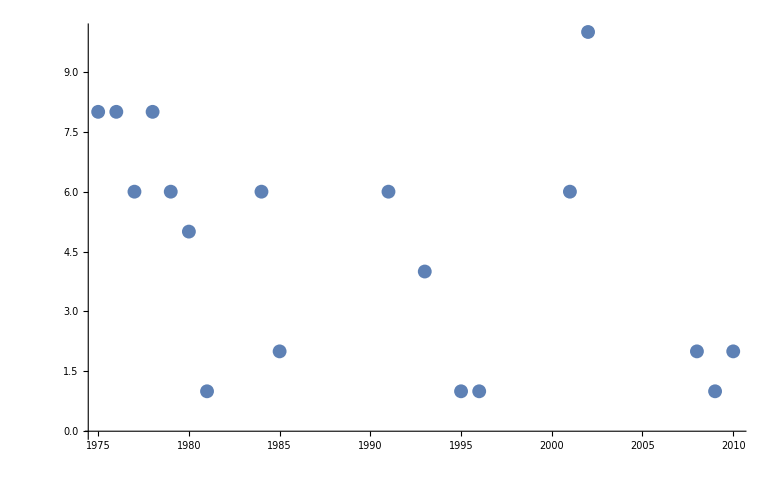

```mathematica
ListPlot[lol]
```

3.61413×10^10-5.97208×10^7 x+22201.8 x^2+9.84762 x^3-0.0049545 x^4-2.82149×10^-6 x^5+1.92017×10^-9 x^6-2.93899×10^-13 x^7

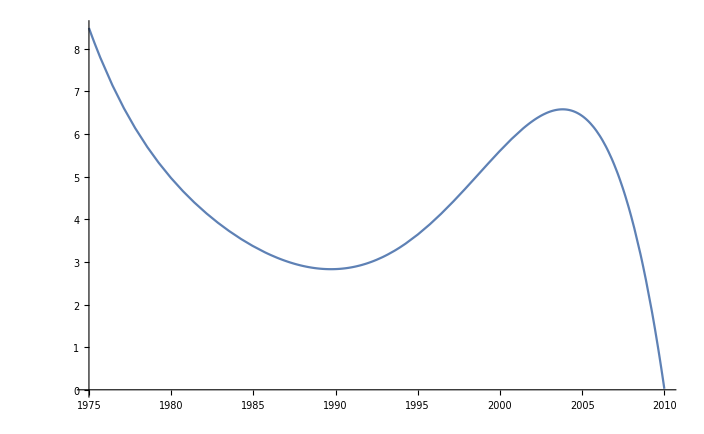

```mathematica
testy=Fit[lol,{1,x,x^2,x^3,x^4,x^5,x^6,x^7},x]

Plot[testy,{x,1975,2010}]
```

```mathematica
list= Range[1975,2010]
```

{1975,1976,1977,1978,1979,1980,1981,1982,1983,1984,1985,1986,1987,1988,1989,1990,1991,1992,1993,1994,1995,1996,1997,1998,1999,2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010}

```mathematica
lol[[All,1]]
```

{1975,1976,1977,1978,1979,1980,1981,1984,1985,1991,1993,1995,1996,2001,2002,2008,2009,2010}

```mathematica
fastRF[a_List,b_List]:=Module[{c,o,x},c=Join[b,a];
o=Ordering[c];
x=1-2 UnitStep[-1-Length[b]+o];
x=FoldList[Max[#,0]+#2&,x];
x[[o]]=x;
Pick[c,x,-1]]
```

```mathematica
other =fastRF[list,lol[[All,1]]]
```

{1982,1983,1986,1987,1988,1989,1990,1992,1994,1997,1998,1999,2000,2003,2004,2005,2006,2007}

```mathematica
Length[other]
```

18

```mathematica
thing = ConstantArray[0,Length[other]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
t=Split[other]
```

{{1982},{1983},{1986},{1987},{1988},{1989},{1990},{1992},{1994},{1997},{1998},{1999},{2000},{2003},{2004},{2005},{2006},{2007}}

```mathematica
Append[t]
```

Append[{{1982},{1983},{1986},{1987},{1988},{1989},{1990},{1992},{1994},{1997},{1998},{1999},{2000},{2003},{2004},{2005},{2006},{2007}}]

```mathematica
r=Flatten/@(Transpose@{t,thing})
```

{{1982,0},{1983,0},{1986,0},{1987,0},{1988,0},{1989,0},{1990,0},{1992,0},{1994,0},{1997,0},{1998,0},{1999,0},{2000,0},{2003,0},{2004,0},{2005,0},{2006,0},{2007,0}}

```mathematica
{{1977,0},{1983,0},{1986,0},{1991,0},{1999,0},{2000,0},{2002,0},{2003,0}}
```

{{1977,0},{1983,0},{1986,0},{1991,0},{1999,0},{2000,0},{2002,0},{2003,0}}

```mathematica
tot=Join[lol,r]
```

{{1975,8},{1976,8},{1977,6},{1978,8},{1979,6},{1980,5},{1981,1},{1984,6},{1985,2},{1991,6},{1993,4},{1995,1},{1996,1},{2001,6},{2002,10},{2008,2},{2009,1},{2010,2},{1982,0},{1983,0},{1986,0},{1987,0},{1988,0},{1989,0},{1990,0},{1992,0},{1994,0},{1997,0},{1998,0},{1999,0},{2000,0},{2003,0},{2004,0},{2005,0},{2006,0},{2007,0}}

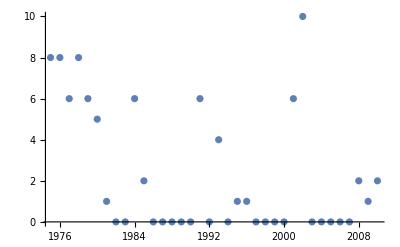

```mathematica
ListPlot[tot]
```

-4.00668×10^10+6.61177×10^7 x-24560.3 x^2-10.8543 x^3+0.00546082 x^4+3.09898×10^-6 x^5-2.10715×10^-9 x^6+3.22059×10^-13 x^7

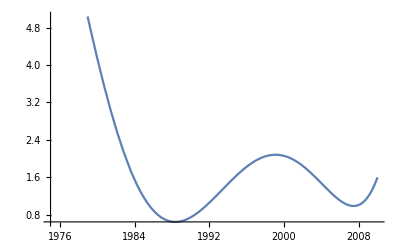

```mathematica
plop=Fit[tot,{1,x,x^2,x^3,x^4,x^5,x^6,x^7},x]
Plot[plop,{x,1975,2010}]
```

```mathematica
p=Mean[Flatten[tot[[All,{2}]]]]
```

83/36

```mathematica
N[p]
```

2.30556

```mathematica
3.2777777777777777
```

3.27778

```mathematica
For[i=0,i≤Length[temp],i++,For[k=0,k≤Length[temp],k++,Print[ Fit[Select[Select[temp3,#[[1]]==temp2[[i]]&], #[[3]] == temp2[[k]] &][[All,{2,4}]],{1,x,x^2,x^3,x^4,x^5,x^6,x^7},x]]]]
```

0

0

0

«36 more identical outputs»

-1.11881×10^11+1.85091×10^8 x-68955.5 x^2-30.5053 x^3+0.0154027 x^4+8.74736×10^-6 x^5-5.96572×10^-9 x^6+9.14148×10^-13 x^7

-3.35667×10^10+5.53688×10^7 x-20492.2 x^2-9.16949 x^3+0.00457371 x^4+2.62881×10^-6 x^5-1.78083×10^-9 x^6+2.72074×10^-13 x^7

4.0356×10^9-3.76722×10^6 x-445.5 x^2+0.661518 x^3+0.00033574 x^4-5.53861×10^-8 x^5-1.23×10^-10 x^6+3.32908×10^-14 x^7

-4.13001×10^11+6.83218×10^8 x-254045. x^2-113.23 x^3+0.056923 x^4+0.0000325313 x^5-2.21512×10^-8 x^6+3.39441×10^-12 x^7

-3.4487×10^10+5.67573×10^7 x-20930.8 x^2-9.39319 x^3+0.00466027 x^4+2.685×10^-6 x^5-1.81271×10^-9 x^6+2.7633×10^-13 x^7

-161.001-0.0580067 x-0.0000174892 x^2-2.85166×10^-9 x^3+1.58978×10^-12 x^4+2.33786×10^-15 x^5+1.95831×10^-18 x^6+1.38294×10^-21 x^7

-5.91526×10^11+9.76126×10^8 x-361800. x^2-161.282 x^3+0.0806909 x^4+0.0000462085 x^5-3.13483×10^-8 x^6+4.79142×10^-12 x^7

-4.88828×10^10+7.98433×10^7 x-29118.7 x^2-13.1452 x^3+0.00641604 x^4+3.71846×10^-6 x^5-2.48232×10^-9 x^6+3.75425×10^-13 x^7

1.77059×10^11-1.65291×10^8 x-19126.3 x^2+28.901 x^3+0.0145087 x^4-2.43638×10^-6 x^5-5.29241×10^-9 x^6+1.4325×10^-12 x^7

-1.90252×10^10+3.12481×10^7 x-11495.1 x^2-5.15735 x^3+0.00255059 x^4+1.4692×10^-6 x^5-9.89384×10^-10 x^6+1.50508×10^-13 x^7

-1.72161×10^11+2.83439×10^8 x-104723. x^2-46.7351 x^3+0.0232857 x^4+0.0000133351 x^5-9.02045×10^-9 x^6+1.37556×10^-12 x^7

1.03827×10^11-1.71247×10^8 x+63501.6 x^2+28.189 x^3-0.0141341 x^4-8.05164×10^-6 x^5+5.46623×10^-9 x^6-8.3509×10^-13 x^7

-1.76807×10^11+2.91784×10^8 x-108323. x^2-48.0017 x^3+0.0241123 x^4+0.0000137201 x^5-9.32379×10^-9 x^6+1.4252×10^-12 x^7

-1.34693×10^11+2.21961×10^8 x-82262.8 x^2-36.4368 x^3+0.018268 x^4+0.0000103853 x^5-7.04648×10^-9 x^6+1.07557×10^-12 x^7

5.32626×10^10-8.80609×10^7 x+32889.9 x^2+14.361 x^3-0.00730373 x^4-4.09464×10^-6 x^5+2.7997×10^-9 x^6-4.28754×10^-13 x^7

4.26188×10^10-7.09439×10^7 x+26819.3 x^2+11.5376 x^3-0.00598809 x^4-3.30707×10^-6 x^5+2.28886×10^-9 x^6-3.52813×10^-13 x^7

7.21374×10^10-1.18424×10^8 x+43527.5 x^2+19.547 x^3-0.00965358 x^4-5.56669×10^-6 x^5+3.74561×10^-9 x^6-5.69544×10^-13 x^7

-3.8472×10^12+6.34553×10^9 x-2.35335×10^6 x^2-1044.18 x^3+0.523546 x^4+0.000298429 x^5-2.02576×10^-7 x^6+3.09483×10^-11 x^7

-1.95049×10^11+3.22326×10^8 x-119721. x^2-53.3065 x^3+0.0267585 x^4+0.0000152941 x^5-1.03995×10^-8 x^6+1.59181×10^-12 x^7

-2.77958×10^11+4.59365×10^8 x-171039. x^2-75.4446 x^3+0.0380903 x^4+0.0000215845 x^5-1.47098×10^-8 x^6+2.25167×10^-12 x^7

-1.15371×10^11+1.90808×10^8 x-71208.6 x^2-31.2373 x^3+0.015847 x^4+8.92547×10^-6 x^5-6.09728×10^-9 x^6+9.33947×10^-13 x^7

6.86643×10^8-640676. x-73.5691 x^2+0.111751 x^3+0.0000558645 x^4-9.43319×10^-9 x^5-2.0325×10^-11 x^6+5.4985×10^-15 x^7

79.8854+0.0286457 x+8.67717×10^-6 x^2+1.51746×10^-9 x^3-6.50812×10^-13 x^4-1.02958×10^-15 x^5-8.66543×10^-19 x^6-6.08959×10^-22 x^7

-1.17363×10^10+1.08877×10^7 x+1255.51 x^2-1.88103 x^3-0.000939717 x^4+1.56464×10^-7 x^5+3.38703×10^-10 x^6-9.1104×10^-14 x^7

105244.+7.5595 x-0.0112724 x^2-9.41136×10^-6 x^3-4.71228×10^-9 x^4-1.41626×10^-12 x^5+2.34718×10^-16 x^6+8.25872×10^-19 x^7

168.751+0.0603575 x+0.0000181697 x^2+3.0803×10^-9 x^3-1.4621×10^-12 x^4-2.23216×10^-15 x^5-1.86663×10^-18 x^6-1.30858×10^-21 x^7

5.49979×10^11-5.11043×10^8 x-58975.4 x^2+88.5588 x^3+0.044301 x^4-7.39094×10^-6 x^5-1.60177×10^-8 x^6+4.31537×10^-12 x^7

25.3119+0.00908633 x+2.76457×10^-6 x^2+4.96112×10^-10 x^3-1.93455×10^-13 x^4-3.16691×10^-16 x^5-2.67928×10^-19 x^6-1.88554×10^-22 x^7

-31.1016-0.0109901 x-3.22265×10^-6 x^2-4.79105×10^-10 x^3+3.24564×10^-13 x^4+4.4334×10^-16 x^5+3.61699×10^-19 x^6+2.50613×10^-22 x^7

3.16887×10^11-2.93038×10^8 x-33781.5 x^2+50.3378 x^3+0.0250981 x^4-4.15562×10^-6 x^5-8.99501×10^-9 x^6+2.41175×10^-12 x^7

0.125+0.0000623752 x+3.11254×10^-8 x^2+1.55316×10^-11 x^3+7.75031×10^-15 x^4+3.86742×10^-18 x^5+1.92985×10^-21 x^6+9.62999×10^-25 x^7

7.24501×10^7-25684.1 x-17.9561 x^2-0.00385065 x^3+1.8975×10^-6 x^4+2.21546×10^-9 x^5+7.90216×10^-13 x^6-5.49068×10^-16 x^7

0

5.54942×10^10-5.13777×10^7 x-5912.09 x^2+8.84013 x^3+0.00440747 x^4-7.32306×10^-7 x^5-1.58219×10^-9 x^6+4.2471×10^-13 x^7

-65.2533-0.0231462 x-6.86806×10^-6 x^2-1.09905×10^-9 x^3+6.09228×10^-13 x^4+8.79636×10^-16 x^5+7.25159×10^-19 x^6+5.04169×10^-22 x^7

0

-3.50727×10^11+5.7956×10^8 x-215424. x^2-95.6166 x^3+0.0480875 x^4+0.000027401 x^5-1.8645×10^-8 x^6+2.85379×10^-12 x^7

0

8.09976×10^10-1.33309×10^8 x+49227.6 x^2+21.9813 x^3-0.0109408 x^4-6.27234×10^-6 x^5+4.24007×10^-9 x^6-6.46379×10^-13 x^7

3.20032×10^10-2.99719×10^7 x-3512.29 x^2+5.28413 x^3+0.00267392 x^4-4.47024×10^-7 x^5-9.83525×10^-10 x^6+2.67065×10^-13 x^7

5.33261×10^11-8.80515×10^8 x+326326. x^2+145.969 x^3-0.0729432 x^4-0.0000419161 x^5+2.84332×10^-8 x^6-4.34849×10^-12 x^7

-3.81091×10^11+6.28292×10^8 x-232165. x^2-104.266 x^3+0.0518402 x^4+0.0000299136 x^5-2.02317×10^-8 x^6+3.08947×10^-12 x^7

327034.+23.727 x-0.0357867 x^2-0.0000301936 x^3-1.52786×10^-8 x^4-4.64061×10^-12 x^5+7.77718×10^-16 x^6+2.76479×10^-18 x^7

-1.67109×10^12+2.76158×10^9 x-1.0252×10^6 x^2-457.395 x^3+0.22923 x^4+0.000131423 x^5-8.92931×10^-8 x^6+1.36675×10^-11 x^7

1.09562×10^11-1.80927×10^8 x+67301.9 x^2+29.6865 x^3-0.0149733 x^4-8.47794×10^-6 x^5+5.77336×10^-9 x^6-8.83082×10^-13 x^7

-4.49298×10^12+7.43185×10^9 x-2.76133×10^6 x^2-1233.73 x^3+0.619023 x^4+0.000354872 x^5-2.41414×10^-7 x^6+3.69892×10^-11 x^7

-5.97681×10^10+9.81173×10^7 x-36087.2 x^2-16.1619 x^3+0.00799389 x^4+4.59895×10^-6 x^5-3.096×10^-9 x^6+4.70728×10^-13 x^7

3.03395×10^11-5.01128×10^8 x+186173. x^2+82.6216 x^3-0.0415125 x^4-0.0000236746 x^5+1.60969×10^-8 x^6-2.46265×10^-12 x^7

-8.54665×10^11+1.41078×10^9 x-523228. x^2-233.043 x^3+0.116741 x^4+0.0000667534 x^5-4.53216×10^-8 x^6+6.92949×10^-12 x^7

1.10349×10^11-1.81998×10^8 x+67589.5 x^2+29.8204 x^3-0.0150067 x^4-8.50092×10^-6 x^5+5.77923×10^-9 x^6-8.82875×10^-13 x^7

-1.86061×10^11+3.06438×10^8 x-113375. x^2-50.4178 x^3+0.0251848 x^4+0.0000143848 x^5-9.74161×10^-9 x^6+1.48608×10^-12 x^7

-1.33706×10^11+2.20836×10^8 x-82155.3 x^2-36.2549 x^3+0.018286 x^4+0.000010358 x^5-7.05424×10^-9 x^6+1.07916×10^-12 x^7

-9.72537×10^11+1.59942×10^9 x-591266. x^2-261.892 x^3+0.130834 x^4+0.0000744423 x^5-5.03706×10^-8 x^6+7.67289×10^-12 x^7

-3.35673×10^11+5.53292×10^8 x-205276. x^2-90.6516 x^3+0.0455468 x^4+0.0000258264 x^5-1.754×10^-8 x^6+2.6779×10^-12 x^7

1.7483×10^11-2.86472×10^8 x+105023. x^2+47.1929 x^3-0.0232146 x^4-0.0000134104 x^5+8.99679×10^-9 x^6-1.36522×10^-12 x^7

9.88701×10^6-3542.44 x-2.4944 x^2-0.000538007 x^3+2.69166×10^-7 x^4+3.16016×10^-10 x^5+1.1347×10^-13 x^6-7.97011×10^-17 x^7

-1.92059×10^10+3.2176×10^7 x-12254. x^2-5.28176 x^3+0.00276524 x^4+1.53105×10^-6 x^5-1.06711×10^-9 x^6+1.65477×10^-13 x^7

3.91396×10^9-3.63361×10^6 x-422.89 x^2+0.629753 x^3+0.000316182 x^4-5.23252×10^-8 x^5-1.14321×10^-10 x^6+3.07723×10^-14 x^7

1.84008×10^9-1.70486×10^6 x-199.126 x^2+0.294621 x^3+0.000148042 x^4-2.43393×10^-8 x^5-5.3374×10^-11 x^6+1.43381×10^-14 x^7

71598.3+5.16278 x-0.0076405 x^2-6.38041×10^-6 x^3-3.19379×10^-9 x^4-9.60001×10^-13 x^5+1.57951×10^-16 x^6+5.57758×10^-19 x^7

-3.4567×10^10+3.20694×10^7 x+3686.52 x^2-5.53752 x^3-0.00276225 x^4+4.61097×10^-7 x^5+9.95071×10^-10 x^6-2.67667×10^-13 x^7

-32.2039-0.0113426 x-3.29402×10^-6 x^2-4.59714×10^-10 x^3+3.6304×10^-13 x^4+4.77554×10^-16 x^5+3.86566×10^-19 x^6+2.67054×10^-22 x^7

-331673.-23.6272 x+0.0356578 x^2+0.0000297182 x^3+1.48659×10^-8 x^4+4.46021×10^-12 x^5-7.47939×10^-16 x^6-2.61059×10^-18 x^7

1.1665×10^10-1.08157×10^7 x-1254.89 x^2+1.86902 x^3+0.000936391 x^4-1.54965×10^-7 x^5-3.37601×10^-10 x^6+9.07567×10^-14 x^7

-1.35259×10^12+1.25291×10^9 x+144075. x^2-215.745 x^3-0.107561 x^4+0.0000178901 x^5+3.86483×10^-8 x^6-1.03795×10^-11 x^7

4.91445×10^7-17581.8 x-12.2423 x^2-0.00260328 x^3+1.31464×10^-6 x^4+1.52205×10^-9 x^5+5.4069×10^-13 x^6-3.79135×10^-16 x^7

-54.251-0.0192598 x-5.71851×10^-6 x^2-9.14267×10^-10 x^3+5.10026×10^-13 x^4+7.35933×10^-16 x^5+6.07101×10^-19 x^6+4.22457×10^-22 x^7

0.25+0.00012475 x+6.22507×10^-8 x^2+3.10632×10^-11 x^3+1.55006×10^-14 x^4+7.73484×10^-18 x^5+3.8597×10^-21 x^6+1.926×10^-24 x^7

1.67712×10^9-597127. x-416.677 x^2-0.0890053 x^3+0.0000443691 x^4+5.15998×10^-8 x^5+1.83704×10^-11 x^6-1.28197×10^-14 x^7

0.25+0.000124564 x+6.20648×10^-8 x^2+3.09242×10^-11 x^3+1.54082×10^-14 x^4+7.67721×10^-18 x^5+3.82521×10^-21 x^6+1.90594×10^-24 x^7

2.39703×10^7-8556.96 x-5.97707 x^2-0.00127721 x^3+6.39694×10^-7 x^4+7.44161×10^-10 x^5+2.65151×10^-13 x^6-1.85533×10^-16 x^7

-9.97191×10^8+751138. x+148.73 x^2-0.0946473 x^3-0.0000630484 x^4-9.72081×10^-11 x^5+1.64567×10^-11 x^6-3.00136×10^-15 x^7

0

-9.72329×10^10+1.60096×10^8 x-59109.3 x^2-26.4629 x^3+0.013159 x^4+7.5619×10^-6 x^5-5.11113×10^-9 x^6+7.79449×10^-13 x^7

-2.68086×10^11+4.42247×10^8 x-163801. x^2-73.1075 x^3+0.0365291 x^4+0.0000209434 x^5-1.41982×10^-8 x^6+2.1694×10^-12 x^7

0

2.16684×10^10-2.03052×10^7 x-2356.48 x^2+3.57679 x^3+0.00180169 x^4-3.0389×10^-7 x^5-6.62123×10^-10 x^6+1.79899×10^-13 x^7

1.23463×10^12-2.0413×10^9 x+758563. x^2+338.013 x^3-0.16983 x^4-0.0000969873 x^5+6.60079×10^-8 x^6-1.01096×10^-11 x^7

1.54293×10^10-2.57251×10^7 x+9731.42 x^2+4.2086 x^3-0.00218227 x^4-1.21201×10^-6 x^5+8.39209×10^-10 x^6-1.29551×10^-13 x^7

978786.+70.7379 x-0.10718 x^2-0.0000903218 x^3-4.56661×10^-8 x^4-1.3854×10^-11 x^5+2.33238×10^-15 x^6+8.25949×10^-18 x^7

-3.9159×10^8+368314. x+42.2888 x^2-0.0651666 x^3-0.0000327077 x^4+5.60006×10^-9 x^5+1.20702×10^-11 x^6-3.29084×10^-15 x^7

-1.71328×10^10+2.80757×10^7 x-10305. x^2-4.61139 x^3+0.00227537 x^4+1.30778×10^-6 x^5-8.78576×10^-10 x^6+1.33334×10^-13 x^7

-1.68517×10^9+1.57933×10^6 x+182.927 x^2-0.278151 x^3-0.000139973 x^4+2.36544×10^-8 x^5+5.14275×10^-11 x^6-1.39744×10^-14 x^7

-1.00183×10^10+1.59134×10^7 x-5519.41 x^2-2.62229 x^3+0.00117849 x^4+7.207×10^-7 x^5-4.56613×10^-10 x^6+6.6816×10^-14 x^7

1.681×10^10-2.82481×10^7 x+10829.1 x^2+4.61164 x^3-0.00244383 x^4-1.3371×10^-6 x^5+9.37976×10^-10 x^6-1.45823×10^-13 x^7

8.56429×10^11-1.41505×10^9 x+526134. x^2+233.146 x^3-0.117384 x^4-0.0000667312 x^5+4.54299×10^-8 x^6-6.95305×10^-12 x^7

-1.83532×10^11+3.03001×10^8 x-112573. x^2-49.8321 x^3+0.0250641 x^4+0.0000142474 x^5-9.6893×10^-9 x^6+1.48165×10^-12 x^7

-1.77933×10^11+2.92851×10^8 x-108131. x^2-48.3021 x^3+0.0240355 x^4+0.0000137849 x^5-9.3176×10^-9 x^6+1.42042×10^-12 x^7

2.67468×10^10-4.40396×10^7 x+16304.5 x^2+7.22238 x^3-0.00361566 x^4-2.05621×10^-6 x^5+1.39359×10^-9 x^6-2.12542×10^-13 x^7

-6.48319×10^11+1.06569×10^9 x-394713. x^2-173.115 x^3+0.087001 x^4+0.0000489403 x^5-3.31921×10^-8 x^6+5.05395×10^-12 x^7

9.87123×10^10-1.62449×10^8 x+59922. x^2+26.8601 x^3-0.0133367 x^4-7.67181×10^-6 x^5+5.18114×10^-9 x^6-7.8978×10^-13 x^7

-1.27051×10^9+1.17852×10^6 x+138.284 x^2-0.204277 x^3-0.000102942 x^4+1.68961×10^-8 x^5+3.72245×10^-11 x^6-1.00111×10^-14 x^7

-1.202×10^11+1.98149×10^8 x-73484.7 x^2-32.5223 x^3+0.0163218 x^4+9.27335×10^-6 x^5-6.29563×10^-9 x^6+9.61275×10^-13 x^7

-1.06737×10^11+1.76011×10^8 x-65267.3 x^2-28.9417 x^3+0.0145092 x^4+8.26837×10^-6 x^5-5.61113×10^-9 x^6+8.56993×10^-13 x^7

-3.04746×10^7+10906.5 x+7.65479 x^2+0.00164481 x^3-8.23718×10^-7 x^4-9.6358×10^-10 x^5-3.44988×10^-13 x^6+2.42008×10^-16 x^7

3.86133×10^11-6.36408×10^8 x+236106. x^2+104.23 x^3-0.0523696 x^4-0.0000296909 x^5+2.0163×10^-8 x^6-3.07808×10^-12 x^7

-1.05402×10^8+37672.1 x+26.3891 x^2+0.00565841 x^3-2.83175×10^-6 x^4-3.30569×10^-9 x^5-1.18132×10^-12 x^6+8.27573×10^-16 x^7

1.61389×10^10-1.49823×10^7 x-1716.38 x^2+2.5882 x^3+0.00128926 x^4-2.16033×10^-7 x^5-4.64663×10^-10 x^6+1.25069×10^-13 x^7

2.24492×10^7-7972.85 x-5.60577 x^2-0.00121052 x^3+5.94922×10^-7 x^4+6.99473×10^-10 x^5+2.50904×10^-13 x^6-1.74657×10^-16 x^7

-9.75431×10^7+34986.5 x+24.4401 x^2+0.00521519 x^3-2.63829×10^-6 x^4-3.06516×10^-9 x^5-1.09242×10^-12 x^6+7.67978×10^-16 x^7

-6.78131×10^8+242292. x+169.792 x^2+0.0364319 x^3-0.0000182096 x^4-2.12723×10^-8 x^5-7.60547×10^-12 x^6+5.32612×10^-15 x^7

-414.587-0.147894 x-0.0000442772 x^2-7.31848×10^-9 x^3+3.74337×10^-12 x^4+5.56926×10^-15 x^5+4.63155×10^-18 x^6+3.2383×10^-21 x^7

0

3.80264×10^11-3.51849×10^8 x-40486.9 x^2+60.4813 x^3+0.0301366 x^4-5.00247×10^-6 x^5-1.08081×10^-8 x^6+2.89956×10^-12 x^7

0.416667+0.000166293 x+6.22197×10^-8 x^2+2.06933×10^-11 x^3+5.1617×10^-15 x^4-8.01096×10^-24 x^5-1.28464×10^-21 x^6-1.28175×10^-24 x^7

-74593.7-5.30851 x+0.00793719 x^2+6.59091×10^-6 x^3+3.28383×10^-9 x^4+9.81646×10^-13 x^5-1.63084×10^-16 x^6-5.68661×10^-19 x^7

0.25+0.000124688 x+6.21887×10^-8 x^2+3.10168×10^-11 x^3+1.54697×10^-14 x^4+7.71557×10^-18 x^5+3.84817×10^-21 x^6+1.91928×10^-24 x^7

-5.06387×10^9+4.69547×10^6 x+539.856 x^2-0.810041 x^3-0.000403971 x^4+6.73682×10^-8 x^5+1.45386×10^-10 x^6-3.90868×10^-14 x^7

-1.15108×10^11+1.0671×10^8 x+12241.8 x^2-18.3942 x^3-0.00916124 x^4+1.52954×10^-6 x^5+3.29477×10^-9 x^6-8.85594×10^-13 x^7

0

-8.04453×10^9+7.54153×10^6 x+873. x^2-1.32876 x^3-0.000668602 x^4+1.13088×10^-7 x^5+2.45767×10^-10 x^6-6.68026×10^-14 x^7

-4.17737×10^9+3.90424×10^6 x+455.819 x^2-0.6853 x^3-0.000345765 x^4+5.77714×10^-8 x^5+1.26613×10^-10 x^6-3.43101×10^-14 x^7

-2.98735×10^9+2.79918×10^6 x+325.87 x^2-0.493311 x^3-0.000248863 x^4+4.18658×10^-8 x^5+9.14977×10^-11 x^6-2.48575×10^-14 x^7

0

-1.68153×10^8+150878. x+19.9872 x^2-0.0252071 x^3-0.0000133441 x^4+1.81725×10^-9 x^5+4.65014×10^-12 x^6-1.2043×10^-15 x^7

-2.27827×10^9+2.12495×10^6 x+250.893 x^2-0.372453 x^3-0.000188797 x^4+3.11402×10^-8 x^5+6.90367×10^-11 x^6-1.86693×10^-14 x^7

-3.09014×10^6-223.33 x+0.339235 x^2+0.000286109 x^3+1.44787×10^-7 x^4+4.39605×10^-11 x^5-7.41953×10^-15 x^6-2.62746×10^-17 x^7

-5.91366×10^9+5.53762×10^6 x+642.091 x^2-0.974026 x^3-0.000490221 x^4+8.26459×10^-8 x^5+1.79883×10^-10 x^6-4.88389×10^-14 x^7

-3.21558×10^9+3.01101×10^6 x+348.869 x^2-0.529496 x^3-0.000266396 x^4+4.49306×10^-8 x^5+9.77338×10^-11 x^6-2.65339×10^-14 x^7

5.27229×10^9-4.94237×10^6 x-569.671 x^2+0.86998 x^3+0.000436802 x^4-7.41277×10^-8 x^5-1.60405×10^-10 x^6+4.35975×10^-14 x^7

4.26464×10^9-3.98955×10^6 x-464.459 x^2+0.701052 x^3+0.000353382 x^4-5.92746×10^-8 x^5-1.29549×10^-10 x^6+3.51381×10^-14 x^7

-9.27742×10^9+8.68814×10^6 x+1008.72 x^2-1.52878 x^3-0.000769978 x^4+1.29683×10^-7 x^5+2.82657×10^-10 x^6-7.67485×10^-14 x^7

7271.82+0.522549 x-0.000792778 x^2-6.65724×10^-7 x^3-3.35468×10^-10 x^4-1.01386×10^-13 x^5+1.7125×10^-17 x^6+6.02051×10^-20 x^7

4.31039×10^9-4.03115×10^6 x-468.914 x^2+0.707866 x^3+0.000356613 x^4-5.98265×10^-8 x^5-1.30641×10^-10 x^6+3.54239×10^-14 x^7

1.8654×10^10-1.74598×10^7 x-2042.73 x^2+3.07399 x^3+0.00155378 x^4-2.59831×10^-7 x^5-5.70725×10^-10 x^6+1.54883×10^-13 x^7

-1.55602×10^11+1.45876×10^8 x+17020.1 x^2-25.7425 x^3-0.0130059 x^4+2.18571×10^-6 x^5+4.78854×10^-9 x^6-1.3016×10^-12 x^7

-1.68715×10^8+60631. x+42.8155 x^2+0.00926319 x^3-4.64682×10^-6 x^4-5.47347×10^-9 x^5-1.97193×10^-12 x^6+1.38898×10^-15 x^7

-1.77955×10^10+1.66446×10^7 x+1928.82 x^2-2.92121 x^3-0.00146896 x^4+2.4724×10^-7 x^5+5.37853×10^-10 x^6-1.45861×10^-13 x^7

1.66679+0.000671227 x+2.53406×10^-7 x^2+8.50347×10^-11 x^3+2.13989×10^-14 x^4-2.76386×10^-21 x^5-5.42437×10^-21 x^6-5.45984×10^-24 x^7

2.99242×10^9-2.79766×10^6 x-325.92 x^2+0.491128 x^3+0.00024757 x^4-4.14587×10^-8 x^5-9.06685×10^-11 x^6+2.45773×10^-14 x^7

1.91028×10^11-1.78461×10^8 x-20730.7 x^2+31.269 x^3+0.015734 x^4-2.63712×10^-6 x^5-5.75167×10^-9 x^6+1.55795×10^-12 x^7

251.585+0.0903745 x+0.0000273167 x^2+4.64191×10^-9 x^3-2.22815×10^-12 x^4-3.4092×10^-15 x^5-2.86251×10^-18 x^6-2.01542×10^-21 x^7

32041.3+2.2598 x-0.00351494 x^2-2.93786×10^-6 x^3-1.47603×10^-9 x^4-4.43988×10^-13 x^5+7.68091×10^-17 x^6+2.65198×10^-19 x^7

0

0

0

«11 more identical outputs»

1.33041×10^11-2.18048×10^8 x+79807.1 x^2+36.1302 x^3-0.0177038 x^4-0.0000102863 x^5+6.89207×10^-9 x^6-1.04596×10^-12 x^7

-7.95449×10^10+1.31248×10^8 x-48641. x^2-21.6815 x^3+0.0108486 x^4+6.2073×10^-6 x^5-4.2114×10^-9 x^6+6.43624×10^-13 x^7

-8.81783×10^10+1.45182×10^8 x-53527. x^2-24.094 x^3+0.0119394 x^4+6.8993×10^-6 x^5-4.65685×10^-9 x^6+7.10184×10^-13 x^7

-6.29021×10^9+5.82837×10^6 x+700.724 x^2-1.01308 x^3-0.000516652 x^4+8.28655×10^-8 x^5+1.8736×10^-10 x^6-5.03206×10^-14 x^7

0

-1.70306×10^11+2.80683×10^8 x-103785. x^2-46.4189 x^3+0.0231329 x^4+0.0000132825 x^5-8.99097×10^-9 x^6+1.37253×10^-12 x^7

-325708.-23.5344 x+0.0357148 x^2+0.0000301082 x^3+1.52292×10^-8 x^4+4.62186×10^-12 x^5-7.79303×10^-16 x^6-2.7592×10^-18 x^7

6.32433×10^11-1.04401×10^9 x+387006. x^2+172.776 x^3-0.0864557 x^4-0.0000495112 x^5+3.36053×10^-8 x^6-5.13856×10^-12 x^7

1.02909×10^10-1.68124×10^7 x+6126.56 x^2+2.77664 x^3-0.00135169 x^4-7.87343×10^-7 x^5+5.25008×10^-10 x^6-7.94053×10^-14 x^7

8.08588×10^11-1.33523×10^9 x+495444. x^2+220.581 x^3-0.110435 x^4-0.0000633815 x^5+4.30071×10^-8 x^6-6.57691×10^-12 x^7

8.31446×10^8-776806. x-90.7741 x^2+0.13629 x^3+0.0000687796 x^4-1.1478×10^-8 x^5-2.5173×10^-11 x^6+6.81905×10^-15 x^7

-4.50744×10^10+7.43685×10^7 x-27612.1 x^2-12.2159 x^3+0.0061406 x^4+3.48769×10^-6 x^5-2.3705×10^-9 x^6+3.62257×10^-13 x^7

-1.17695×10^12+1.94457×10^9 x-722816. x^2-320.566 x^3+0.161256 x^4+0.0000918247 x^5-6.24816×10^-8 x^6+9.562×10^-12 x^7

-3.625×10^12+5.96916×10^9 x-2.20637×10^6 x^2-984.102 x^3+0.490871 x^4+0.000280622 x^5-1.89968×10^-7 x^6+2.89772×10^-11 x^7

-9.10123×10^10+1.49642×10^8 x-55271. x^2-24.5358 x^3+0.0122381 x^4+6.97322×10^-6 x^5-4.71499×10^-9 x^6+7.18024×10^-13 x^7

2.49982×10^11-4.12716×10^8 x+153663. x^2+67.4554 x^3-0.0341105 x^4-0.0000192255 x^5+1.31035×10^-8 x^6-2.00377×10^-12 x^7

-1.30053×10^11+2.13763×10^8 x-79047.4 x^2-34.8749 x^3+0.0174535 x^4+9.88614×10^-6 x^5-6.69244×10^-9 x^6+1.01891×10^-12 x^7

-1.56137×10^12+2.57817×10^9 x-956502. x^2-426.216 x^3+0.213662 x^4+0.000122074 x^5-8.29376×10^-8 x^6+1.2686×10^-11 x^7

5.57616×10^11-9.20395×10^8 x+341762. x^2+151.431 x^3-0.0760434 x^4-0.0000433501 x^5+2.94511×10^-8 x^6-4.50234×10^-12 x^7

2.76668×10^10-4.59797×10^7 x+17246.8 x^2+7.59426 x^3-0.00387321 x^4-2.19055×10^-6 x^5+1.50382×10^-9 x^6-2.3144×10^-13 x^7

-8.11589×10^10+1.33394×10^8 x-49326.4 x^2-21.7606 x^3+0.0108895 x^4+6.16785×10^-6 x^5-4.1749×10^-9 x^6+6.35549×10^-13 x^7

1.9916×10^10-1.85112×10^7 x-2149.95 x^2+3.21381 x^3+0.00161269 x^4-2.67927×10^-7 x^5-5.84086×10^-10 x^6+1.57406×10^-13 x^7

-9.87307×10^11+1.62805×10^9 x-604354. x^2-266.804 x^3+0.1341 x^4+0.0000761257 x^5-5.17099×10^-8 x^6+7.89748×10^-12 x^7

14.2866+0.00516312 x+1.59195×10^-6 x^2+3.01473×10^-10 x^3-9.63357×10^-14 x^4-1.716×10^-16 x^5-1.47458×10^-19 x^6-1.04524×10^-22 x^7

0.25+0.000125 x+6.25×10^-8 x^2+3.125×10^-11 x^3+1.5625×10^-14 x^4+7.8125×10^-18 x^5+3.90625×10^-21 x^6+1.95312×10^-24 x^7

1.25+0.000626881 x+3.14383×10^-7 x^2+1.57665×10^-10 x^3+7.90696×10^-14 x^4+3.96537×10^-17 x^5+1.98865×10^-20 x^6+9.97319×10^-24 x^7

0.25+0.000124875 x+6.23752×10^-8 x^2+3.11564×10^-11 x^3+1.55627×10^-14 x^4+7.77355×10^-18 x^5+3.88289×10^-21 x^6+1.93951×10^-24 x^7

0

-80.2507-0.0285127 x-8.45583×10^-6 x^2-1.33056×10^-9 x^3+7.8194×10^-13 x^4+1.11385×10^-15 x^5+9.18001×10^-19 x^6+6.39356×10^-22 x^7

0

10.7273+0.00145019 x-1.80735×10^-7 x^2-1.8019×10^-10 x^3-3.36834×10^-14 x^4+2.23894×10^-17 x^5+1.67413×10^-20 x^6-5.56379×10^-24 x^7

-1.00836×10^8+35807.6 x+25.0163 x^2+0.00535675 x^3-2.65149×10^-6 x^4-3.09118×10^-9 x^5-1.1018×10^-12 x^6+7.66867×10^-16 x^7

0.25+0.000124564 x+6.20648×10^-8 x^2+3.09242×10^-11 x^3+1.54082×10^-14 x^4+7.67721×10^-18 x^5+3.82521×10^-21 x^6+1.90594×10^-24 x^7

0

2.57105×10^10-2.37953×10^7 x-2741.91 x^2+4.0929 x^3+0.00204166 x^4-3.38656×10^-7 x^5-7.32651×10^-10 x^6+1.96599×10^-13 x^7

0.125+0.0000623131 x+3.10633×10^-8 x^2+1.54852×10^-11 x^3+7.71945×10^-15 x^4+3.84818×10^-18 x^5+1.91833×10^-21 x^6+9.56299×10^-25 x^7

0

2.91908×10^11-4.82249×10^8 x+179119. x^2+79.6512 x^3-0.0400079 x^4-0.0000228204 x^5+1.55202×10^-8 x^6-2.37508×10^-12 x^7

-5.07533×10^10+8.3583×10^7 x-30844.7 x^2-13.8499 x^3+0.00687578 x^4+3.96482×10^-6 x^5-2.6784×10^-9 x^6+4.08568×10^-13 x^7

-5.50906×10^10+9.10511×10^7 x-33860.5 x^2-15.0125 x^3+0.00755668 x^4+4.30204×10^-6 x^5-2.92847×10^-9 x^6+4.48281×10^-13 x^7

1.03191×10^11-9.66826×10^7 x-11255.4 x^2+17.0359 x^3+0.00859434 x^4-1.44541×10^-6 x^5-3.15951×10^-9 x^6+8.5829×10^-13 x^7

4.76267×10^10-7.85005×10^7 x+29014.4 x^2+13.0016 x^3-0.00647143 x^4-3.72411×10^-6 x^5+2.51954×10^-9 x^6-3.8463×10^-13 x^7

0

-2.86591×10^9+1.03575×10^6 x+733.629 x^2+0.159067 x^3-0.0000804893 x^4-9.50156×10^-8 x^5-3.43365×10^-11 x^6+2.43224×10^-14 x^7

-5.97698×10^11+9.88364×10^8 x-367438. x^2-163.515 x^3+0.0821276 x^4+0.0000470268 x^5-3.19857×10^-8 x^6+4.89864×10^-12 x^7

9.80743×10^10-1.61753×10^8 x+60097.2 x^2+26.468 x^3-0.0133339 x^4-7.54069×10^-6 x^5+5.12852×10^-9 x^6-7.83452×10^-13 x^7

9.05364×10^9-8.48315×10^6 x-981.516 x^2+1.49314 x^3+0.000750914 x^4-1.26953×10^-7 x^5-2.75733×10^-10 x^6+7.49092×10^-14 x^7

-6.65231×10^11+1.09821×10^9 x-407196. x^2-181.639 x^3+0.0909052 x^4+0.0000520834 x^5-3.53485×10^-8 x^6+5.40516×10^-12 x^7

-1.2557×10^11+2.06801×10^8 x-76582.8 x^2-33.9227 x^3+0.0169864 x^4+9.66223×10^-6 x^5-6.54957×10^-9 x^6+9.99051×10^-13 x^7

9.42713×10^9-8.80819×10^6 x-1028.81 x^2+1.5454 x^3+0.000779785 x^4-1.30173×10^-7 x^5-2.85418×10^-10 x^6+7.73208×10^-14 x^7

-5.15701×10^11+8.50349×10^8 x-315779. x^2-139.201 x^3+0.0700655 x^4+0.0000396529 x^5-2.69564×10^-8 x^6+4.11713×10^-12 x^7

3.73556×10^9-3.49347×10^6 x-408.718 x^2+0.614135 x^3+0.000310275 x^4-5.18128×10^-8 x^5-1.13787×10^-10 x^6+3.0853×10^-14 x^7

-3.44578×10^11+5.67853×10^8 x-210660. x^2-92.9658 x^3+0.0467162 x^4+0.0000264673 x^5-1.79743×10^-8 x^6+2.74364×10^-12 x^7

-1.81081×10^12+2.97826×10^9 x-1.10199×10^6 x^2-486.595 x^3+0.243689 x^4+0.000138078 x^5-9.35405×10^-8 x^6+1.42507×10^-11 x^7

-4.39719×10^11+7.24096×10^8 x-268015. x^2-118.895 x^3+0.0594708 x^4+0.0000338791 x^5-2.29542×10^-8 x^6+3.50112×10^-12 x^7

-7.73136×10^11+1.2759×10^9 x-473728. x^2-209.817 x^3+0.105407 x^4+0.000059988 x^5-4.07645×10^-8 x^6+6.23109×10^-12 x^7

-2.04289×10^6+717.324 x+0.51067 x^2+0.0001125 x^3-5.31541×10^-8 x^4-6.38045×10^-11 x^5-2.31708×10^-14 x^6+1.5943×10^-17 x^7

1.56575×10^10-1.46078×10^7 x-1692.45 x^2+2.55193 x^3+0.00128154 x^4-2.14733×10^-7 x^5-4.67075×10^-10 x^6+1.26344×10^-13 x^7

9.31778×10^9-8.65505×10^6 x-1001.92 x^2+1.4999 x^3+0.00075121 x^4-1.24995×10^-7 x^5-2.71576×10^-10 x^6+7.31412×10^-14 x^7

1.5575×10^9-1.45398×10^6 x-165.228 x^2+0.253321 x^3+0.000126016 x^4-2.14732×10^-8 x^5-4.5796×10^-11 x^6+1.23956×10^-14 x^7

1.+0.000498753 x+2.48755×10^-7 x^2+1.24067×10^-10 x^3+6.18789×10^-14 x^4+3.08623×10^-17 x^5+1.53927×10^-20 x^6+7.67714×10^-24 x^7

7.45928×10^10-6.90653×10^7 x-7957.89 x^2+11.8884 x^3+0.00593135 x^4-9.84585×10^-7 x^5-2.13015×10^-9 x^6+5.71849×10^-13 x^7

0

56.3374+0.020176 x+6.08362×10^-6 x^2+1.03566×10^-9 x^3-4.87207×10^-13 x^4-7.47091×10^-16 x^5-6.25769×10^-19 x^6-4.39233×10^-22 x^7

-1.44659×10^8+51329.8 x+36.0395 x^2+0.00777045 x^3-3.81742×10^-6 x^4-4.48147×10^-9 x^5-1.60536×10^-12 x^6+1.11646×10^-15 x^7

-401471.-28.6776 x+0.0428882 x^2+0.0000357068 x^3+1.78345×10^-8 x^4+5.34527×10^-12 x^5-8.88242×10^-16 x^6-3.10882×10^-18 x^7

-33465.8-2.3919 x+0.00357549 x^2+2.97751×10^-6 x^3+1.48747×10^-9 x^4+4.45926×10^-13 x^5-7.40577×10^-17 x^6-2.59362×10^-19 x^7

224.921+0.0801972 x+0.000024055 x^2+4.04965×10^-9 x^3-1.94223×10^-12 x^4-2.94373×10^-15 x^5-2.45274×10^-18 x^6-1.7141×10^-21 x^7

0

-1.42847×10^11+1.32197×10^8 x+15194.6 x^2-22.7235 x^3-0.0113218 x^4+1.88118×10^-6 x^5+4.06048×10^-9 x^6-1.08952×10^-12 x^7

-125374.-8.88745 x+0.0133667 x^2+0.0000110909 x^3+5.5238×10^-9 x^4+1.64999×10^-12 x^5-2.7572×10^-16 x^6-9.57721×10^-19 x^7

0.25+0.000124626 x+6.21267×10^-8 x^2+3.09704×10^-11 x^3+1.54389×10^-14 x^4+7.69636×10^-18 x^5+3.83667×10^-21 x^6+1.9126×10^-24 x^7

6.0579×10^9-5.61094×10^6 x-645.737 x^2+0.96619 x^3+0.000481856 x^4-8.01111×10^-8 x^5-1.73116×10^-10 x^6+4.64895×10^-14 x^7

0

1.6399×10^9-592435. x-419.711 x^2-0.0910397 x^3+0.0000460166 x^4+5.43434×10^-8 x^5+1.96425×10^-11 x^6-1.39084×10^-14 x^7

-21664.6-1.58549 x+0.00233139 x^2+1.96214×10^-6 x^3+9.88819×10^-10 x^4+2.99387×10^-13 x^5-4.90028×10^-17 x^6-1.75263×10^-19 x^7

1.20414×10^9-1.11757×10^6 x-133.888 x^2+0.19474 x^3+0.0000991766 x^4-1.60304×10^-8 x^5-3.60399×10^-11 x^6+9.69795×10^-15 x^7

331.834+0.11989 x+0.0000364217 x^2+6.19002×10^-9 x^3-3.04711×10^-12 x^4-4.66153×10^-15 x^5-3.93376×10^-18 x^6-2.78566×10^-21 x^7

6.25023×10^7-56396.3 x-7.31134 x^2+0.00948423 x^3+4.97106×10^-6 x^4-7.04113×10^-10 x^5-1.74336×10^-12 x^6+4.54934×10^-16 x^7

-2.84984×10^11+2.66671×10^8 x+31079.8 x^2-46.8964 x^3-0.0236489 x^4+3.96824×10^-6 x^5+8.67361×10^-9 x^6-2.35326×10^-12 x^7

0

167.75+0.0607894 x+0.0000185591 x^2+3.21259×10^-9 x^3-1.50313×10^-12 x^4-2.34496×10^-15 x^5-1.98888×10^-18 x^6-1.41267×10^-21 x^7

22086.5+1.5454 x-0.00240313 x^2-1.9972×10^-6 x^3-9.97856×10^-10 x^4-2.98294×10^-13 x^5+5.16835×10^-17 x^6+1.7665×10^-19 x^7

-55764.5-4.13784 x+0.00603497 x^2+5.11605×10^-6 x^3+2.59519×10^-9 x^4+7.91989×10^-13 x^5-1.28181×10^-16 x^6-4.66612×10^-19 x^7

-325.336-0.117362 x-0.0000354902 x^2-5.87587×10^-9 x^3+3.13592×10^-12 x^4+4.67573×10^-15 x^5+3.92778×10^-18 x^6+2.77717×10^-21 x^7

1.49968×10^7-5387.38 x-3.80663 x^2-0.000823945 x^3+4.1304×10^-7 x^4+4.86581×10^-10 x^5+1.75252×10^-13 x^6-1.23432×10^-16 x^7

2.08334+0.000843242 x+3.19975×10^-7 x^2+1.07926×10^-10 x^3+2.73023×10^-14 x^4-4.41997×10^-23 x^5-6.98888×10^-21 x^6-7.07196×10^-24 x^7

-12757.1-0.925594 x+0.0013783 x^2+1.15781×10^-6 x^3+5.82878×10^-10 x^4+1.76145×10^-13 x^5-2.92139×10^-17 x^6-1.03541×10^-19 x^7

-1.17421×10^10+1.09457×10^7 x+1275.56 x^2-1.91173 x^3-0.000962084 x^4+1.60396×10^-7 x^5+3.50402×10^-10 x^6-9.47082×10^-14 x^7

20060.+1.46094 x-0.00216336 x^2-1.81882×10^-6 x^3-9.16101×10^-10 x^4-2.77076×10^-13 x^5+4.5737×10^-17 x^6+1.62682×10^-19 x^7

-26.34-0.00935344 x-2.7481×10^-6 x^2-4.00059×10^-10 x^3+2.91556×10^-13 x^4+3.93738×10^-16 x^5+3.21867×10^-19 x^6+2.23909×10^-22 x^7

-42.0432-0.0149534 x-4.418×10^-6 x^2-6.68013×10^-10 x^3+4.41974×10^-13 x^4+6.11554×10^-16 x^5+5.02264×10^-19 x^6+3.49934×10^-22 x^7

0.25+0.00012475 x+6.22507×10^-8 x^2+3.10632×10^-11 x^3+1.55006×10^-14 x^4+7.73484×10^-18 x^5+3.8597×10^-21 x^6+1.926×10^-24 x^7

-245.794-0.0886964 x-0.00002686 x^2-4.48867×10^-9 x^3+2.32658×10^-12 x^4+3.49971×10^-15 x^5+2.94397×10^-18 x^6+2.0822×10^-21 x^7

503.668+0.179486 x+0.0000537664 x^2+8.99326×10^-9 x^3-4.39936×10^-12 x^4-6.62329×10^-15 x^5-5.5113×10^-18 x^6-3.84943×10^-21 x^7

0.625+0.000311876 x+1.55627×10^-7 x^2+7.76581×10^-11 x^3+3.87516×10^-14 x^4+1.93371×10^-17 x^5+9.64925×10^-21 x^6+4.815×10^-24 x^7

0.625+0.000311721 x+1.55472×10^-7 x^2+7.7542×10^-11 x^3+3.86743×10^-14 x^4+1.92889×10^-17 x^5+9.62041×10^-21 x^6+4.79821×10^-24 x^7

0

0

0

«2 more identical outputs»

1.+0.000498504 x+2.48507×10^-7 x^2+1.23882×10^-10 x^3+6.17556×10^-14 x^4+3.07854×10^-17 x^5+1.53467×10^-20 x^6+7.65039×10^-24 x^7

0.875+0.000436191 x+2.17443×10^-7 x^2+1.08397×10^-10 x^3+5.40361×10^-14 x^4+2.69373×10^-17 x^5+1.34283×10^-20 x^6+6.69409×10^-24 x^7

-833.752-0.297037 x-0.0000888675 x^2-1.47417×10^-8 x^3+7.4086×10^-12 x^4+1.10609×10^-14 x^5+9.19217×10^-18 x^6+6.41872×10^-21 x^7

0

335.836+0.119713 x+0.000035874 x^2+6.00532×10^-9 x^3-2.93345×10^-12 x^4-4.41996×10^-15 x^5-3.67921×10^-18 x^6-2.57054×10^-21 x^7

0

-665.005-0.236767 x-0.000070753 x^2-1.16798×10^-8 x^3+5.9494×10^-12 x^4+8.83992×10^-15 x^5+7.3379×10^-18 x^6+5.12061×10^-21 x^7

0.5+0.000249377 x+1.24377×10^-7 x^2+6.20336×10^-11 x^3+3.09394×10^-14 x^4+1.54311×10^-17 x^5+7.69633×10^-21 x^6+3.83857×10^-24 x^7

0

-1.57923×10^9+1.47625×10^6 x+172.365 x^2-0.259212 x^3-0.000130798 x^4+2.18608×10^-8 x^5+4.79103×10^-11 x^6-1.2985×10^-14 x^7

-4.55001×10^10+7.48914×10^7 x-27645.1 x^2-12.3664 x^3+0.00614872 x^4+3.5317×10^-6 x^5-2.3865×10^-9 x^6+3.63837×10^-13 x^7

-2.61991×10^10+4.31142×10^7 x-15915.2 x^2-7.1121 x^3+0.00353734 x^4+2.02965×10^-6 x^5-1.37151×10^-9 x^6+2.0905×10^-13 x^7

6.36648×10^9-5.97225×10^6 x-694.334 x^2+1.05439 x^3+0.000531873 x^4-8.97503×10^-8 x^5-1.9591×10^-10 x^6+5.32851×10^-14 x^7

-2.25649×10^11+3.72039×10^8 x-137490. x^2-61.7371 x^3+0.0306989 x^4+0.0000177151 x^5-1.19821×10^-8 x^6+1.82981×10^-12 x^7

-1.82618×10^11+3.00866×10^8 x-111216. x^2-49.7087 x^3+0.0247695 x^4+0.0000142108 x^5-9.61695×10^-9 x^6+1.46756×10^-12 x^7

4.10483×10^8-148240. x-105.04 x^2-0.0227926 x^3+0.0000115094 x^4+1.3597×10^-8 x^5+4.91556×10^-12 x^6-3.47935×10^-15 x^7

0

1.42577×10^11-2.35215×10^8 x+87419.1 x^2+38.505 x^3-0.0194058 x^4-0.0000109748 x^5+7.4666×10^-9 x^6-1.14094×10^-12 x^7

7.86351×10^8-733079. x-86.1372 x^2+0.128255 x^3+0.0000648382 x^4-1.07277×10^-8 x^5-2.36653×10^-11 x^6+6.39668×10^-15 x^7

1.34295×10^12-2.21536×10^9 x+819762. x^2+367.157 x^3-0.182965 x^4-0.000105399 x^5+7.1364×10^-8 x^6-1.09033×10^-11 x^7

-7.84805×10^10+1.29537×10^8 x-48032. x^2-21.4028 x^3+0.0107161 x^4+6.13168×10^-6 x^5-4.16181×10^-9 x^6+6.36253×10^-13 x^7

2.78283×10^9-2.60155×10^6 x-303.265 x^2+0.456719 x^3+0.000230272 x^4-3.85476×10^-8 x^5-8.4328×10^-11 x^6+2.28573×10^-14 x^7

6.00406×10^11-9.88382×10^8 x+366024. x^2+161.8 x^3-0.0810946 x^4-0.0000459957 x^5+3.11866×10^-8 x^6-4.75547×10^-12 x^7

5.35719×10^10-8.76569×10^7 x+32001.6 x^2+14.5148 x^3-0.00708466 x^4-4.12535×10^-6 x^5+2.7572×10^-9 x^6-4.17796×10^-13 x^7

-2.23227×10^11+3.68093×10^8 x-136574. x^2-60.4166 x^3+0.0303432 x^4+0.000017233 x^5-1.17048×10^-8 x^6+1.78771×10^-12 x^7

1.85806×10^11-3.05902×10^8 x+113384. x^2+49.969 x^3-0.0250943 x^4-0.0000141938 x^5+9.63168×10^-9 x^6-1.4688×10^-12 x^7

-1.1162×10^10+1.91492×10^7 x-7576.76 x^2-3.12992 x^3+0.00174166 x^4+9.26039×10^-7 x^5-6.69212×10^-10 x^6+1.0578×10^-13 x^7

-3.29372×10^11+5.44676×10^8 x-203060. x^2-89.3987 x^3+0.04524 x^4+0.0000255798 x^5-1.74559×10^-8 x^6+2.6737×10^-12 x^7

-1.27027×10^11+2.09926×10^8 x-78031.5 x^2-34.6476 x^3+0.0174215 x^4+9.93423×10^-6 x^5-6.75929×10^-9 x^6+1.03466×10^-12 x^7

-2.35926×10^11+3.88771×10^8 x-144001. x^2-63.9183 x^3+0.031998 x^4+0.0000182353 x^5-1.23645×10^-8 x^6+1.88722×10^-12 x^7

-4.83905×10^9+4.50318×10^6 x+511.682 x^2-0.780095 x^3-0.000387451 x^4+6.56448×10^-8 x^5+1.40014×10^-10 x^6-3.77782×10^-14 x^7

-2.02545×10^10+1.88024×10^7 x+2163.68 x^2-3.2509 x^3-0.00162294 x^4+2.70983×10^-7 x^5+5.85406×10^-10 x^6-1.57565×10^-13 x^7

30.2401+0.0109928 x+3.43377×10^-6 x^2+6.86199×10^-10 x^3-1.71872×10^-13 x^4-3.43206×10^-16 x^5-3.00116×10^-19 x^6-2.14245×10^-22 x^7

9.14409×10^10-8.47318×10^7 x-9741.5 x^2+14.5996 x^3+0.00727886 x^4-1.2123×10^-6 x^5-2.61654×10^-9 x^6+7.0299×10^-13 x^7

1.+0.000501505 x+2.51507×10^-7 x^2+1.26132×10^-10 x^3+6.32557×10^-14 x^4+3.1723×10^-17 x^5+1.59092×10^-20 x^6+7.97855×10^-24 x^7

0.5+0.00025025 x+1.2525×10^-7 x^2+6.26879×10^-11 x^3+3.13753×10^-14 x^4+1.57034×10^-17 x^5+7.85954×10^-21 x^6+3.9337×10^-24 x^7

-5.57834×10^10+5.17589×10^7 x+5973.42 x^2-8.94636 x^3-0.00447164 x^4+7.44238×10^-7 x^5+1.6125×10^-9 x^6-4.338×10^-13 x^7

157099.+11.2919 x-0.01673 x^2-0.0000139461 x^3-6.96997×10^-9 x^4-2.09159×10^-12 x^5+3.44353×10^-16 x^6+1.21273×10^-18 x^7

1.+0.000498504 x+2.48507×10^-7 x^2+1.23882×10^-10 x^3+6.17556×10^-14 x^4+3.07854×10^-17 x^5+1.53467×10^-20 x^6+7.65039×10^-24 x^7

-106.835-0.0378547 x-0.0000111884 x^2-1.74589×10^-9 x^3+1.04066×10^-12 x^4+1.47187×10^-15 x^5+1.20908×10^-18 x^6+8.39805×10^-22 x^7

0.375+0.000187126 x+9.33761×10^-8 x^2+4.65949×10^-11 x^3+2.32509×10^-14 x^4+1.16023×10^-17 x^5+5.78955×10^-21 x^6+2.889×10^-24 x^7

1.24871×10^9-444616. x-310.247 x^2-0.0662677 x^3+0.0000330388 x^4+3.84212×10^-8 x^5+1.36783×10^-11 x^6-9.54578×10^-15 x^7

0.25+0.000124564 x+6.20648×10^-8 x^2+3.09242×10^-11 x^3+1.54082×10^-14 x^4+7.67721×10^-18 x^5+3.82521×10^-21 x^6+1.90594×10^-24 x^7

1.62347×10^10-1.50642×10^7 x-1732.1 x^2+2.60214 x^3+0.0012982 x^4-2.16756×10^-7 x^5-4.67815×10^-10 x^6+1.2586×10^-13 x^7

0.75+0.000373878 x+1.8638×10^-7 x^2+9.29113×10^-11 x^3+4.63167×10^-14 x^4+2.30891×10^-17 x^5+1.151×10^-20 x^6+5.73779×10^-24 x^7

0

3.42314×10^11-5.64744×10^8 x+209291. x^2+93.2437 x^3-0.0466544 x^4-0.0000266941 x^5+1.81084×10^-8 x^6-2.76717×10^-12 x^7

-2.09699×10^11+3.46687×10^8 x-128939. x^2-57.2311 x^3+0.0287952 x^4+0.0000164241 x^5-1.11794×10^-8 x^6+1.71184×10^-12 x^7

1.00962×10^10-1.68177×10^7 x+6333.4 x^2+2.77642 x^3-0.00142529 x^4-8.02502×10^-7 x^5+5.53116×10^-10 x^6-8.53165×10^-14 x^7

-3.89431×10^9+3.6549×10^6 x+422.753 x^2-0.645163 x^3-0.000324686 x^4+5.50628×10^-8 x^5+1.19571×10^-10 x^6-3.25375×10^-14 x^7

6.46864×10^9-6.02516×10^6 x-709.796 x^2+1.05303 x^3+0.000532795 x^4-8.78355×10^-8 x^5-1.94254×10^-10 x^6+5.24601×10^-14 x^7

-9.55976×10^10+1.57578×10^8 x-58294.3 x^2-26.0414 x^3+0.0129918 x^4+7.44895×10^-6 x^5-5.04499×10^-9 x^6+7.7027×10^-13 x^7

-325.001-0.117194 x-0.0000354174 x^2-5.85149×10^-9 x^3+3.13891×10^-12 x^4+4.67097×10^-15 x^5+3.92142×10^-18 x^6+2.77157×10^-21 x^7

1.70332×10^11-2.81546×10^8 x+104961. x^2+46.1097 x^3-0.023351 x^4-0.0000131702 x^5+8.98812×10^-9 x^6-1.37608×10^-12 x^7

0

-3.10833×10^12+5.13836×10^9 x-1.9102×10^6 x^2-849.02 x^3+0.426848 x^4+0.000243633 x^5-1.65792×10^-7 x^6+2.53859×10^-11 x^7

7.40112×10^10-1.22164×10^8 x+45306.7 x^2+20.1767 x^3-0.0101076 x^4-5.77814×10^-6 x^5+3.9229×10^-9 x^6-5.99748×10^-13 x^7

-1.61564×10^9+1.50797×10^6 x+172.813 x^2-0.263084 x^3-0.000131407 x^4+2.22384×10^-8 x^5+4.78195×10^-11 x^6-1.29411×10^-14 x^7

8.79884×10^11-1.45218×10^9 x+538629. x^2+239.629 x^3-0.120096 x^4-0.0000685942 x^5+4.65758×10^-8 x^6-7.12018×10^-12 x^7

-9.44465×10^10+1.55574×10^8 x-57670.1 x^2-25.4706 x^3+0.0127833 x^4+7.2484×10^-6 x^5-4.91872×10^-9 x^6+7.50469×10^-13 x^7

-1.51857×10^11+2.50016×10^8 x-92243.8 x^2-41.3976 x^3+0.0205508 x^4+0.0000118413 x^5-7.99802×10^-9 x^6+1.21969×10^-12 x^7

1.27028×10^11-2.09842×10^8 x+78268.7 x^2+34.2143 x^3-0.017365 x^4-9.74506×10^-6 x^5+6.65439×10^-9 x^6-1.01822×10^-12 x^7

4.35745×10^11-7.1773×10^8 x+266699. x^2+116.633 x^3-0.0588825 x^4-0.0000330854 x^5+2.2502×10^-8 x^6-3.43299×10^-12 x^7

-1.43152×10^11+2.35556×10^8 x-87025.7 x^2-38.7448 x^3+0.0193107 x^4+0.0000110433 x^5-7.4678×10^-9 x^6+1.13817×10^-12 x^7

1.62972×10^12-2.68236×10^9 x+993034. x^2+439.128 x^3-0.219965 x^4-0.000124828 x^5+8.46071×10^-8 x^6-1.28989×10^-11 x^7

-2.44177×10^9+2.28273×10^6 x+264.804 x^2-0.40036 x^3-0.000201378 x^4+3.38375×10^-8 x^5+7.36813×10^-11 x^6-1.99718×10^-14 x^7

-1.09817×10^12+1.81486×10^9 x-675740. x^2-298.048 x^3+0.15049 x^4+0.0000852589 x^5-5.81068×10^-8 x^6+8.89461×10^-12 x^7

-3.92831×10^11+6.46379×10^8 x-239119. x^2-105.877 x^3+0.0529198 x^4+0.0000301492 x^5-2.04061×10^-8 x^6+3.10986×10^-12 x^7

1.11898×10^10-1.03889×10^7 x-1208.34 x^2+1.8005 x^3+0.000903753 x^4-1.49643×10^-7 x^5-3.26776×10^-10 x^6+8.79654×10^-14 x^7

55.4795+0.0199859 x+6.11794×10^-6 x^2+1.12264×10^-9 x^3-4.06142×10^-13 x^4-6.86396×10^-16 x^5-5.8463×10^-19 x^6-4.12901×10^-22 x^7

1.65785×10^8-59112.9 x-41.2875 x^2-0.00882579 x^3+4.40898×10^-6 x^4+5.13121×10^-9 x^5+1.82844×10^-12 x^6-1.27785×10^-15 x^7

-278112.-19.8086 x+0.0297408 x^2+0.0000247434 x^3+1.23533×10^-8 x^4+3.6999×10^-12 x^5-6.17229×10^-16 x^6-2.15413×10^-18 x^7

-83583.2-6.01864 x+0.00895989 x^2+7.48947×10^-6 x^3+3.75381×10^-9 x^4+1.12956×10^-12 x^5-1.86834×10^-16 x^6-6.59189×10^-19 x^7

6.37844×10^10-5.91201×10^7 x-6866.57 x^2+10.2123 x^3+0.00511815 x^4-8.4589×10^-7 x^5-1.84445×10^-9 x^6+4.95679×10^-13 x^7

2.75823×10^7-9799.5 x-6.85866 x^2-0.00147192 x^3+7.27855×10^-7 x^4+8.50441×10^-10 x^5+3.03667×10^-13 x^6-2.11466×10^-16 x^7

-65.9533-0.0234776 x-7.00584×10^-6 x^2-1.14472×10^-9 x^3+6.02583×10^-13 x^4+8.86683×10^-16 x^5+7.34994×10^-19 x^6+5.12801×10^-22 x^7

9.75781×10^11-9.02866×10^8 x-103892. x^2+155.198 x^3+0.0773324 x^4-0.0000128366 x^5-2.77342×10^-8 x^6+7.44042×10^-12 x^7

202.327+0.0720957 x+0.0000216076 x^2+3.6304×10^-9 x^3-1.7482×10^-12 x^4-2.64418×10^-15 x^5-2.20133×10^-18 x^6-1.53739×10^-21 x^7

727406.+51.8865 x-0.0774397 x^2-0.0000643693 x^3-3.20982×10^-8 x^4-9.60495×10^-12 x^5+1.59286×10^-15 x^6+5.56719×10^-18 x^7

0.25+0.000124564 x+6.20648×10^-8 x^2+3.09242×10^-11 x^3+1.54082×10^-14 x^4+7.67721×10^-18 x^5+3.82521×10^-21 x^6+1.90594×10^-24 x^7

-1.1987×10^10+1.11276×10^7 x+1272.94 x^2-1.92166 x^3-0.000956545 x^4+1.60453×10^-7 x^5+3.44641×10^-10 x^6-9.27619×10^-14 x^7

2.16297×10^8-76998.7 x-53.744 x^2-0.0114846 x^3+5.72144×10^-6 x^4+6.6564×10^-9 x^5+2.37036×10^-12 x^6-1.65389×10^-15 x^7

0

1.21059×10^8-113630. x-13.0773 x^2+0.0200392 x^3+0.0000100601 x^4-1.7125×10^-9 x^5-3.70083×10^-12 x^6+1.00693×10^-15 x^7

-7.3914×10^11+1.22465×10^9 x-456286. x^2-203.361 x^3+0.102563 x^4+0.0000585057 x^5-3.99366×10^-8 x^6+6.12987×10^-12 x^7

1.37442×10^9-1.29206×10^6 x-148.676 x^2+0.228515 x^3+0.000114802 x^4-1.96057×10^-8 x^5-4.23576×10^-11 x^6+1.15448×10^-14 x^7

2.71911×10^9-2.5591×10^6 x-292.667 x^2+0.452978 x^3+0.000227013 x^4-3.90315×10^-8 x^5-8.3832×10^-11 x^6+2.28749×10^-14 x^7

2.20021×10^12-3.64015×10^9 x+1.35464×10^6 x^2+602.184 x^3-0.303292 x^4-0.000172877 x^5+1.17811×10^-7 x^6-1.80554×10^-11 x^7

-2.08752×10^10+1.95556×10^7 x+2278.93 x^2-3.44562 x^3-0.0017389 x^4+2.92181×10^-7 x^5+6.39195×10^-10 x^6-1.73615×10^-13 x^7

2.32926×10^12-2.18787×10^9 x-255537. x^2+387.579 x^3+0.196007 x^4-0.0000330345 x^5-7.2443×10^-8 x^6+1.97293×10^-11 x^7

2.91676+0.00117728 x+4.4548×10^-7 x^2+1.49836×10^-10 x^3+3.77957×10^-14 x^4-2.18445×10^-21 x^5-9.62268×10^-21 x^6-9.70895×10^-24 x^7

7.75471×10^10-7.26853×10^7 x-8410.57 x^2+12.8016 x^3+0.00643939 x^4-1.08911×10^-6 x^5-2.36617×10^-9 x^6+6.43041×10^-13 x^7

0

-1.07583×10^10+1.00805×10^7 x+1170.45 x^2-1.77553 x^3-0.00089452 x^4+1.50804×10^-7 x^5+3.28697×10^-10 x^6-8.92977×10^-14 x^7

-1.89096×10^11+3.12638×10^8 x-116240. x^2-51.6564 x^3+0.0259491 x^4+0.0000148573 x^5-1.01032×10^-8 x^6+1.547×10^-12 x^7

-1.61658×10^10+1.51065×10^7 x+1762.55 x^2-2.65049 x^3-0.00133681 x^4+2.23387×10^-7 x^5+4.89332×10^-10 x^6-1.3258×10^-13 x^7

-1.25438×10^10+1.17692×10^7 x+1363.32 x^2-2.07699 x^3-0.00104589 x^4+1.77065×10^-7 x^5+3.85074×10^-10 x^6-1.04754×10^-13 x^7

5.44179×10^11-9.01554×10^8 x+336081. x^2+149.379 x^3-0.0753849 x^4-0.0000430027 x^5+2.93485×10^-8 x^6-4.50379×10^-12 x^7

2.239×10^9-2.08913×10^6 x-245.554 x^2+0.366098 x^3+0.000185182 x^4-3.06817×10^-8 x^5-6.7697×10^-11 x^6+1.83141×10^-14 x^7

-3178.7-0.223391 x+0.000347903 x^2+2.90227×10^-7 x^3+1.45579×10^-10 x^4+4.37353×10^-14 x^5-7.52724×10^-18 x^6-2.6006×10^-20 x^7

3.47233×10^10-3.24134×10^7 x-3779.77 x^2+5.67565 x^3+0.00286027 x^4-4.77339×10^-7 x^5-1.04486×10^-9 x^6+2.82803×10^-13 x^7

5.06562×10^10-4.72474×10^7 x-5481.19 x^2+8.25218 x^3+0.00414621 x^4-6.93657×10^-7 x^5-1.51086×10^-9 x^6+4.08581×10^-13 x^7

9.36101×10^9-8.75503×10^6 x-1028.47 x^2+1.54057 x^3+0.000779957 x^4-1.29836×10^-7 x^5-2.86314×10^-10 x^6+7.76399×10^-14 x^7

46061.8+3.24379 x-0.00505107 x^2-4.21946×10^-6 x^3-2.11911×10^-9 x^4-6.37225×10^-13 x^5+1.10228×10^-16 x^6+3.80473×10^-19 x^7

8.35105×10^8-299824. x-210.863 x^2-0.0453883 x^3+0.0000228291 x^4+2.67537×10^-8 x^5+9.59968×10^-12 x^6-6.75521×10^-15 x^7

8.91055×10^8-319102. x-224.202 x^2-0.0482368 x^3+0.0000241572 x^4+2.82966×10^-8 x^5+1.01432×10^-11 x^6-7.11968×10^-15 x^7

0

0

0.125+0.0000625939 x+3.1344×10^-8 x^2+1.56955×10^-11 x^3+7.85955×10^-15 x^4+3.93568×10^-18 x^5+1.9708×10^-21 x^6+9.86878×10^-25 x^7

0.5+0.000250878 x+1.2588×10^-7 x^2+6.31609×10^-11 x^3+3.16914×10^-14 x^4+1.59013×10^-17 x^5+7.97859×10^-21 x^6+4.00331×10^-24 x^7

1.5+0.000751127 x+3.76128×10^-7 x^2+1.88346×10^-10 x^3+9.43146×10^-14 x^4+4.72282×10^-17 x^5+2.36495×10^-20 x^6+1.18425×10^-23 x^7

0

0

0

«3 more identical outputs»

0.375+0.000188159 x+9.44097×10^-8 x^2+4.73707×10^-11 x^3+2.37685×10^-14 x^4+1.1926×10^-17 x^5+5.98394×10^-21 x^6+3.00248×10^-24 x^7

0

0

-1.14224×10^11+1.87917×10^8 x-69356.2 x^2-30.9674 x^3+0.0154009 x^4+8.83197×10^-6 x^5-5.96637×10^-9 x^6+9.09094×10^-13 x^7

2.6172×10^11-4.32107×10^8 x+160233. x^2+71.4806 x^3-0.0357755 x^4-0.0000205031 x^5+1.39159×10^-8 x^6-2.12807×10^-12 x^7

1.55043×10^10-2.58966×10^7 x+9788.99 x^2+4.28411 x^3-0.00221075 x^4-1.24293×10^-6 x^5+8.59708×10^-10 x^6-1.32933×10^-13 x^7

3.10655×10^9-2.90088×10^6 x-340.825 x^2+0.509006 x^3+0.00025753 x^4-4.27339×10^-8 x^5-9.42732×10^-11 x^6+2.55231×10^-14 x^7

-1.57814×10^11+2.60515×10^8 x-96479.6 x^2-43.2401 x^3+0.0216035 x^4+0.0000123868 x^5-8.40519×10^-9 x^6+1.28532×10^-12 x^7

-3.19338×10^10+5.26856×10^7 x-19537.3 x^2-8.68508 x^3+0.00435269 x^4+2.48394×10^-6 x^5-1.68632×10^-9 x^6+2.57715×10^-13 x^7

1.62922×10^6+117.774 x-0.178609 x^2-0.000150584 x^3-7.61707×10^-8 x^4-2.31188×10^-11 x^5+3.8957×10^-15 x^6+1.37988×10^-17 x^7

3.3345+0.00133629 x+5.01977×10^-7 x^2+1.67582×10^-10 x^3+4.19385×10^-14 x^4-2.63681×10^-20 x^5-1.05428×10^-20 x^6-1.05507×10^-23 x^7

-7.44052×10^11+1.22729×10^9 x-455419. x^2-201.657 x^3+0.101244 x^4+0.0000575972 x^5-3.91186×10^-8 x^6+5.97649×10^-12 x^7

1.5896×10^10-1.4896×10^7 x-1731.58 x^2+2.62486 x^3+0.00132326 x^4-2.22919×10^-7 x^5-4.86455×10^-10 x^6+1.32171×10^-13 x^7

0

-7.68625×10^10+1.26522×10^8 x-46783.6 x^2-20.7952 x^3+0.0103822 x^4+5.92534×10^-6 x^5-4.01062×10^-9 x^6+6.11463×10^-13 x^7

8.01119×10^10-1.32436×10^8 x+49293.4 x^2+21.8085 x^3-0.0109977 x^4-6.24729×10^-6 x^5+4.25672×10^-9 x^6-6.51828×10^-13 x^7

-8.93688×10^10+1.47465×10^8 x-54728.3 x^2-24.2664 x^3+0.0121816 x^4+6.93696×10^-6 x^5-4.71245×10^-9 x^6+7.20235×10^-13 x^7

-2.08484×10^11+3.43546×10^8 x-127037. x^2-56.7567 x^3+0.0282957 x^4+0.0000162306 x^5-1.0987×10^-8 x^6+1.67696×10^-12 x^7

-6.05254×10^10+9.96245×10^7 x-36909.5 x^2-16.2764 x^3+0.00816619 x^4+4.62395×10^-6 x^5-3.13583×10^-9 x^6+4.78067×10^-13 x^7

2.47519×10^9-4.9598×10^6 x+2401.31 x^2+0.793481 x^3-0.00060103 x^4-2.64851×10^-7 x^5+2.2771×10^-10 x^6-3.89878×10^-14 x^7

-2.99955×10^11+4.93631×10^8 x-182272. x^2-81.3717 x^3+0.0405 x^4+0.0000232142 x^5-1.56915×10^-8 x^6+2.39187×10^-12 x^7

-1.0488×10^9+3.37655×10^6 x-2293.86 x^2-0.533709 x^3+0.000641879 x^4+2.27845×10^-7 x^5-2.4396×10^-10 x^6+4.52587×10^-14 x^7

6.35062×10^10-1.04197×10^8 x+38355.6 x^2+17.0771 x^3-0.00847299 x^4-4.84182×10^-6 x^5+3.26285×10^-9 x^6-4.95842×10^-13 x^7

2.02638×10^11-3.3397×10^8 x+123578. x^2+55.1149 x^3-0.0275193 x^4-0.0000157504 x^5+1.067×10^-8 x^6-1.62885×10^-12 x^7

-4.88933×10^12+8.04084×10^9 x-2.97367×10^6 x^2-1314.88 x^3+0.657268 x^4+0.000373841 x^5-2.52967×10^-7 x^6+3.85316×10^-11 x^7

4.11278×10^12-6.77674×10^9 x+2.51258×10^6 x^2+1110.88 x^3-0.558063 x^4-0.000315768 x^5+2.14498×10^-7 x^6-3.27417×10^-11 x^7

-249.294-0.0887046 x-0.0000264882 x^2-4.36527×10^-9 x^3+2.23025×10^-12 x^4+3.30836×10^-15 x^5+2.74422×10^-18 x^6+1.91386×10^-21 x^7

-5.21742×10^7+18596.2 x+12.9887 x^2+0.0027769 x^3-1.38604×10^-6 x^4-1.6133×10^-9 x^5-5.7488×10^-13 x^6+4.01612×10^-16 x^7

0.625+0.000312032 x+1.55782×10^-7 x^2+7.77745×10^-11 x^3+3.8829×10^-14 x^4+1.93854×10^-17 x^5+9.67819×10^-21 x^6+4.83185×10^-24 x^7

0.83338+0.000332845 x+1.24625×10^-7 x^2+4.14763×10^-11 x^3+1.03519×10^-14 x^4-1.03054×10^-21 x^5-2.58086×10^-21 x^6-2.57648×10^-24 x^7

333672.+23.8453 x-0.0357268 x^2-0.0000297711 x^3-1.48839×10^-8 x^4-4.46497×10^-12 x^5+7.43341×10^-16 x^6+2.60285×10^-18 x^7

67808.5+4.90837 x-0.0071953 x^2-6.0066×10^-6 x^3-3.00412×10^-9 x^4-9.02765×10^-13 x^5+1.47048×10^-16 x^6+5.21595×10^-19 x^7

0.5+0.000249252 x+1.24253×10^-7 x^2+6.19409×10^-11 x^3+3.08778×10^-14 x^4+1.53927×10^-17 x^5+7.67334×10^-21 x^6+3.82519×10^-24 x^7

-220.754-0.0785351 x-0.0000234335 x^2-3.84303×10^-9 x^3+1.99374×10^-12 x^4+2.94373×10^-15 x^5+2.43993×10^-18 x^6+1.70132×10^-21 x^7

-54.9206-0.0195101 x-5.80752×10^-6 x^2-9.43747×10^-10 x^3+5.01269×10^-13 x^4+7.33779×10^-16 x^5+6.06752×10^-19 x^6+4.22453×10^-22 x^7

112339.+8.03578 x-0.0119328 x^2-9.9217×10^-6 x^3-4.94741×10^-9 x^4-1.48087×10^-12 x^5+2.44352×10^-16 x^6+8.56417×10^-19 x^7

-124.4-0.0442287 x-0.000013191 x^2-2.16488×10^-9 x^3+1.11741×10^-12 x^4+1.65093×10^-15 x^5+1.36774×10^-18 x^6+9.53098×10^-22 x^7

18063.+1.27279 x-0.00194985 x^2-1.62082×10^-6 x^3-8.09467×10^-10 x^4-2.42197×10^-13 x^5+4.12462×10^-17 x^6+1.4235×10^-19 x^7

837.502+0.298367 x+0.0000893206 x^2+1.48923×10^-8 x^3-7.3563×10^-12 x^4-1.10388×10^-14 x^5-9.17952×10^-18 x^6-6.40976×10^-21 x^7

0

5.33206×10^11-8.8116×10^8 x+327520. x^2+145.444 x^3-0.0731371 x^4-0.0000416893 x^5+2.83683×10^-8 x^6-4.34246×10^-12 x^7

-6.39772×10^10+1.06349×10^8 x-39908.8 x^2-17.564 x^3+0.00896481 x^4+5.0677×10^-6 x^5-3.48074×10^-9 x^6+5.35861×10^-13 x^7

-6.93787×10^10+1.14538×10^8 x-42509.5 x^2-18.8932 x^3+0.00947983 x^4+5.40744×10^-6 x^5-3.67405×10^-9 x^6+5.61799×10^-13 x^7

-3.22742×10^10+3.02426×10^7 x+3529.43 x^2-5.33282 x^3-0.00269373 x^4+4.52284×10^-7 x^5+9.90989×10^-10 x^6-2.69241×10^-13 x^7

-6.98344×10^11+1.15593×10^9 x-430569. x^2-191.103 x^3+0.0963459 x^4+0.00005495 x^5-3.74608×10^-8 x^6+5.74328×10^-12 x^7

-6.402×10^11+1.05637×10^9 x-391523. x^2-174.511 x^3+0.0873188 x^4+0.0000499769 x^5-3.3907×10^-8 x^6+5.18224×10^-12 x^7

-433621.-31.268 x+0.047576 x^2+0.0000400857 x^3+2.02686×10^-8 x^4+6.14789×10^-12 x^5-1.03936×10^-15 x^6-3.67241×10^-18 x^7

-1.30315×10^12+2.1533×10^9 x-799543. x^2-356.283 x^3+0.178722 x^4+0.000102244 x^5-6.94982×10^-8 x^6+1.06369×10^-11 x^7

1.29488×10^11-2.13805×10^8 x+79532.2 x^2+35.0565 x^3-0.0176836 x^4-0.0000100095 x^5+6.81571×10^-9 x^6-1.04238×10^-12 x^7

-1.2419×10^12+2.05666×10^9 x-766417. x^2-340.429 x^3+0.171731 x^4+0.0000979442 x^5-6.68143×10^-8 x^6+1.0249×10^-11 x^7

-1.04596×10^12+1.72608×10^9 x-640670. x^2-284.086 x^3+0.142656 x^4+0.0000811973 x^5-5.51744×10^-8 x^6+8.4338×10^-12 x^7

0

2.19934×10^11-3.63555×10^8 x+135192. x^2+60.0041 x^3-0.0301904 x^4-0.0000172097 x^5+1.17141×10^-8 x^6-1.79355×10^-12 x^7

-3.09505×10^11+5.10564×10^8 x-189707. x^2-83.6077 x^3+0.0421107 x^4+0.0000238383 x^5-1.62126×10^-8 x^6+2.47718×10^-12 x^7

-2.48017×10^11+4.08704×10^8 x-151341. x^2-67.2585 x^3+0.033645 x^4+0.0000191976 x^5-1.30132×10^-8 x^6+1.98627×10^-12 x^7

-1.65002×10^11+2.71926×10^8 x-100858. x^2-44.5503 x^3+0.0223739 x^4+0.0000126893 x^5-8.61542×10^-9 x^6+1.31509×10^-12 x^7

-4.91903×10^11+8.10669×10^8 x-300864. x^2-132.578 x^3+0.0666789 x^4+0.0000377372 x^5-2.5636×10^-8 x^6+3.91326×10^-12 x^7

6.44247×10^10-1.06447×10^8 x+39592.3 x^2+17.5192 x^3-0.00882652 x^4-5.01365×10^-6 x^5+3.41378×10^-9 x^6-5.2245×10^-13 x^7

4.24608×10^9-3.94733×10^6 x-457.692 x^2+0.685288 x^3+0.000343647 x^4-5.71829×10^-8 x^5-1.24458×10^-10 x^6+3.35456×10^-14 x^7

-3.07503×10^10+5.09976×10^7 x-19100.1 x^2-8.37505 x^3+0.00426931 x^4+2.40328×10^-6 x^5-1.64771×10^-9 x^6+2.53089×10^-13 x^7

-2.38644×10^9+2.23348×10^6 x+254.586 x^2-0.391129 x^3-0.000195141 x^4+3.33082×10^-8 x^5+7.12935×10^-11 x^6-1.93455×10^-14 x^7

-2.05919×10^9+1.91594×10^6 x+223.004 x^2-0.333394 x^3-0.000167575 x^4+2.78438×10^-8 x^5+6.08308×10^-11 x^6-1.64104×10^-14 x^7

-1.58655×10^10+1.47364×10^7 x+1709.61 x^2-2.55462 x^3-0.00128091 x^4+2.12683×10^-7 x^5+4.63269×10^-10 x^6-1.24761×10^-13 x^7

-65.4299-0.0233129 x-6.95546×10^-6 x^2-1.12738×10^-9 x^3+6.11326×10^-13 x^4+8.93052×10^-16 x^5+7.4014×10^-19 x^6+5.16827×10^-22 x^7

2.19763×10^11-2.03658×10^8 x-23408.2 x^2+35.0922 x^3+0.0174985 x^4-2.91465×10^-6 x^5-6.2909×10^-9 x^6+1.69031×10^-12 x^7

-213769.-15.1978 x+0.0229187 x^2+0.0000190704 x^3+9.52469×10^-9 x^4+2.85305×10^-12 x^5-4.78097×10^-16 x^6-1.6653×10^-18 x^7

-1.4315×10^11+1.32886×10^8 x+15313.8 x^2-22.9819 x^3-0.0114815 x^4+1.91473×10^-6 x^5+4.1427×10^-9 x^6-1.11502×10^-12 x^7

-1.28031×10^11+1.1882×10^8 x+13783.3 x^2-20.5647 x^3-0.0103085 x^4+1.70749×10^-6 x^5+3.72362×10^-9 x^6-1.00187×10^-12 x^7

-174241.-12.4244 x+0.0186066 x^2+0.0000154791 x^3+7.7263×10^-9 x^4+2.31386×10^-12 x^5-3.85055×10^-16 x^6-1.34518×10^-18 x^7

0.5+0.000249252 x+1.24253×10^-7 x^2+6.19409×10^-11 x^3+3.08778×10^-14 x^4+1.53927×10^-17 x^5+7.67334×10^-21 x^6+3.82519×10^-24 x^7

280.005+0.0997894 x+0.0000298979 x^2+5.00524×10^-9 x^3-2.44195×10^-12 x^4-3.67967×10^-15 x^5-3.0624×10^-18 x^6-2.13911×10^-21 x^7

0

5.39446×10^11-4.98999×10^8 x-57484.1 x^2+85.738 x^3+0.0427645 x^4-7.09061×10^-6 x^5-1.53276×10^-8 x^6+4.11108×10^-12 x^7

9.64907×10^8-343387. x-239.584 x^2-0.0511758 x^3+0.0000254893 x^4+2.96425×10^-8 x^5+1.05518×10^-11 x^6-7.36011×10^-15 x^7

336.071+0.0483018 x-0.0000177435 x^2-2.08411×10^-8 x^3-1.19213×10^-11 x^4-4.47175×10^-15 x^5-3.7334×10^-19 x^6+1.3028×10^-21 x^7

3.22212×10^10-2.98577×10^7 x-3424.6 x^2+5.14221 x^3+0.00256079 x^4-4.27231×10^-7 x^5-9.20165×10^-10 x^6+2.4722×10^-13 x^7

0

6.73259×10^11-1.11475×10^9 x+415587. x^2+184.122 x^3-0.0930125 x^4-0.0000528965 x^5+3.61019×10^-8 x^6-5.53685×10^-12 x^7

4.79748×10^11-7.93604×10^8 x+295378. x^2+131.109 x^3-0.0660551 x^4-0.0000376337 x^5+2.56434×10^-8 x^6-3.9292×10^-12 x^7

1.25801×10^12-2.08198×10^9 x+774919. x^2+344.811 x^3-0.173722 x^4-0.0000989971 x^5+6.74973×10^-8 x^6-1.03483×10^-11 x^7

1.83865×10^10-1.72095×10^7 x-1998.88 x^2+3.02553 x^3+0.00152375 x^4-2.56284×10^-7 x^5-5.58893×10^-10 x^6+1.51672×10^-13 x^7

-7.48264×10^11+1.23494×10^9 x-457081. x^2-205.044 x^3+0.102225 x^4+0.0000588716 x^5-3.98906×10^-8 x^6+6.09814×10^-12 x^7

-1.0642×10^11+1.74946×10^8 x-64337.8 x^2-29.0255 x^3+0.0143253 x^4+8.29869×10^-6 x^5-5.58709×10^-9 x^6+8.50727×10^-13 x^7

-1.62724×10^6-117.486 x+0.178501 x^2+0.000150456 x^3+7.60967×10^-8 x^4+2.30907×10^-11 x^5-3.89807×10^-15 x^6-1.37904×10^-17 x^7

-2.83136×10^10+2.65455×10^7 x+3085.68 x^2-4.68171 x^3-0.00236071 x^4+3.98031×10^-7 x^5+8.6861×10^-10 x^6-2.36118×10^-13 x^7

5.09876×10^11-8.40011×10^8 x+310957. x^2+138.206 x^3-0.0691261 x^4-0.0000394135 x^5+2.6715×10^-8 x^6-4.07691×10^-12 x^7

1.49081×10^12-2.46597×10^9 x+917451. x^2+407.826 x^3-0.205348 x^4-0.000117028 x^5+7.97351×10^-8 x^6-1.22176×10^-11 x^7

-1.23894×10^11+2.05172×10^8 x-76464.3 x^2-33.9473 x^3+0.0171293 x^4+9.76442×10^-6 x^5-6.66145×10^-9 x^6+1.02178×10^-12 x^7

-7.80163×10^9+7.3025×10^6 x+846.506 x^2-1.28343 x^3-0.000645727 x^4+1.08804×10^-7 x^5+2.36761×10^-10 x^6-6.42556×10^-14 x^7

0

-2.36952×10^9+2.2076×10^6 x+259.322 x^2-0.385777 x^3-0.000194927 x^4+3.22278×10^-8 x^5+7.10588×10^-11 x^6-1.91952×10^-14 x^7

-4.43231×10^10+7.29869×10^7 x-27000.2 x^2-12.003 x^3+0.00599589 x^4+3.42279×10^-6 x^5-2.31783×10^-9 x^6+3.53532×10^-13 x^7

-1.88276×10^11+3.10424×10^8 x-114835. x^2-51.3661 x^3+0.0256075 x^4+0.0000147152 x^5-9.96367×10^-9 x^6+1.5216×10^-12 x^7

-7.3952×10^10+1.21953×10^8 x-45346.5 x^2-19.8975 x^3+0.0100486 x^4+5.65645×10^-6 x^5-3.85108×10^-9 x^6+5.88255×10^-13 x^7

9.09967×10^10-1.4875×10^8 x+54302.9 x^2+24.5065 x^3-0.0119661 x^4-6.95274×10^-6 x^5+4.64223×10^-9 x^6-7.02486×10^-13 x^7

-59569.+25.9093 x+0.0165217 x^2+2.84071×10^-6 x^3-2.38695×10^-9 x^4-2.37587×10^-12 x^5-7.75114×10^-16 x^6+6.46624×10^-19 x^7

6.98217×10^6-2517.16 x-1.76762 x^2-0.000379136 x^3+1.92802×10^-7 x^4+2.25135×10^-10 x^5+8.06405×10^-14 x^6-5.69877×10^-17 x^7

2.71997×10^11-4.45811×10^8 x+163851. x^2+73.028 x^3-0.0361666 x^4-0.0000206566 x^5+1.39039×10^-8 x^6-2.11076×10^-12 x^7

-7.06849×10^9+6.60792×10^6 x+754.92 x^2-1.15531 x^3-0.00057674 x^4+9.8047×10^-8 x^5+2.10383×10^-10 x^6-5.7021×10^-14 x^7

-1.10678×10^10+1.02894×10^7 x+1191.45 x^2-1.78597 x^3-0.000895039 x^4+1.49095×10^-7 x^5+3.2411×10^-10 x^6-8.73642×10^-14 x^7

79.0519+0.0283125 x+8.55224×10^-6 x^2+1.47583×10^-9 x^3-6.61212×10^-13 x^4-1.02958×10^-15 x^5-8.63943×10^-19 x^6-6.0636×10^-22 x^7

2.09809×10^7-7491.42 x-5.25049 x^2-0.00112701 x^3+5.62436×10^-7 x^4+6.57273×10^-10 x^5+2.35016×10^-13 x^6-1.64474×10^-16 x^7

3.00667×10^8-107420. x-75.3209 x^2-0.016174 x^3+8.07791×10^-6 x^4+9.44374×10^-9 x^5+3.37823×10^-12 x^6-2.36567×10^-15 x^7

24.8357+0.008921 x+2.70944×10^-6 x^2+4.779×10^-10 x^3-2.00089×10^-13 x^4-3.19872×10^-16 x^5-2.7×10^-19 x^6-1.90105×10^-22 x^7

-1.83743×10^11+1.7067×10^8 x+19727.1 x^2-29.5685 x^3-0.0147949 x^4+2.46446×10^-6 x^5+5.34748×10^-9 x^6-1.44016×10^-12 x^7

-163.001-0.0580249 x-0.0000172863 x^2-2.78594×10^-9 x^3+1.53269×10^-12 x^4+2.2277×10^-15 x^5+1.84379×10^-18 x^6+1.2865×10^-21 x^7

0

8.50002+0.00224401 x+3.73003×10^-7 x^2-6.20045×10^-11 x^3-9.27565×10^-14 x^4-4.62543×10^-17 x^5-7.68832×10^-21 x^6+1.15021×10^-23 x^7

335.751+0.119713 x+0.000035883 x^2+6.00843×10^-9 x^3-2.93557×10^-12 x^4-4.42434×10^-15 x^5-3.6838×10^-18 x^6-2.57441×10^-21 x^7

1.66668+0.000664842 x+2.4863×10^-7 x^2+8.26486×10^-11 x^3+2.0605×10^-14 x^4-2.87381×10^-22 x^5-5.12322×10^-21 x^6-5.10903×10^-24 x^7

0.25+0.000124688 x+6.21887×10^-8 x^2+3.10168×10^-11 x^3+1.54697×10^-14 x^4+7.71557×10^-18 x^5+3.84817×10^-21 x^6+1.91928×10^-24 x^7

-7.50905×10^10+6.96517×10^7 x+8016.35 x^2-12.0256 x^3-0.00600184 x^4+1.00046×10^-6 x^5+2.16197×10^-9 x^6-5.8144×10^-13 x^7

-125123.-8.87814 x+0.0133667 x^2+0.0000111019 x^3+5.53479×10^-9 x^4+1.65492×10^-12 x^5-2.76824×10^-16 x^6-9.62504×10^-19 x^7

0

6.94522×10^11-1.14658×10^9 x+425350. x^2+189.368 x^3-0.0948923 x^4-0.0000542619 x^5+3.68458×10^-8 x^6-5.63419×10^-12 x^7

-3.53172×10^11+5.83118×10^8 x-216546. x^2-96.0701 x^3+0.0482601 x^4+0.000027494 x^5-1.86897×10^-8 x^6+2.85824×10^-12 x^7

-9.19126×10^10+1.51801×10^8 x-56385.9 x^2-25.0287 x^3+0.0125749 x^4+7.16704×10^-6 x^5-4.87307×10^-9 x^6+7.45436×10^-13 x^7

-1.59055×10^11+1.48919×10^8 x+17327. x^2-26.2045 x^3-0.0132109 x^4+2.22008×10^-6 x^5+4.85006×10^-9 x^6-1.31661×10^-12 x^7

-1.03393×10^12+1.70699×10^9 x-631943. x^2-283.7 x^3+0.141425 x^4+0.0000815512 x^5-5.52632×10^-8 x^6+8.45089×10^-12 x^7

-5.9698×10^10+9.82357×10^7 x-36214.7 x^2-16.2628 x^3+0.00806248 x^4+4.64965×10^-6 x^5-3.13776×10^-9 x^6+4.78247×10^-13 x^7

1.14032×10^6+82.4223 x-0.125019 x^2-0.0001054 x^3-5.33146×10^-8 x^4-1.61813×10^-11 x^5+2.72715×10^-15 x^6+9.65861×10^-18 x^7

3.32177×10^11-5.47783×10^8 x+202811. x^2+90.5075 x^3-0.0452122 x^4-0.0000259007 x^5+1.75552×10^-8 x^6-2.68149×10^-12 x^7

5.17127×10^10-8.53904×10^7 x+31786.4 x^2+13.976 x^3-0.00706228 x^4-3.98645×10^-6 x^5+2.71656×10^-9 x^6-4.15485×10^-13 x^7

-7.30011×10^8+679308. x+80.8722 x^2-0.118759 x^3-0.000060383 x^4+9.84697×10^-9 x^5+2.20218×10^-11 x^6-5.94055×10^-15 x^7

-1.10331×10^11+1.81699×10^8 x-67071. x^2-30.0844 x^3+0.0149486 x^4+8.60485×10^-6 x^5-5.81541×10^-9 x^6+8.87088×10^-13 x^7

7.4623×10^11-1.2339×10^9 x+459192. x^2+203.485 x^3-0.102517 x^4-0.0000583737 x^5+3.97589×10^-8 x^6-6.08919×10^-12 x^7

-5.57852×10^10+9.14218×10^7 x-33484.3 x^2-15.1144 x^3+0.00741908 x^4+4.29936×10^-6 x^5-2.88273×10^-9 x^6+4.37527×10^-13 x^7

0

-5.90089×10^11+9.71579×10^8 x-359602. x^2-159.444 x^3+0.0797651 x^4+0.0000454112 x^5-3.07676×10^-8 x^6+4.69229×10^-12 x^7

1.8044×10^11-2.97963×10^8 x+110833. x^2+48.888 x^3-0.0246555 x^4-0.0000139631 x^5+9.50793×10^-9 x^6-1.45429×10^-12 x^7

9.38587×10^10-1.55174×10^8 x+58008.1 x^2+25.2329 x^3-0.0128629 x^4-7.18384×10^-6 x^5+4.91645×10^-9 x^6-7.52882×10^-13 x^7

-2.26755×10^11+3.73015×10^8 x-137925. x^2-61.118 x^3+0.0305391 x^4+0.0000173805 x^5-1.17634×10^-8 x^6+1.79235×10^-12 x^7

-9.79588×10^11+1.61598×10^9 x-599424. x^2-265.923 x^3+0.133283 x^4+0.0000761178 x^5-5.16513×10^-8 x^6+7.89146×10^-12 x^7

-3.83792×10^9+3.57896×10^6 x+417.585 x^2-0.625591 x^3-0.000315188 x^4+5.24735×10^-8 x^5+1.14935×10^-10 x^6-3.10751×10^-14 x^7

-6.25904×10^11+1.02969×10^9 x-380304. x^2-169.336 x^3+0.0843863 x^4+0.0000482241 x^5-3.26085×10^-8 x^6+4.96899×10^-12 x^7

-4.78961×10^11+7.8695×10^8 x-290836. x^2-128.362 x^3+0.0641704 x^4+0.0000363838 x^5-2.46114×10^-8 x^6+3.74547×10^-12 x^7

1.69818×10^9-1.58628×10^6 x-180.556 x^2+0.276762 x^3+0.000137836 x^4-2.348×10^-8 x^5-5.0165×10^-11 x^6+1.35863×10^-14 x^7

55734.4+3.99325 x-0.00596436 x^2-4.97362×10^-6 x^3-2.48764×10^-9 x^4-7.46685×10^-13 x^5+1.24004×10^-16 x^6+4.35049×10^-19 x^7

2.11016×10^9-1.96388×10^6 x-224.259 x^2+0.34059 x^3+0.000169599 x^4-2.86211×10^-8 x^5-6.13635×10^-11 x^6+1.65584×10^-14 x^7

6.29297×10^7-22472.8 x-15.7642 x^2-0.00338753 x^3+1.68939×10^-6 x^4+1.97644×10^-9 x^5+7.0731×10^-13 x^6-4.95085×10^-16 x^7

0.75+0.000374813 x+1.87313×10^-7 x^2+9.36095×10^-11 x^3+4.67814×10^-14 x^4+2.3379×10^-17 x^5+1.16837×10^-20 x^6+5.83891×10^-24 x^7

-5.91107×10^8+211419. x+147.991 x^2+0.031696 x^3-0.0000158989 x^4-1.8539×10^-8 x^5-6.62083×10^-12 x^6+4.64141×10^-15 x^7

-80253.3-5.64606 x+0.00862017 x^2+7.15035×10^-6 x^3+3.56329×10^-9 x^4+1.06404×10^-12 x^5-1.80441×10^-16 x^6-6.22184×10^-19 x^7

0.625+0.000311565 x+1.55317×10^-7 x^2+7.74261×10^-11 x^3+3.85972×10^-14 x^4+1.92409×10^-17 x^5+9.59167×10^-21 x^6+4.78149×10^-24 x^7

-446670.-31.759 x+0.0475894 x^2+0.0000395211 x^3+1.96952×10^-8 x^4+5.88814×10^-12 x^5-9.80346×10^-16 x^6-3.41543×10^-18 x^7

0.375+0.000187126 x+9.33761×10^-8 x^2+4.65949×10^-11 x^3+2.32509×10^-14 x^4+1.16023×10^-17 x^5+5.78955×10^-21 x^6+2.889×10^-24 x^7

212655.+15.1475 x-0.0226268 x^2-0.0000187949 x^3-9.36657×10^-9 x^4-2.80085×10^-12 x^5+4.64924×10^-16 x^6+1.62254×10^-18 x^7

-166.501-0.0591921 x-0.000017662 x^2-2.91129×10^-9 x^3+1.48068×10^-12 x^4+2.1968×10^-15 x^5+1.82082×10^-18 x^6+1.26872×10^-21 x^7

3.74117×10^10-3.47332×10^7 x-3967.29 x^2+5.99742 x^3+0.00298332 x^4-5.01086×10^-7 x^5-1.07477×10^-9 x^6+2.89307×10^-13 x^7

-2.69421×10^8+95902.4 x+66.9413 x^2+0.0143059 x^3-7.12543×10^-6 x^4-8.29047×10^-9 x^5-2.95237×10^-12 x^6+2.05983×10^-15 x^7

0

3.77605×10^11-6.23867×10^8 x+231405. x^2+103.484 x^3-0.0517933 x^4-0.0000297211 x^5+2.01843×10^-8 x^6-3.08903×10^-12 x^7

-7.27727×10^10+1.19728×10^8 x-44123.1 x^2-19.8224 x^3+0.0098219 x^4+5.66629×10^-6 x^5-3.82262×10^-9 x^6+5.82527×10^-13 x^7

-1.59545×10^11+2.6307×10^8 x-97473.9 x^2-43.342 x^3+0.021697 x^4+0.0000123832 x^5-8.39974×10^-9 x^6+1.28286×10^-12 x^7

7.02224×10^6-6010.03 x-0.916864 x^2+0.00093526 x^3+5.2942×10^-7 x^4-4.8775×10^-11 x^5-1.70415×10^-13 x^6+4.04674×10^-17 x^7

-3.48851×10^11+5.75598×10^8 x-212997. x^2-95.5066 x^3+0.0476066 x^4+0.0000274066 x^5-1.85658×10^-8 x^6+2.83741×10^-12 x^7

-2.33225×10^11+3.84115×10^8 x-142015. x^2-63.3241 x^3+0.031579 x^4+0.0000180833 x^5-1.22382×10^-8 x^6+1.86691×10^-12 x^7

-9.5644×10^8+345543. x+244.794 x^2+0.0530955 x^3-0.0000268413 x^4-3.16966×10^-8 x^5-1.14565×10^-11 x^6+8.11248×10^-15 x^7

6.01006×10^11-9.92096×10^8 x+367734. x^2+164.168 x^3-0.0821025 x^4-0.0000470856 x^5+3.19447×10^-8 x^6-4.88416×10^-12 x^7

-9.33264×10^10+1.53781×10^8 x-56917.2 x^2-25.3324 x^3+0.0126551 x^4+7.23808×10^-6 x^5-4.90297×10^-9 x^6+7.48298×10^-13 x^7

-2.27204×10^11+3.77967×10^8 x-141944. x^2-62.5226 x^3+0.0319388 x^4+0.0000180647 x^5-1.24183×10^-8 x^6+1.91336×10^-12 x^7

4.07436×10^10-6.69322×10^7 x+24599.8 x^2+11.086 x^3-0.00546873 x^4-3.16466×10^-6 x^5+2.12924×10^-9 x^6-3.23975×10^-13 x^7

1.28873×10^11-2.12843×10^8 x+79067.6 x^2+35.0821 x^3-0.0176313 x^4-0.0000100438 x^5+6.83006×10^-9 x^6-1.04482×10^-12 x^7

7.06758×10^11-1.16672×10^9 x+432969. x^2+192.452 x^3-0.096528 x^4-0.0000551078 x^5+3.74331×10^-8 x^6-5.72371×10^-12 x^7

1.04252×10^11-1.71619×10^8 x+63364.7 x^2+28.3408 x^3-0.0140987 x^4-8.0921×10^-6 x^5+5.47015×10^-9 x^6-8.34091×10^-13 x^7

0

7.95817×10^10-1.31519×10^8 x+49144.9 x^2+21.3718 x^3-0.0108901 x^4-6.07965×10^-6 x^5+4.15922×10^-9 x^6-6.36685×10^-13 x^7

6.86449×10^10-1.13076×10^8 x+42003.8 x^2+18.4004 x^3-0.00928144 x^4-5.22257×10^-6 x^5+3.55099×10^-9 x^6-5.41792×10^-13 x^7

8.90549×10^11-1.46859×10^9 x+544049. x^2+242.217 x^3-0.121133 x^4-0.0000693081 x^5+4.69906×10^-8 x^6-7.17747×10^-12 x^7

3.79175×10^11-6.26295×10^8 x+232877. x^2+102.956 x^3-0.0517938 x^4-0.000029522 x^5+2.00733×10^-8 x^6-3.07052×10^-12 x^7

-4.85428×10^10+7.98616×10^7 x-29446.1 x^2-13.2012 x^3+0.00655023 x^4+3.76994×10^-6 x^5-2.54481×10^-9 x^6+3.87809×10^-13 x^7

-2.49481×10^11+4.11659×10^8 x-153156. x^2-67.2443 x^3+0.0339686 x^4+0.0000191501 x^5-1.30422×10^-8 x^6+1.99331×10^-12 x^7

1.7397×10^12-2.86017×10^9 x+1.05771×10^6 x^2+467.079 x^3-0.233616 x^4-0.000132601 x^5+8.97409×10^-8 x^6-1.36654×10^-11 x^7

-2.44501×10^8+234355. x+24.4792 x^2-0.0420713 x^3-0.0000203905 x^4+3.84454×10^-9 x^5+7.63496×10^-12 x^6-2.11695×10^-15 x^7

2.9171+0.00116648 x+4.37271×10^-7 x^2+1.45692×10^-10 x^3+3.63988×10^-14 x^4-9.60415×10^-21 x^5-9.10102×10^-21 x^6-9.09394×10^-24 x^7

8.50037×10^9-7.88663×10^6 x-902.604 x^2+1.36075 x^3+0.000677289 x^4-1.13464×10^-7 x^5-2.43798×10^-10 x^6+6.55831×10^-14 x^7

-1.03713×10^11+9.63815×10^7 x+11104.3 x^2-16.7003 x^3-0.00834699 x^4+1.39488×10^-6 x^5+3.01754×10^-9 x^6-8.13055×10^-13 x^7

29.6271+0.0106719 x+3.261×10^-6 x^2+5.90962×10^-10 x^3-2.25304×10^-13 x^4-3.73547×10^-16 x^5-3.17469×10^-19 x^6-2.24205×10^-22 x^7

1.38214×10^11-1.282×10^8 x-14807.1 x^2+22.1485 x^3+0.0110736 x^4-1.8407×10^-6 x^5-3.99136×10^-9 x^6+1.07341×10^-12 x^7

-278611.-19.8879 x+0.0297737 x^2+0.0000247848 x^3+1.23784×10^-8 x^4+3.70951×10^-12 x^5-6.17042×10^-16 x^6-2.15818×10^-18 x^7

0.125+0.0000623131 x+3.10633×10^-8 x^2+1.54852×10^-11 x^3+7.71945×10^-15 x^4+3.84818×10^-18 x^5+1.91833×10^-21 x^6+9.56299×10^-25 x^7

4.602×10^11-4.25668×10^8 x-49033.7 x^2+73.1415 x^3+0.0364583 x^4-6.04294×10^-6 x^5-1.30701×10^-8 x^6+3.50522×10^-12 x^7

112.758+0.0401829 x+0.0000120495 x^2+2.0318×10^-9 x^3-9.6659×10^-13 x^4-1.46756×10^-15 x^5-1.22243×10^-18 x^6-8.538×10^-22 x^7

58.001+0.0207557 x+6.27793×10^-6 x^2+1.10023×10^-9 x^3-4.63665×10^-13 x^4-7.35934×10^-16 x^5-6.18628×10^-19 x^6-4.33952×10^-22 x^7

0.125+0.0000623441 x+3.10943×10^-8 x^2+1.55084×10^-11 x^3+7.73486×10^-15 x^4+3.85779×10^-18 x^5+1.92408×10^-21 x^6+9.59642×10^-25 x^7

6.14842×10^8-579167. x-63.1396 x^2+0.10168 x^3+0.0000498133 x^4-8.87924×10^-9 x^5-1.82441×10^-11 x^6+4.97933×10^-15 x^7

-224003.-16.0383 x+0.023862 x^2+0.0000198652 x^3+9.91853×10^-9 x^4+2.97258×10^-12 x^5-4.91396×10^-16 x^6-1.72397×10^-18 x^7

0

2.11942×10^12-3.50336×10^9 x+1.30154×10^6 x^2+579.723 x^3-0.290947 x^4-0.000166558 x^5+1.13245×10^-7 x^6-1.73381×10^-11 x^7

-1.33006×10^12+2.20021×10^9 x-818201. x^2-364.413 x^3+0.183153 x^4+0.000104794 x^5-7.1329×10^-8 x^6+1.09292×10^-11 x^7

-1.0759×10^10+1.76059×10^7 x-6430.65 x^2-2.91292 x^3+0.00142322 x^4+8.27945×10^-7 x^5-5.53659×10^-10 x^6+8.3919×10^-14 x^7

1.49465×10^10-1.40149×10^7 x-1622.29 x^2+2.47022 x^3+0.00124306 x^4-2.10331×10^-7 x^5-4.57096×10^-10 x^6+1.24269×10^-13 x^7

-1.22692×10^12+2.02735×10^9 x-752630. x^2-335.715 x^3+0.168428 x^4+0.0000962429 x^5-6.54436×10^-8 x^6+1.00174×10^-11 x^7

-3.01507×10^11+4.9741×10^8 x-184521. x^2-81.8773 x^3+0.0410728 x^4+0.0000234002 x^5-1.58904×10^-8 x^6+2.42815×10^-12 x^7

1321.67+0.47754 x+0.000144994 x^2+2.45267×10^-8 x^3-1.22723×10^-11 x^4-1.86839×10^-14 x^5-1.57582×10^-17 x^6-1.11596×10^-20 x^7

1.07065×10^12-1.7707×10^9 x+659003. x^2+292.265 x^3-0.147257 x^4-0.0000838509 x^5+5.71265×10^-8 x^6-8.75103×10^-12 x^7

-1.89029×10^9+1.75704×10^6 x+207.703 x^2-0.306154 x^3-0.00015501 x^4+2.53892×10^-8 x^5+5.63438×10^-11 x^6-1.51849×10^-14 x^7

-5.51538×10^11+9.15145×10^8 x-342339. x^2-151.214 x^3+0.0768082 x^4+0.0000435313 x^5-2.98146×10^-8 x^6+4.5822×10^-12 x^7

-4.54317×10^11+7.47949×10^8 x-276305. x^2-123.36 x^3+0.0614318 x^4+0.0000352167 x^5-2.38148×10^-8 x^6+3.63144×10^-12 x^7

-2.90465×10^10+4.77767×10^7 x-17652.6 x^2-7.84136 x^3+0.00391168 x^4+2.23136×10^-6 x^5-1.50917×10^-9 x^6+2.29931×10^-13 x^7

1.14176×10^11-1.87221×10^8 x+68684.1 x^2+30.8938 x^3-0.0152136 x^4-8.78328×10^-6 x^5+5.89881×10^-9 x^6-8.95793×10^-13 x^7

-1.95237×10^12+3.21465×10^9 x-1.19213×10^6 x^2-524.555 x^3+0.263633 x^4+0.000149058 x^5-1.0117×10^-7 x^6+1.54292×10^-11 x^7

-1.35522×10^11+2.23663×10^8 x-82940.1 x^2-36.9278 x^3+0.0184978 x^4+0.0000105721 x^5-7.17688×10^-9 x^6+1.09709×10^-12 x^7

0

-1.39652×10^9+1.27842×10^6 x+153.137 x^2-0.217266 x^3-0.000109946 x^4+1.72942×10^-8 x^5+3.89829×10^-11 x^6-1.03432×10^-14 x^7

8.23407×10^9-7.67899×10^6 x-894.018 x^2+1.34191 x^3+0.000675298 x^4-1.12683×10^-7 x^5-2.46156×10^-10 x^6+6.65607×10^-14 x^7

-5.1461×10^10+8.49169×10^7 x-31566.7 x^2-13.9074 x^3+0.0070102 x^4+3.96582×10^-6 x^5-2.69856×10^-9 x^6+4.12434×10^-13 x^7

7.75267×10^11-1.28192×10^9 x+477307. x^2+211.069 x^3-0.106453 x^4-0.0000605316 x^5+4.12426×10^-8 x^6-6.31629×10^-12 x^7

-5.13587×10^10+8.46193×10^7 x-31366.8 x^2-13.8713 x^3+0.00695885 x^4+3.95073×10^-6 x^5-2.68085×10^-9 x^6+4.09118×10^-13 x^7

1.48854×10^12-2.44667×10^9 x+903608. x^2+400.693 x^3-0.199922 x^4-0.000113766 x^5+7.6925×10^-8 x^6-1.17119×10^-11 x^7

4.478×10^9-4.17275×10^6 x-478.75 x^2+0.725964 x^3+0.000362572 x^4-6.10918×10^-8 x^5-1.316×10^-10 x^6+3.55545×10^-14 x^7

0.25+0.000124688 x+6.21887×10^-8 x^2+3.10168×10^-11 x^3+1.54697×10^-14 x^4+7.71557×10^-18 x^5+3.84817×10^-21 x^6+1.91928×10^-24 x^7

-1.01444×10^10+9.41847×10^6 x+1078.67 x^2-1.62728 x^3-0.000810532 x^4+1.3587×10^-7 x^5+2.92168×10^-10 x^6-7.86487×10^-14 x^7

-2.60389×10^11+2.41805×10^8 x+27949. x^2-41.871 x^3-0.020953 x^4+3.48827×10^-6 x^5+7.56955×10^-9 x^6-2.0381×10^-12 x^7

278448.+20.0361 x-0.0298478 x^2-0.0000249431 x^3-1.24994×10^-8 x^4-3.76033×10^-12 x^5+6.22428×10^-16 x^6+2.19458×10^-18 x^7

-51431.1-3.67939 x+0.00549647 x^2+4.57896×10^-6 x^3+2.28815×10^-9 x^4+6.86151×10^-13 x^5-1.13923×10^-16 x^6-3.99159×10^-19 x^7

503.176+0.179489 x+0.0000538205 x^2+9.01098×10^-9 x^3-4.4128×10^-12 x^4-6.64989×10^-15 x^5-5.53887×10^-18 x^6-3.87249×10^-21 x^7

0.5+0.000249252 x+1.24253×10^-7 x^2+6.19409×10^-11 x^3+3.08778×10^-14 x^4+1.53927×10^-17 x^5+7.67334×10^-21 x^6+3.82519×10^-24 x^7

-7.06438×10^7+25226.7 x+17.5794 x^2+0.00374458 x^3-1.88162×10^-6 x^4-2.18218×10^-9 x^5-7.75839×10^-13 x^6+5.43014×10^-16 x^7

3.86416×10^11-3.57658×10^8 x-41074.4 x^2+61.4864 x^3+0.0306203 x^4-5.09285×10^-6 x^5-1.09831×10^-8 x^6+2.94745×10^-12 x^7

5.35163×10^8-190550. x-132.963 x^2-0.0284004 x^3+0.0000141595 x^4+1.64662×10^-8 x^5+5.86211×10^-12 x^6-4.09105×10^-15 x^7

2.51403×10^6+178.963 x-0.267806 x^2-0.000222485 x^3-1.10905×10^-7 x^4-3.31692×10^-11 x^5+5.51511×10^-15 x^6+1.9237×10^-17 x^7

0.75+0.000373878 x+1.8638×10^-7 x^2+9.29113×10^-11 x^3+4.63167×10^-14 x^4+2.30891×10^-17 x^5+1.151×10^-20 x^6+5.73779×10^-24 x^7

-1.06013×10^8+94841.8 x+12.1559 x^2-0.0156623 x^3-8.12992×10^-6 x^4+1.14182×10^-9 x^5+2.80045×10^-12 x^6-7.24089×10^-16 x^7

0

-6.1062×10^11+1.0096×10^9 x-376017. x^2-166.066 x^3+0.0838593 x^4+0.0000475502 x^5-3.24198×10^-8 x^6+4.96509×10^-12 x^7

3.68942×10^11-6.086×10^8 x+225765. x^2+100.139 x^3-0.0502409 x^4-0.0000286097 x^5+1.94287×10^-8 x^6-2.96863×10^-12 x^7

-3.29756×10^11+5.45337×10^8 x-203181. x^2-89.6988 x^3+0.0453219 x^4+0.0000256897 x^5-1.75215×10^-8 x^6+2.68397×10^-12 x^7

2.55134×10^9-2.38134×10^6 x-280.727 x^2+0.417792 x^3+0.000211691 x^4-3.50033×10^-8 x^5-7.74841×10^-11 x^6+2.09684×10^-14 x^7

-4.67109×10^9+4.38992×10^6 x+501.957 x^2-0.775036 x^3-0.0003881 x^4+6.65717×10^-8 x^5+1.42951×10^-10 x^6-3.8952×10^-14 x^7

7.10014×10^11-1.17361×10^9 x+437352. x^2+192.431 x^3-0.0973444 x^4-0.0000550088 x^5+3.75229×10^-8 x^6-5.74473×10^-12 x^7

0.625+0.000315976 x+1.59745×10^-7 x^2+8.07609×10^-11 x^3+4.08296×10^-14 x^4+2.06418×10^-17 x^5+1.04357×10^-20 x^6+5.27589×10^-24 x^7

1.10146×10^10-1.0256×10^7 x-1203.07 x^2+1.78989 x^3+0.000903506 x^4-1.49395×10^-7 x^5-3.28931×10^-10 x^6+8.8803×10^-14 x^7

1.44536×10^11-2.39396×10^8 x+89511.8 x^2+39.26 x^3-0.0199682 x^4-0.0000112454 x^5+7.69728×10^-9 x^6-1.18087×10^-12 x^7

1.04199×10^12-1.72302×10^9 x+640667. x^2+285.018 x^3-0.143407 x^4-0.0000817249 x^5+5.56615×10^-8 x^6-8.52644×10^-12 x^7

1.72032×10^12-2.83668×10^9 x+1.05068×10^6 x^2+467.941 x^3-0.234035 x^4-0.000133783 x^5+9.0718×10^-8 x^6-1.3856×10^-11 x^7

-3.65743×10^10+6.01377×10^7 x-22171.3 x^2-9.91615 x^3+0.00492265 x^4+2.82712×10^-6 x^5-1.90802×10^-9 x^6+2.90594×10^-13 x^7

2.21682×10^11-3.66484×10^8 x+136471. x^2+60.2688 x^3-0.0304202 x^4-0.000017261 x^5+1.1764×10^-8 x^6-1.80131×10^-12 x^7

-1.80495×10^11+2.97692×10^8 x-110573. x^2-48.7546 x^3+0.024545 x^4+0.0000138946 x^5-9.44754×10^-9 x^6+1.44325×10^-12 x^7

-5.05548×10^11+8.33398×10^8 x-309127. x^2-136.723 x^3+0.0686515 x^4+0.0000389715 x^5-2.64641×10^-8 x^6+4.04093×10^-12 x^7

-2.88821×10^12+4.74724×10^9 x-1.75822×10^6 x^2-770.804 x^3+0.387045 x^4+0.000218262 x^5-1.4791×10^-7 x^6+2.25169×10^-11 x^7

0

-3.79494×10^11+6.2653×10^8 x-232787. x^2-103.017 x^3+0.0518053 x^4+0.0000294728 x^5-2.00395×10^-8 x^6+3.0643×10^-12 x^7

0.125+0.0000623752 x+3.11254×10^-8 x^2+1.55316×10^-11 x^3+7.75031×10^-15 x^4+3.86742×10^-18 x^5+1.92985×10^-21 x^6+9.62999×10^-25 x^7

-1.0575×10^11+1.75164×10^8 x-65336.6 x^2-28.9423 x^3+0.014632 x^4+8.3185×10^-6 x^5-5.68049×10^-9 x^6+8.71518×10^-13 x^7

3.82433×10^10-6.36312×10^7 x+23955. x^2+10.4543 x^3-0.00537096 x^4-3.0118×10^-6 x^5+2.07489×10^-9 x^6-3.19654×10^-13 x^7

1.76402×10^9-1.63831×10^6 x-189.833 x^2+0.283894 x^3+0.000142235 x^4-2.36447×10^-8 x^5-5.14125×10^-11 x^6+1.38441×10^-14 x^7

-2.38843×10^12+3.94139×10^9 x-1.46662×10^6 x^2-643.811 x^3+0.325328 x^4+0.000183346 x^5-1.24896×10^-7 x^6+1.90906×10^-11 x^7

-60.6641-0.0215738 x-6.41218×10^-6 x^2-1.02099×10^-9 x^3+5.80865×10^-13 x^4+8.35497×10^-16 x^5+6.89961×10^-19 x^6+4.80921×10^-22 x^7

3.2265×10^11-2.98597×10^8 x-34301.5 x^2+51.3246 x^3+0.0255591 x^4-4.24894×10^-6 x^5-9.1664×10^-9 x^6+2.45956×10^-12 x^7

0.875+0.000438377 x+2.19628×10^-7 x^2+1.10034×10^-10 x^3+5.51272×10^-14 x^4+2.76188×10^-17 x^5+1.38371×10^-20 x^6+6.93241×10^-24 x^7

1167.92+0.417752 x+0.000125564 x^2+2.10213×10^-8 x^3-1.04219×10^-11 x^4-1.57034×10^-14 x^5-1.3111×10^-17 x^6-9.19176×10^-21 x^7

-2.33767×10^6-167.033 x+0.250109 x^2+0.000208355 x^3+1.04134×10^-7 x^4+3.12297×10^-11 x^5-5.19582×10^-15 x^6-1.81914×10^-17 x^7

0.75+0.000374625 x+1.87126×10^-7 x^2+9.34693×10^-11 x^3+4.6688×10^-14 x^4+2.33207×10^-17 x^5+1.16487×10^-20 x^6+5.81852×10^-24 x^7

0

1.+0.000499002 x+2.49003×10^-7 x^2+1.24253×10^-10 x^3+6.20025×10^-14 x^4+3.09394×10^-17 x^5+1.54388×10^-20 x^6+7.70399×10^-24 x^7

-8.37089×10^11+7.74813×10^8 x+88974. x^2-133.205 x^3-0.0663345 x^4+0.0000110342 x^5+2.37941×10^-8 x^6-6.3856×10^-12 x^7

-1.48711×10^12+1.37617×10^9 x+158225. x^2-236.574 x^3-0.117837 x^4+0.0000195724 x^5+4.2268×10^-8 x^6-1.13407×10^-11 x^7

1.71633×10^9-610704. x-426.128 x^2-0.0910367 x^3+0.0000453233 x^4+5.27167×10^-8 x^5+1.87671×10^-11 x^6-1.30884×10^-14 x^7

5.73163×10^9-5.31582×10^6 x-611.357 x^2+0.917468 x^3+0.000457676 x^4-7.63295×10^-8 x^5-1.64793×10^-10 x^6+4.43139×10^-14 x^7

3.54552×10^10-3.27773×10^7 x-3787.34 x^2+5.62959 x^3+0.00281056 x^4-4.64168×10^-7 x^5-1.00716×10^-9 x^6+2.69959×10^-13 x^7

0

-1.02098×10^10+9.53355×10^6 x+1117.82 x^2-1.67212 x^3-0.00084506 x^4+1.40495×10^-7 x^5+3.09195×10^-10 x^6-8.37111×10^-14 x^7

-1.44939×10^11+2.39111×10^8 x-88594.8 x^2-39.5018 x^3+0.0197619 x^4+0.0000113029 x^5-7.66816×10^-9 x^6+1.1718×10^-12 x^7

9.90485×10^10-1.62715×10^8 x+60031.4 x^2+26.6546 x^3-0.0132728 x^4-7.56765×10^-6 x^5+5.11069×10^-9 x^6-7.77627×10^-13 x^7

6.69225×10^9-6.26273×10^6 x-729.06 x^2+1.10117 x^3+0.000555173 x^4-9.31792×10^-8 x^5-2.03658×10^-10 x^6+5.52592×10^-14 x^7

-2.83829×10^11+4.66632×10^8 x-171795. x^2-77.1895 x^3+0.0381673 x^4+0.0000220713 x^5-1.4866×10^-8 x^6+2.26347×10^-12 x^7

4.33432×10^10-7.07853×10^7 x+25781. x^2+11.6894 x^3-0.00568718 x^4-3.31233×10^-6 x^5+2.20803×10^-9 x^6-3.33878×10^-13 x^7

992.169+0.358323 x+0.000108754 x^2+1.83979×10^-8 x^3-9.18483×10^-12 x^4-1.39846×10^-14 x^5-1.17902×10^-17 x^6-8.34574×10^-21 x^7

7.8876×10^7-28267.9 x-19.7509 x^2-0.00421582 x^3+2.12941×10^-6 x^4+2.47421×10^-9 x^5+8.81568×10^-13 x^6-6.19343×10^-16 x^7

2.39916×10^10-4.00488×10^7 x+15175.9 x^2+6.55585 x^3-0.00340751 x^4-1.89108×10^-6 x^5+1.3114×10^-9 x^6-2.02649×10^-13 x^7

1.21284×10^7-4357.43 x-3.0684 x^2-0.000661355 x^3+3.32721×10^-7 x^4+3.90407×10^-10 x^5+1.4023×10^-13 x^6-9.87534×10^-17 x^7

-6.91294×10^8+640930. x+76.0321 x^2-0.111254 x^3-0.0000563493 x^4+9.16535×10^-9 x^5+2.03996×10^-11 x^6-5.4839×10^-15 x^7

9.10423×10^11-1.5017×10^9 x+556555. x^2+247.628 x^3-0.123916 x^4-0.0000708831 x^5+4.80738×10^-8 x^6-7.34436×10^-12 x^7

1.26675×10^12-2.09427×10^9 x+778193. x^2+346.643 x^3-0.173983 x^4-0.0000996543 x^5+6.77606×10^-8 x^6-1.0376×10^-11 x^7

-1.38935×10^11+2.28469×10^8 x-84429.1 x^2-37.4347 x^3+0.0186912 x^4+0.0000106376 x^5-7.19651×10^-9 x^6+1.09614×10^-12 x^7

-1.39338×10^11+2.29489×10^8 x-84845.9 x^2-37.8386 x^3+0.0188691 x^4+0.0000108061 x^5-7.31342×10^-9 x^6+1.1157×10^-12 x^7

1.17908×10^10-1.88229×10^7 x+6599.51 x^2+3.08787 x^3-0.00141406 x^4-8.51357×10^-7 x^5+5.45293×10^-10 x^6-8.02844×10^-14 x^7

1.0496×10^10-9.74024×10^6 x-1113.6 x^2+1.68089 x^3+0.000836284 x^4-1.40274×10^-7 x^5-3.01081×10^-10 x^6+8.10097×10^-14 x^7

0

-2.10029×10^11+3.45×10^8 x-127041. x^2-56.8026 x^3+0.0281503 x^4+0.000016174 x^5-1.09006×10^-8 x^6+1.65844×10^-12 x^7

5.26134×10^8-489596. x-56.999 x^2+0.0852236 x^3+0.000042838 x^4-7.12168×10^-9 x^5-1.55531×10^-11 x^6+4.19647×10^-15 x^7

-1.96012×10^11+1.83307×10^8 x+21256.9 x^2-32.1667 x^3-0.01618 x^4+2.7208×10^-6 x^5+5.92358×10^-9 x^6-1.60618×10^-12 x^7

1.6243×10^12-2.67037×10^9 x+987907. x^2+435.595 x^3-0.218193 x^4-0.000123459 x^5+8.36222×10^-8 x^6-1.27343×10^-11 x^7

7.14923×10^9-6.63066×10^6 x-769.341 x^2+1.14644 x^3+0.000574455 x^4-9.51236×10^-8 x^5-2.07216×10^-10 x^6+5.57223×10^-14 x^7

1.+0.000498256 x+2.48259×10^-7 x^2+1.23697×10^-10 x^3+6.16326×10^-14 x^4+3.07088×10^-17 x^5+1.53009×10^-20 x^6+7.62375×10^-24 x^7

32163.3+2.31206 x-0.00341638 x^2-2.84564×10^-6 x^3-1.4209×10^-9 x^4-4.26041×10^-13 x^5+6.99675×10^-17 x^6+2.46398×10^-19 x^7

167.839+0.0600254 x+0.0000180538 x^2+3.04152×10^-9 x^3-1.47486×10^-12 x^4-2.23669×10^-15 x^5-1.86869×10^-18 x^6-1.30988×10^-21 x^7

0

5.09231×10^10-4.71971×10^7 x-5464.46 x^2+8.14677 x^3+0.00407653 x^4-6.7537×10^-7 x^5-1.46803×10^-9 x^6+3.945×10^-13 x^7

-2.30673×10^6+828.888 x+0.576713 x^2+0.000122331 x^3-6.2415×10^-8 x^4-7.20875×10^-11 x^5-2.55892×10^-14 x^6+1.80205×10^-17 x^7

336.256+0.119713 x+0.000035829 x^2+5.99012×10^-9 x^3-2.92264×10^-12 x^4-4.39803×10^-15 x^5-3.65635×10^-18 x^6-2.55136×10^-21 x^7

58.4177+0.0209219 x+6.34009×10^-6 x^2+1.12089×10^-9 x^3-4.58513×10^-13 x^4-7.35934×10^-16 x^5-6.19909×10^-19 x^6-4.3523×10^-22 x^7

0.5+0.000249501 x+1.24501×10^-7 x^2+6.21265×10^-11 x^3+3.10012×10^-14 x^4+1.54697×10^-17 x^5+7.7194×10^-21 x^6+3.852×10^-24 x^7

390510.+27.7437 x-0.0416225 x^2-0.0000345603 x^3-1.72216×10^-8 x^4-5.14776×10^-12 x^5+8.58162×10^-16 x^6+2.98724×10^-18 x^7

0

-3.08572×10^10+2.86481×10^7 x+3279.63 x^2-4.94898 x^3-0.00246452 x^4+4.13246×10^-7 x^5+8.88249×10^-10 x^6-2.39102×10^-13 x^7

-168839.-12.0873 x+0.0179118 x^2+0.0000148915 x^3+7.42396×10^-9 x^4+2.22194×10^-12 x^5-3.65825×10^-16 x^6-1.28332×10^-18 x^7

0

-1.10066×10^9+1.0283×10^6 x+119.007 x^2-0.180057 x^3-0.0000904306 x^4+1.52062×10^-8 x^5+3.3033×10^-11 x^6-8.94798×10^-15 x^7

4.8594×10^11-8.01405×10^8 x+297223. x^2+131.764 x^3-0.0660525 x^4-0.0000376768 x^5+2.55658×10^-8 x^6-3.90504×10^-12 x^7

5.55015×10^11-9.13666×10^8 x+337771. x^2+150.311 x^3-0.07498 x^4-0.0000428766 x^5+2.90104×10^-8 x^6-4.42335×10^-12 x^7

5.05407×10^10-4.71899×10^7 x-5500.32 x^2+8.26573 x^3+0.00416499 x^4-6.95469×10^-7 x^5-1.52208×10^-9 x^6+4.12052×10^-13 x^7

4.37479×10^11-7.19729×10^8 x+265418. x^2+118.913 x^3-0.0590316 x^4-0.0000339445 x^5+2.29184×10^-8 x^6-3.49256×10^-12 x^7

-4.03598×10^11+6.64471×10^8 x-246082. x^2-108.808 x^3+0.0545189 x^4+0.0000309569 x^5-2.09859×10^-8 x^6+3.20022×10^-12 x^7

0

-3.2916×10^8+305308. x+36.019 x^2-0.0529727 x^3-0.0000267647 x^4+4.37392×10^-9 x^5+9.68657×10^-12 x^6-2.60486×10^-15 x^7

-4.05565×10^11+6.67165×10^8 x-246456. x^2-109.627 x^3+0.0546571 x^4+0.0000312098 x^5-2.11063×10^-8 x^6+3.21605×10^-12 x^7

-2.26791×10^10+2.11705×10^7 x+2459.12 x^2-3.70406 x^3-0.00186305 x^4+3.11841×10^-7 x^5+6.80059×10^-10 x^6-1.84061×10^-13 x^7

-6.61008×10^11+1.08721×10^9 x-401338. x^2-178.886 x^3+0.0890534 x^4+0.0000509486 x^5-3.44316×10^-8 x^6+5.24563×10^-12 x^7

6.2243×10^11-1.02475×10^9 x+379489. x^2+167.829 x^3-0.0840762 x^4-0.0000477587 x^5+3.23731×10^-8 x^6-4.93672×10^-12 x^7

1.12338×10^12-1.85022×10^9 x+685504. x^2+303.11 x^3-0.151827 x^4-0.0000864435 x^5+5.85848×10^-8 x^6-8.9363×10^-12 x^7

1.54076×10^11-2.53024×10^8 x+93262.6 x^2+41.4889 x^3-0.0206196 x^4-0.0000117841 x^5+7.94984×10^-9 x^6-1.20916×10^-12 x^7

-5.90593×10^9+5.49571×10^6 x+645.563 x^2-0.958292 x^3-0.000483894 x^4+7.98382×10^-8 x^5+1.76004×10^-10 x^6-4.7486×10^-14 x^7

-1.26276×10^11+2.07901×10^8 x-77068.1 x^2-33.9507 x^3+0.0170495 x^4+9.64861×10^-6 x^5-6.54657×10^-9 x^6+9.9832×10^-13 x^7

670.335+0.239094 x+0.0000716775 x^2+1.19875×10^-8 x^3-5.89025×10^-12 x^4-8.86636×10^-15 x^5-7.38344×10^-18 x^6-5.16169×10^-21 x^7

-1.82145×10^12+2.99998×10^9 x-1.10969×10^6 x^2-494.008 x^3+0.246709 x^4+0.000140911 x^5-9.54345×10^-8 x^6+1.45597×10^-11 x^7

0

2.75877×10^8-98867.3 x-69.3716 x^2-0.014895 x^3+7.4828×10^-6 x^4+8.74723×10^-9 x^5+3.1313×10^-12 x^6-2.1995×10^-15 x^7

-2.1272×10^10+3.36754×10^7 x-11596.9 x^2-5.56207 x^3+0.00246891 x^4+1.52487×10^-6 x^5-9.59013×10^-10 x^6+1.39716×10^-13 x^7

6.74836×10^9-6.27372×10^6 x-723.78 x^2+1.08815 x^3+0.000544274 x^4-9.09565×10^-8 x^5-1.96924×10^-10 x^6+5.30805×10^-14 x^7

-1.4089×10^10+1.30914×10^7 x+1517.31 x^2-2.27057 x^3-0.00113818 x^4+1.89265×10^-7 x^5+4.11852×10^-10 x^6-1.10957×10^-13 x^7

0.875+0.000436409 x+2.1766×10^-7 x^2+1.08559×10^-10 x^3+5.4144×10^-14 x^4+2.70045×10^-17 x^5+1.34686×10^-20 x^6+6.7175×10^-24 x^7

-4.80926×10^9+4.46571×10^6 x+510.94 x^2-0.771622 x^3-0.000384164 x^4+6.44713×10^-8 x^5+1.38486×10^-10 x^6-3.72851×10^-14 x^7

-58520.-4.20364 x+0.00626765 x^2+5.2329×10^-6 x^3+2.6201×10^-9 x^4+7.87463×10^-13 x^5-1.30479×10^-16 x^6-4.59144×10^-19 x^7

84.209+0.0301796 x+9.10335×10^-6 x^2+1.54643×10^-9 x^3-7.35428×10^-13 x^4-1.12505×10^-15 x^5-9.42711×10^-19 x^6-6.62205×10^-22 x^7

1.36863×10^8-48795.1 x-34.1722 x^2-0.00733068 x^3+3.65019×10^-6 x^4+4.26301×10^-9 x^5+1.52296×10^-12 x^6-1.06428×10^-15 x^7

-167169.-11.9333 x+0.0178641 x^2+0.0000148709 x^3+7.42708×10^-9 x^4+2.22572×10^-12 x^5-3.70223×10^-16 x^6-1.29491×10^-18 x^7

25.7167+0.00925309 x+2.8284×10^-6 x^2+5.17398×10^-10 x^3-1.88555×10^-13 x^4-3.17324×10^-16 x^5-2.69892×10^-19 x^6-1.90413×10^-22 x^7

-5.94945×10^11+5.50569×10^8 x+63324.2 x^2-94.6564 x^3-0.047158 x^4+7.83284×10^-6 x^5+1.69155×10^-8 x^6-4.53868×10^-12 x^7

0

-5.3765×10^11+4.97521×10^8 x+57209.8 x^2-85.5237 x^3-0.0426011 x^4+7.07469×10^-6 x^5+1.52802×10^-8 x^6-4.0996×10^-12 x^7

0.833336+0.000332337 x+1.24253×10^-7 x^2+4.12937×10^-11 x^3+1.02924×10^-14 x^4-6.37523×10^-23 x^5-2.55778×10^-21 x^6-2.5501×10^-24 x^7

0.25+0.000124626 x+6.21267×10^-8 x^2+3.09704×10^-11 x^3+1.54389×10^-14 x^4+7.69636×10^-18 x^5+3.83667×10^-21 x^6+1.9126×10^-24 x^7

2.78347×10^11-2.57707×10^8 x-29638.9 x^2+44.339 x^3+0.022101 x^4-3.67362×10^-6 x^5-7.93362×10^-9 x^6+2.1297×10^-12 x^7

0

3.63224×10^11-6.0043×10^8 x+223366. x^2+99.0046 x^3-0.0498742 x^4-0.0000283652 x^5+1.93198×10^-8 x^6-2.95825×10^-12 x^7

-4.17255×10^10+6.916×10^7 x-25849.5 x^2-11.3948 x^3+0.00578335 x^4+3.27395×10^-6 x^5-2.23985×10^-9 x^6+3.4385×10^-13 x^7

-3.64909×10^10+6.03198×10^7 x-22427.6 x^2-9.95871 x^3+0.00500898 x^4+2.85641×10^-6 x^5-1.94394×10^-9 x^6+2.97614×10^-13 x^7

1.52386×10^9-1.42776×10^6 x-165.389 x^2+0.251334 x^3+0.000126473 x^4-2.13572×10^-8 x^5-4.64472×10^-11 x^6+1.26175×10^-14 x^7

1.36753×10^11-2.25464×10^8 x+83355.4 x^2+37.3649 x^3-0.0186022 x^4-0.00001071 x^5+7.24776×10^-9 x^6-1.10678×10^-12 x^7

-1.19068×10^8-601932. x+728.3 x^2+0.0897209 x^3-0.000226728 x^4-6.24316×10^-8 x^5+8.5909×10^-11 x^6-1.70371×10^-14 x^7

8.11531×10^11-7.62074×10^8 x-89080.4 x^2+134.96 x^3+0.0682711 x^4-0.0000114935 x^5-2.52251×10^-8 x^6+6.8681×10^-12 x^7

5.96339×10^9-5.56842×10^6 x-644.923 x^2+0.974271 x^3+0.000489321 x^4-8.21757×10^-8 x^5-1.7858×10^-10 x^6+4.83484×10^-14 x^7

-7.52784×10^10+1.24567×10^8 x-46502.5 x^2-20.4291 x^3+0.0103639 x^4+5.84608×10^-6 x^5-3.99511×10^-9 x^6+6.12325×10^-13 x^7

9.2084×10^11-1.5219×10^9 x+565067. x^2+252.157 x^3-0.126501 x^4-0.0000723417 x^5+4.91943×10^-8 x^6-7.53165×10^-12 x^7

3.7005×10^10-6.10434×10^7 x+22581.6 x^2+10.1264 x^3-0.00504561 x^4-2.9046×10^-6 x^5+1.96705×10^-9 x^6-3.00551×10^-13 x^7

-2.1269×10^11+3.5034×10^8 x-129954. x^2-57.2412 x^3+0.0287774 x^4+0.0000162722 x^5-1.10498×10^-8 x^6+1.68589×10^-12 x^7

-2.14823×10^11+3.54454×10^8 x-131521. x^2-58.3458 x^3+0.029277 x^4+0.0000166816 x^5-1.133×10^-8 x^6+1.73156×10^-12 x^7

9.10797×10^10-1.50055×10^8 x+55639. x^2+24.5701 x^3-0.012337 x^4-6.99252×10^-6 x^5+4.74657×10^-9 x^6-7.24325×10^-13 x^7

-2.07601×10^11+3.41806×10^8 x-126224. x^2-56.4528 x^3+0.02808 x^4+0.0000161349 x^5-1.09056×10^-8 x^6+1.66306×10^-12 x^7

1.64683×10^10-2.71865×10^7 x+10090.7 x^2+4.48182 x^3-0.00224907 x^4-1.28255×10^-6 x^5+8.71328×10^-10 x^6-1.33213×10^-13 x^7

-37037.4-2.63157 x+0.00396368 x^2+3.29544×10^-6 x^3+1.64449×10^-9 x^4+4.92179×10^-13 x^5-8.23704×10^-17 x^6-2.86719×10^-19 x^7

-2.13239×10^10+3.52834×10^7 x-13154.1 x^2-5.80722 x^3+0.00293627 x^4+1.66469×10^-6 x^5-1.13596×10^-9 x^6+1.7408×10^-13 x^7

-1.81297×10^9+1.68962×10^6 x+195.036 x^2-0.29439 x^3-0.000147482 x^4+2.47392×10^-8 x^5+5.36076×10^-11 x^6-1.44854×10^-14 x^7

0

-6.69216×10^11+1.10396×10^9 x-410111. x^2-180.899 x^3+0.0910694 x^4+0.0000515916 x^5-3.50818×10^-8 x^6+5.36034×10^-12 x^7

-1.62367×10^12+2.66774×10^9 x-984723. x^2-436.746 x^3+0.217733 x^4+0.000123947 x^5-8.37611×10^-8 x^6+1.27477×10^-11 x^7

2.55492×10^9-2.37044×10^6 x-276.583 x^2+0.410576 x^3+0.000206345 x^4-3.4037×10^-8 x^5-7.45654×10^-11 x^6+2.00587×10^-14 x^7

-2372.19-0.171594 x+0.000251902 x^2+2.10275×10^-7 x^3+1.05169×10^-10 x^4+3.16053×10^-14 x^5-5.14773×10^-18 x^6-1.82602×10^-20 x^7

3.08284×10^9-2.85178×10^6 x-329.421 x^2+0.490321 x^3+0.000244816 x^4-4.04914×10^-8 x^5-8.78143×10^-11 x^6+2.35517×10^-14 x^7

720452.+51.6938 x-0.0774679 x^2-0.0000647356 x^3-3.24503×10^-8 x^4-9.76202×10^-12 x^5+1.62552×10^-15 x^6+5.71492×10^-18 x^7

11282.1+0.818246 x-0.0011999 x^2-1.00306×10^-6 x^3-5.02313×10^-10 x^4-1.51138×10^-13 x^5+2.46487×10^-17 x^6+8.75348×10^-20 x^7

-497.837-0.177905 x-0.0000533746 x^2-8.86269×10^-9 x^3+4.49876×10^-12 x^4+6.72334×10^-15 x^5+5.6031×10^-18 x^6+3.92449×10^-21 x^7

-108.558-0.0385202 x-0.0000114315 x^2-1.82678×10^-9 x^3+1.01851×10^-12 x^4+1.46893×10^-15 x^5+1.21118×10^-18 x^6+8.42395×10^-22 x^7

0.5+0.000249252 x+1.24253×10^-7 x^2+6.19409×10^-11 x^3+3.08778×10^-14 x^4+1.53927×10^-17 x^5+7.67334×10^-21 x^6+3.82519×10^-24 x^7

113.919+0.0406803 x+0.0000122451 x^2+2.09714×10^-9 x^3-9.53086×10^-13 x^4-1.47187×10^-15 x^5-1.23085×10^-18 x^6-8.61518×10^-22 x^7

0

3.7749×10^11-3.49153×10^8 x-40234. x^2+59.985 x^3+0.0299224 x^4-4.95927×10^-6 x^5-1.07236×10^-8 x^6+2.87594×10^-12 x^7

1.12315×10^12-1.03857×10^9 x-119537. x^2+178.3 x^3+0.0888737 x^4-0.0000147249 x^5-3.18375×10^-8 x^6+8.53558×10^-12 x^7

0.25+0.000124626 x+6.21267×10^-8 x^2+3.09704×10^-11 x^3+1.54389×10^-14 x^4+7.69636×10^-18 x^5+3.83667×10^-21 x^6+1.9126×10^-24 x^7

-1.89357×10^9+1.45384×10^6 x+275.777 x^2-0.190043 x^3-0.00012236 x^4+1.93354×10^-9 x^5+3.31899×10^-11 x^6-6.44634×10^-15 x^7

0

1.03962×10^12-1.7184×10^9 x+638654. x^2+284.01 x^3-0.142749 x^4-0.0000814634 x^5+5.54315×10^-8 x^6-8.48696×10^-12 x^7

-9.07386×10^10+1.49467×10^8 x-55310.3 x^2-24.5964 x^3+0.0122905 x^4+7.01819×10^-6 x^5-4.754×10^-9 x^6+7.25331×10^-13 x^7

3.63965×10^11-5.99746×10^8 x+221988. x^2+98.7979 x^3-0.0493713 x^4-0.0000282149 x^5+1.91169×10^-8 x^6-2.91776×10^-12 x^7

-1.58503×10^10+1.48294×10^7 x+1725.69 x^2-2.60609 x^3-0.00131347 x^4+2.20432×10^-7 x^5+4.81563×10^-10 x^6-1.30631×10^-13 x^7

-1.54417×10^12+2.5499×10^9 x-946150. x^2-421.202 x^3+0.210804 x^4+0.000121112 x^5-8.21555×10^-8 x^6+1.25631×10^-11 x^7

-2.01193×10^11+3.31951×10^8 x-123132. x^2-54.6801 x^3+0.0274183 x^4+0.0000156368 x^5-1.0617×10^-8 x^6+1.62248×10^-12 x^7

0.5+0.000253036 x+1.28055×10^-7 x^2+6.48051×10^-11 x^3+3.27961×10^-14 x^4+1.65972×10^-17 x^5+8.3994×10^-21 x^6+4.25071×10^-24 x^7

2.19218×10^9-2.04616×10^6 x-237.633 x^2+0.357942 x^3+0.00017998 x^4-3.01393×10^-8 x^5-6.56716×10^-11 x^6+1.77726×10^-14 x^7

9.78941×10^10-1.61152×10^8 x+59519.9 x^2+26.5859 x^3-0.0132355 x^4-7.58845×10^-6 x^5+5.13101×10^-9 x^6-7.82363×10^-13 x^7

7.9233×10^11-1.3089×10^9 x+486226. x^2+216.013 x^3-0.108523 x^4-0.0000618935 x^5+4.20906×10^-8 x^6-6.44052×10^-12 x^7

4.26403×10^8-400554. x-45.8917 x^2+0.0706855 x^3+0.000035419 x^4-6.06186×10^-9 x^5-1.3038×10^-11 x^6+3.55075×10^-15 x^7

-5.56859×10^11+9.21034×10^8 x-343520. x^2-151.102 x^3+0.07651 x^4+0.0000432572 x^5-2.95262×10^-8 x^6+4.52323×10^-12 x^7

1.46464×10^9-1.36802×10^6 x-158.995 x^2+0.239639 x^3+0.000120587 x^4-2.02028×10^-8 x^5-4.40629×10^-11 x^6+1.19327×10^-14 x^7

-9.53928×10^11+1.57197×10^9 x-583324. x^2-257.064 x^3+0.129234 x^4+0.0000731967 x^5-4.9709×10^-8 x^6+7.58709×10^-12 x^7

-9.7181×10^10+1.60546×10^8 x-59755.8 x^2-26.3479 x^3+0.0132996 x^4+7.53042×10^-6 x^5-5.13065×10^-9 x^6+7.85084×10^-13 x^7

3.85164×10^10-6.32567×10^7 x+23362.7 x^2+10.3154 x^3-0.00515233 x^4-2.92118×10^-6 x^5+1.97479×10^-9 x^6-3.00378×10^-13 x^7

-6.7193×10^11+1.10628×10^9 x-409883. x^2-180.952 x^3+0.0907608 x^4+0.0000514573 x^5-3.48985×10^-8 x^6+5.32201×10^-12 x^7

6.7922×10^6-2431.96 x-1.70482 x^2-0.000365588 x^3+1.83606×10^-7 x^4+2.14314×10^-10 x^5+7.66028×10^-14 x^6-5.37704×10^-17 x^7

-1.12655×10^11+1.85024×10^8 x-68146.3 x^2-30.4249 x^3+0.0150911 x^4+8.65359×10^-6 x^5-5.83407×10^-9 x^6+8.87498×10^-13 x^7

-6.51868×10^9+6.06949×10^6 x+704.579 x^2-1.05698 x^3-0.000530703 x^4+8.85096×10^-8 x^5+1.92776×10^-10 x^6-5.20431×10^-14 x^7

0

1.28861×10^6-465.502 x-0.32417 x^2-0.0000687056 x^3+3.54367×10^-8 x^4+4.08943×10^-11 x^5+1.45246×10^-14 x^6-1.02848×10^-17 x^7

1.74807×10^12-2.8821×10^9 x+1.07073×10^6 x^2+470.827 x^3-0.237111 x^4-0.000134185 x^5+9.12011×10^-8 x^6-1.39263×10^-11 x^7

1.87117×10^7-6681.41 x-4.67444 x^2-0.00100091 x^3+5.00643×10^-7 x^4+5.83603×10^-10 x^5+2.08279×10^-13 x^6-1.45776×10^-16 x^7

3.61055×10^9-3.36122×10^6 x-382.443 x^2+0.582797 x^3+0.000289731 x^4-4.90544×10^-8 x^5-1.04804×10^-10 x^6+2.82873×10^-14 x^7

1.+0.000501505 x+2.51507×10^-7 x^2+1.26132×10^-10 x^3+6.32557×10^-14 x^4+3.1723×10^-17 x^5+1.59092×10^-20 x^6+7.97855×10^-24 x^7

4.4998×10^10-4.17638×10^7 x-4833.89 x^2+7.22673 x^3+0.00361789 x^4-6.01019×10^-7 x^5-1.30611×10^-9 x^6+3.51476×10^-13 x^7

3.66589×10^8-130604. x-91.3286 x^2-0.0195586 x^3+9.73999×10^-6 x^4+1.13561×10^-8 x^5+4.05127×10^-12 x^6-2.82902×10^-15 x^7

-4.17849×10^8+148868. x+103.904 x^2+0.0221962 x^3-0.0000110776 x^4-1.28837×10^-8 x^5-4.58778×10^-12 x^6+3.20365×10^-15 x^7

-93.6997-0.0333502 x-9.94204×10^-6 x^2-1.613×10^-9 x^3+8.68211×10^-13 x^4+1.26929×10^-15 x^5+1.05114×10^-18 x^6+7.33259×10^-22 x^7

1.57586×10^11-1.45847×10^8 x-16769. x^2+25.0779 x^3+0.0124924 x^4-2.07593×10^-6 x^5-4.48156×10^-9 x^6+1.2026×10^-12 x^7

4.73543×10^11-4.38123×10^8 x-50380.4 x^2+75.2834 x^3+0.0375079 x^4-6.22735×10^-6 x^5-1.34472×10^-8 x^6+3.60723×10^-12 x^7

1.08154×10^8-38394.8 x-26.8332 x^2-0.00574912 x^3+2.84265×10^-6 x^4+3.31597×10^-9 x^5+1.18236×10^-12 x^6-8.22684×10^-16 x^7

-82.7943-0.0294304 x-8.77332×10^-6 x^2-1.43638×10^-9 x^3+7.46653×10^-13 x^4+1.10062×10^-15 x^5+9.11403×10^-19 x^6+6.34975×10^-22 x^7

9.38309×10^8-867747. x-100.812 x^2+0.149294 x^3+0.0000747479 x^4-1.22998×10^-8 x^5-2.68294×10^-11 x^6+7.19367×10^-15 x^7

185972.+13.2786 x-0.0198545 x^2-0.0000165241 x^3-8.25038×10^-9 x^4-2.47185×10^-12 x^5+4.10723×10^-16 x^6+1.43677×10^-18 x^7

0

-1.6021×10^11+1.49083×10^8 x+17229.1 x^2-25.9107 x^3-0.0129786 x^4+2.16896×10^-6 x^5+4.70607×10^-9 x^6-1.26973×10^-12 x^7

-1.07069×10^8+98350.8 x+11.8577 x^2-0.0168402 x^3-8.56424×10^-6 x^4+1.34842×10^-9 x^5+3.05923×10^-12 x^6-8.14488×10^-16 x^7

-1.11068×10^11+1.81587×10^8 x-66479.3 x^2-29.7184 x^3+0.0146308 x^4+8.38137×10^-6 x^5-5.61992×10^-9 x^6+8.51076×10^-13 x^7

-99300.6-7.1668 x+0.0107401 x^2+9.01068×10^-6 x^3+4.53376×10^-9 x^4+1.36932×10^-12 x^5-2.27998×10^-16 x^6-8.06307×10^-19 x^7

2.5815×10^9-2.40851×10^6 x-279.312 x^2+0.420856 x^3+0.000211446 x^4-3.54049×10^-8 x^5-7.70786×10^-11 x^6+2.08498×10^-14 x^7

-1.42014×10^11+1.3245×10^8 x+15359.6 x^2-23.1291 x^3-0.0116189 x^4+1.94401×10^-6 x^5+4.2332×10^-9 x^6-1.14471×10^-12 x^7

0

-8.72953×10^11+1.43632×10^9 x-532057. x^2-234.319 x^3+0.117589 x^4+0.0000664968 x^5-4.50909×10^-8 x^6+6.8719×10^-12 x^7

9.12692×10^11-1.50146×10^9 x+555710. x^2+245.386 x^3-0.122913 x^4-0.0000696826 x^5+4.72129×10^-8 x^6-7.19435×10^-12 x^7

1.21931×10^8-43750.5 x-30.7485 x^2-0.00661372 x^3+3.3251×10^-6 x^4+3.89374×10^-9 x^5+1.3961×10^-12 x^6-9.81863×10^-16 x^7

7.22929×10^6-2573.84 x-1.8083 x^2-0.000389665 x^3+1.92803×10^-7 x^4+2.26155×10^-10 x^5+8.10179×10^-14 x^6-5.65471×10^-17 x^7

1.92361×10^8-178356. x-20.9084 x^2+0.0308839 x^3+0.0000155524 x^4-2.55229×10^-9 x^5-5.6178×10^-12 x^6+1.51006×10^-15 x^7

4.47308×10^10-4.16434×10^7 x-4802.23 x^2+7.24049 x^3+0.00362363 x^4-6.07175×10^-7 x^5-1.31439×10^-9 x^6+3.54794×10^-13 x^7

-4.32436×10^11+7.11971×10^8 x-263902. x^2-116.322 x^3+0.0584247 x^4+0.0000330363 x^5-2.24214×10^-8 x^6+3.41945×10^-12 x^7

6.36706×10^11-1.04451×10^9 x+384453. x^2+171.128 x^3-0.0849265 x^4-0.0000484837 x^5+3.26779×10^-8 x^6-4.96574×10^-12 x^7

-9.66365×10^11+1.59037×10^9 x-589745. x^2-258.958 x^3+0.130281 x^4+0.0000734017 x^5-4.98361×10^-8 x^6+7.59717×10^-12 x^7

6.17796×10^9-5.74251×10^6 x-660.473 x^2+0.995101 x^3+0.000496964 x^4-8.3213×10^-8 x^5-1.79656×10^-10 x^6+4.8418×10^-14 x^7

-1.16336×10^12+1.91315×10^9 x-707498. x^2-312.895 x^3+0.156527 x^4+0.000088804 x^5-6.01311×10^-8 x^6+9.15978×10^-12 x^7

-2.95788×10^10+2.75356×10^7 x+3194.72 x^2-4.7929 x^3-0.00240593 x^4+4.01125×10^-7 x^5+8.73672×10^-10 x^6-2.35815×10^-13 x^7

6.38913×10^9-5.92529×10^6 x-685.288 x^2+1.02372 x^3+0.000512064 x^4-8.50267×10^-8 x^5-1.8455×10^-10 x^6+4.96237×10^-14 x^7

-7.1707×10^11+1.17861×10^9 x-434668. x^2-193.811 x^3+0.0963597 x^4+0.000055142 x^5-3.72324×10^-8 x^6+5.66863×10^-12 x^7

0

20784.2+1.49458 x-0.00222104 x^2-1.8537×10^-6 x^3-9.27631×10^-10 x^4-2.78669×10^-13 x^5+4.60574×10^-17 x^6+1.62151×10^-19 x^7

5.10268×10^6-1803.85 x-1.26866 x^2-0.000274461 x^3+1.335×10^-7 x^4+1.57259×10^-10 x^5+5.64201×10^-14 x^6-3.90924×10^-17 x^7

-4.74949×10^10+4.40824×10^7 x+5073.59 x^2-7.61966 x^3-0.00380397 x^4+6.34848×10^-7 x^5+1.37178×10^-9 x^6-3.69157×10^-13 x^7

-10942.2-0.771419 x+0.00118339 x^2+9.84497×10^-7 x^3+4.92106×10^-10 x^4+1.47386×10^-13 x^5-2.50959×10^-17 x^6-8.67455×10^-20 x^7

1.76345×10^8-63038.1 x-44.1975 x^2-0.00948814 x^3+4.74471×10^-6 x^4+5.5455×10^-9 x^5+1.98366×10^-12 x^6-1.38984×10^-15 x^7

1.22672×10^11-1.13749×10^8 x-13175.7 x^2+19.6527 x^3+0.00983803 x^4-1.63061×10^-6 x^5-3.54621×10^-9 x^6+9.53399×10^-13 x^7

72947.9+5.22772 x-0.00776057 x^2-6.46003×10^-6 x^3-3.22464×10^-9 x^4-9.66271×10^-13 x^5+1.5943×10^-16 x^6+5.59692×10^-19 x^7

-298.248-0.106232 x-0.0000317443 x^2-5.22379×10^-9 x^3+2.69352×10^-12 x^4+3.99007×10^-15 x^5+3.31198×10^-18 x^6+2.3121×10^-21 x^7

-417918.-29.6553 x+0.0445705 x^2+0.0000369993 x^3+1.84348×10^-8 x^4+5.50912×10^-12 x^5-9.19989×10^-16 x^6-3.19878×10^-18 x^7

-81.3392-0.02885 x-8.55612×10^-6 x^2-1.36408×10^-9 x^3+7.64741×10^-13 x^4+1.10067×10^-15 x^5+9.0694×10^-19 x^6+6.30504×10^-22 x^7

3.2166×10^8-114472. x-79.8983 x^2-0.0170749 x^3+8.50106×10^-6 x^4+9.89111×10^-9 x^5+3.52224×10^-12 x^6-2.45687×10^-15 x^7

1.+0.000498753 x+2.48755×10^-7 x^2+1.24067×10^-10 x^3+6.18789×10^-14 x^4+3.08623×10^-17 x^5+1.53927×10^-20 x^6+7.67714×10^-24 x^7

-11065.5-0.781022 x+0.00118567 x^2+9.8385×10^-7 x^3+4.90288×10^-10 x^4+1.46457×10^-13 x^5-2.46937×10^-17 x^6-8.54183×10^-20 x^7

252263.+17.9905 x-0.0268139 x^2-0.0000222752 x^3-1.11007×10^-8 x^4-3.31975×10^-12 x^5+5.49826×10^-16 x^6+1.92117×10^-18 x^7

0

-1.89118×10^9+1.76743×10^6 x+200.405 x^2-0.308407 x^3-0.000153345 x^4+2.62225×10^-8 x^5+5.5817×10^-11 x^6-1.51245×10^-14 x^7

7.46117×10^11-1.23017×10^9 x+456757. x^2+201.341 x^3-0.101275 x^4-0.0000573999 x^5+3.89997×10^-8 x^6-5.95554×10^-12 x^7

1968.05+0.14816 x-0.00020714 x^2-1.74973×10^-7 x^3-8.81968×10^-11 x^4-2.67831×10^-14 x^5+4.17898×10^-18 x^6+1.53651×10^-20 x^7

-5496.39-0.402597 x+0.000591199 x^2+4.97774×10^-7 x^3+2.50988×10^-10 x^4+7.60831×10^-14 x^5-1.23754×10^-17 x^6-4.44906×10^-20 x^7

9.12297×10^9-8.50919×10^6 x-977.854 x^2+1.48355 x^3+0.000741712 x^4-1.25127×10^-7 x^5-2.69703×10^-10 x^6+7.29383×10^-14 x^7

2.34803×10^10-2.18213×10^7 x-2528.24 x^2+3.78562 x^3+0.00189739 x^4-3.15712×10^-7 x^5-6.86727×10^-10 x^6+1.85042×10^-13 x^7

0.125+0.0000632911 x+3.20461×10^-8 x^2+1.62259×10^-11 x^3+8.21564×10^-15 x^4+4.15982×10^-18 x^5+2.10624×10^-21 x^6+1.06645×10^-24 x^7

-35694.3-2.52901 x+0.00382661 x^2+3.17993×10^-6 x^3+1.58649×10^-9 x^4+4.74542×10^-13 x^5-7.98128×10^-17 x^6-2.76919×10^-19 x^7

8.80261×10^11-1.44953×10^9 x+538094. x^2+235.972 x^3-0.118931 x^4-0.0000669132 x^5+4.54801×10^-8 x^6-6.93712×10^-12 x^7

3.26707×10^7-11743.9 x-8.26877 x^2-0.00178156 x^3+8.97483×10^-7 x^4+1.05266×10^-9 x^5+3.78027×10^-13 x^6-2.66359×10^-16 x^7

-94.7359-0.0336482 x-9.99147×10^-6 x^2-1.59335×10^-9 x^3+8.97409×10^-13 x^4+1.29212×10^-15 x^5+1.06592×10^-18 x^6+7.41947×10^-22 x^7

7.62947×10^9-7.08156×10^6 x-825.836 x^2+1.22737 x^3+0.000616796 x^4-1.01866×10^-7 x^5-2.23023×10^-10 x^6+6.00195×10^-14 x^7

-186590.-13.3388 x+0.0200833 x^2+0.0000167652 x^3+8.39807×10^-9 x^4+2.52372×10^-12 x^5-4.22236×10^-16 x^6-1.47883×10^-18 x^7

-5.78554×10^8+540320. x+60.667 x^2-0.0939745 x^3-0.0000464893 x^4+7.99637×10^-9 x^5+1.68688×10^-11 x^6-4.56731×10^-15 x^7

8.89086×10^8-828007. x-94.7277 x^2+0.143828 x^3+0.0000716999 x^4-1.21011×10^-8 x^5-2.59782×10^-11 x^6+7.01446×10^-15 x^7

1.8108×10^9-1.68018×10^6 x-193.905 x^2+0.290422 x^3+0.000145156 x^4-2.41626×10^-8 x^5-5.23424×10^-11 x^6+1.40814×10^-14 x^7

2.07591×10^9-1.9313×10^6 x-222.869 x^2+0.335423 x^3+0.000167869 x^4-2.80764×10^-8 x^5-6.08227×10^-11 x^6+1.64062×10^-14 x^7

-1.66401×10^10+1.5406×10^7 x+1779.49 x^2-2.65291 x^3-0.00132513 x^4+2.19534×10^-7 x^5+4.76059×10^-10 x^6-1.27792×10^-13 x^7

1.66722×10^10-1.54963×10^7 x-1786.72 x^2+2.68638 x^3+0.00134329 x^4-2.24443×10^-7 x^5-4.85829×10^-10 x^6+1.30928×10^-13 x^7

-6986.74-0.500861 x+0.000746513 x^2+6.22309×10^-7 x^3+3.11122×10^-10 x^4+9.33562×10^-14 x^5-1.54643×10^-17 x^6-5.42925×10^-20 x^7

2.73204×10^10-2.54527×10^7 x-2930.93 x^2+4.4297 x^3+0.00221624 x^4-3.72171×10^-7 x^5-8.04729×10^-10 x^6+2.17371×10^-13 x^7

-2.72265×10^11+2.52246×10^8 x+28957.3 x^2-43.4362 x^3-0.0216383 x^4+3.60656×10^-6 x^5+7.77388×10^-9 x^6-2.08823×10^-12 x^7

0

17.3117+0.00620301 x+1.87752×10^-6 x^2+3.28027×10^-10 x^3-1.40702×10^-13 x^4-2.22374×10^-16 x^5-1.87026×10^-19 x^6-1.31344×10^-22 x^7

6.79485×10^10-6.29351×10^7 x-7261.6 x^2+10.8432 x^3+0.00541433 x^4-8.98375×10^-7 x^5-1.94624×10^-9 x^6+5.22664×10^-13 x^7

-145.561-0.0519155 x-0.0000155096 x^2-2.52312×10^-9 x^3+1.35791×10^-12 x^4+1.99044×10^-15 x^5+1.6518×10^-18 x^6+1.1546×10^-21 x^7

2.2673×10^7-8105.81 x-5.67924 x^2-0.00121794 x^3+6.09763×10^-7 x^4+7.11902×10^-10 x^5+2.54439×10^-13 x^6-1.78297×10^-16 x^7

2.82693×10^9-1.00973×10^6 x-706.498 x^2-0.151297 x^3+0.0000757062 x^4+8.8268×10^-8 x^5+3.15101×10^-11 x^6-2.20596×10^-14 x^7

-3.98728×10^8+142069. x+99.1535 x^2+0.0211794 x^3-0.0000105729 x^4-1.22955×10^-8 x^5-4.37811×10^-12 x^6+3.05752×10^-15 x^7

0.416684+0.000166463 x+6.23436×10^-8 x^2+2.07541×10^-11 x^3+5.18142×10^-15 x^4-3.95216×10^-22 x^5-1.29236×10^-21 x^6-1.29055×10^-24 x^7

-641256.-45.5356 x+0.068365 x^2+0.0000567599 x^3+2.82824×10^-8 x^4+8.45321×10^-12 x^5-1.41016×10^-15 x^6-4.9065×10^-18 x^7

1.25+0.000623752 x+3.11254×10^-7 x^2+1.55316×10^-10 x^3+7.75031×10^-14 x^4+3.86742×10^-17 x^5+1.92985×10^-20 x^6+9.62999×10^-24 x^7

-2.01707×10^12+1.86715×10^9 x+214692. x^2-321.216 x^3-0.159934 x^4+0.0000265854 x^5+5.74081×10^-8 x^6-1.54077×10^-11 x^7

0.25+0.000124688 x+6.21887×10^-8 x^2+3.10168×10^-11 x^3+1.54697×10^-14 x^4+7.71557×10^-18 x^5+3.84817×10^-21 x^6+1.91928×10^-24 x^7

-6.10151×10^10+5.66791×10^7 x+6569.04 x^2-9.82556 x^3-0.00492459 x^4+8.1849×10^-7 x^5+1.7811×10^-9 x^6-4.79716×10^-13 x^7

-3.87024×10^10+3.59022×10^7 x+4125.17 x^2-6.19762 x^3-0.00309058 x^4+5.16013×10^-7 x^5+1.11303×10^-9 x^6-2.99364×10^-13 x^7

0

1.5+0.000750751 x+3.75751×10^-7 x^2+1.88064×10^-10 x^3+9.41259×10^-14 x^4+4.71101×10^-17 x^5+2.35786×10^-20 x^6+1.18011×10^-23 x^7

-109887.-7.80368 x+0.0118617 x^2+9.88787×10^-6 x^3+4.94923×10^-9 x^4+1.48524×10^-12 x^5-2.5079×10^-16 x^6-8.72817×10^-19 x^7

667.839+0.239099 x+0.0000719483 x^2+1.2078×10^-8 x^3-5.95693×10^-12 x^4-9.00044×10^-15 x^5-7.52324×10^-18 x^6-5.27915×10^-21 x^7

0

0.375+0.000187032 x+9.3283×10^-8 x^2+4.65252×10^-11 x^3+2.32046×10^-14 x^4+1.15734×10^-17 x^5+5.77225×10^-21 x^6+2.87893×10^-24 x^7

-50227.2-3.55569 x+0.00538711 x^2+4.47616×10^-6 x^3+2.23316×10^-9 x^4+6.67929×10^-13 x^5-1.12455×10^-16 x^6-3.89968×10^-19 x^7

0

0

-52549.-3.76181 x+0.00562352 x^2+4.68793×10^-6 x^3+2.34417×10^-9 x^4+7.0342×10^-13 x^5-1.16881×10^-16 x^6-4.09777×10^-19 x^7

0.375+0.000187782 x+9.40319×10^-8 x^2+4.70866×10^-11 x^3+2.35787×10^-14 x^4+1.1807×10^-17 x^5+5.91239×10^-21 x^6+2.96063×10^-24 x^7

0.375+0.000187688 x+9.39378×10^-8 x^2+4.70159×10^-11 x^3+2.35315×10^-14 x^4+1.17775×10^-17 x^5+5.89465×10^-21 x^6+2.95028×10^-24 x^7

-662.839-0.237095 x-0.0000711953 x^2-1.18265×10^-8 x^3+6.01993×10^-12 x^4+9.00044×10^-15 x^5+7.50742×10^-18 x^6+5.26331×10^-21 x^7

-81.2923-0.0290106 x-8.66409×10^-6 x^2-1.39972×10^-9 x^3+7.72179×10^-13 x^4+1.12505×10^-15 x^5+9.33486×10^-19 x^6+6.52962×10^-22 x^7

4.32405×10^9-4.03296×10^6 x-457.879 x^2+0.701334 x^3+0.000348604 x^4-5.93264×10^-8 x^5-1.26469×10^-10 x^6+3.41994×10^-14 x^7

612.455+0.219343 x+0.000066032 x^2+1.10978×10^-8 x^3-5.45958×10^-12 x^4-8.25877×10^-15 x^5-6.90627×10^-18 x^6-4.84778×10^-21 x^7

-1.73636×10^11+1.60973×10^8 x+18483.4 x^2-27.752 x^3-0.0138315 x^4+2.30751×10^-6 x^5+4.97511×10^-9 x^6-1.33727×10^-12 x^7

1.71215×10^8-61045.2 x-42.5963 x^2-0.0090937 x^3+4.54763×10^-6 x^4+5.2855×10^-9 x^5+1.88145×10^-12 x^6-1.31485×10^-15 x^7

-4.30859×10^7+15374.2 x+10.7313 x^2+0.00229129 x^3-1.14745×10^-6 x^4-1.33379×10^-9 x^5-4.74913×10^-13 x^6+3.32164×10^-16 x^7

612.761+0.219342 x+0.0000659987 x^2+1.10866×10^-8 x^3-5.45139×10^-12 x^4-8.24223×10^-15 x^5-6.88898×10^-18 x^6-4.83323×10^-21 x^7

0.875+0.000438816 x+2.20068×10^-7 x^2+1.10365×10^-10 x^3+5.53487×10^-14 x^4+2.77576×10^-17 x^5+1.39206×10^-20 x^6+6.98123×10^-24 x^7

0.875+0.000436409 x+2.1766×10^-7 x^2+1.08559×10^-10 x^3+5.4144×10^-14 x^4+2.70045×10^-17 x^5+1.34686×10^-20 x^6+6.7175×10^-24 x^7

0.875+0.00043554 x+2.16794×10^-7 x^2+1.07912×10^-10 x^3+5.37141×10^-14 x^4+2.67367×10^-17 x^5+1.33085×10^-20 x^6+6.62443×10^-24 x^7

50.1595+0.0180073 x+5.47269×10^-6 x^2+9.73567×10^-10 x^3-3.93228×10^-13 x^4-6.35916×10^-16 x^5-5.37251×10^-19 x^6-3.78089×10^-22 x^7

0

94593.8+6.67379 x-0.0101581 x^2-8.43335×10^-6 x^3-4.20514×10^-9 x^4-1.25659×10^-12 x^5+2.12648×10^-16 x^6+7.34652×10^-19 x^7

1.26558×10^9-452857. x-317.649 x^2-0.0682093 x^3+0.000034165 x^4+3.99419×10^-8 x^5+1.42939×10^-11 x^6-1.00249×10^-14 x^7

1.+0.000501253 x+2.51255×10^-7 x^2+1.25942×10^-10 x^3+6.31289×10^-14 x^4+3.16436×10^-17 x^5+1.58614×10^-20 x^6+7.9506×10^-24 x^7

4983.77+0.350629 x-0.000537036 x^2-4.45906×10^-7 x^3-2.22444×10^-10 x^4-6.64679×10^-14 x^5+1.13377×10^-17 x^6+3.90228×10^-20 x^7

0.125+0.0000623441 x+3.10943×10^-8 x^2+1.55084×10^-11 x^3+7.73486×10^-15 x^4+3.85779×10^-18 x^5+1.92408×10^-21 x^6+9.59642×10^-25 x^7

0

-1.11891×10^6-79.6792 x+0.11907 x^2+0.0000989006 x^3+4.92872×10^-8 x^4+1.47378×10^-11 x^5-2.44709×10^-15 x^6-8.53866×10^-18 x^7

0.25+0.00012444 x+6.19413×10^-8 x^2+3.08319×10^-11 x^3+1.53469×10^-14 x^4+7.63907×10^-18 x^5+3.80242×10^-21 x^6+1.89269×10^-24 x^7

-169673.-12.1893 x+0.0179464 x^2+0.000014925 x^3+7.44008×10^-9 x^4+2.2275×10^-12 x^5-3.64319×10^-16 x^6-1.2827×10^-18 x^7

-81.709-0.0290143 x-8.6223×10^-6 x^2-1.38627×10^-9 x^3+7.60572×10^-13 x^4+1.10279×10^-15 x^5+9.10478×10^-19 x^6+6.33702×10^-22 x^7

0.125+0.0000626881 x+3.14383×10^-8 x^2+1.57665×10^-11 x^3+7.90696×10^-15 x^4+3.96537×10^-18 x^5+1.98865×10^-21 x^6+9.97319×10^-25 x^7

170.918+0.0610197 x+0.0000183629 x^2+3.14418×10^-9 x^3-1.42851×10^-12 x^4-2.20558×10^-15 x^5-1.84398×10^-18 x^6-1.29036×10^-21 x^7

0

-748.464-0.266943 x-0.0000799338 x^2-1.32516×10^-8 x^3+6.70512×10^-12 x^4+1.00047×10^-14 x^5+8.32169×10^-18 x^6+5.81718×10^-21 x^7

776233.+55.7222 x-0.0834461 x^2-0.0000697378 x^3-3.49595×10^-8 x^4-1.05178×10^-11 x^5+1.75016×10^-15 x^6+6.15595×10^-18 x^7

1.67312×10^10-1.55255×10^7 x-1792.07 x^2+2.68405 x^3+0.00134174 x^4-2.23323×10^-7 x^5-4.83932×10^-10 x^6+1.30201×10^-13 x^7

0

-64.2533-0.0228116 x-6.7599×10^-6 x^2-1.06283×10^-9 x^3+6.24219×10^-13 x^4+8.88454×10^-16 x^5+7.3166×10^-19 x^6+5.09175×10^-22 x^7

4.06026×10^7-14491.9 x-10.1258 x^2-0.00216482 x^3+1.0834×10^-6 x^4+1.26099×10^-9 x^5+4.49469×10^-13 x^6-3.14446×10^-16 x^7

0

1.+0.000498504 x+2.48507×10^-7 x^2+1.23882×10^-10 x^3+6.17556×10^-14 x^4+3.07854×10^-17 x^5+1.53467×10^-20 x^6+7.65039×10^-24 x^7

2.14727×10^7-7664.05 x-5.3602 x^2-0.00114746 x^3+5.73599×10^-7 x^4+6.68503×10^-10 x^5+2.3852×10^-13 x^6-1.66867×10^-16 x^7

0.875+0.000438157 x+2.19408×10^-7 x^2+1.09869×10^-10 x^3+5.50169×10^-14 x^4+2.75498×10^-17 x^5+1.37956×10^-20 x^6+6.90815×10^-24 x^7

180363.+12.9111 x-0.0191827 x^2-0.0000159601 x^3-7.96348×10^-9 x^4-2.38511×10^-12 x^5+3.93831×10^-16 x^6+1.38108×10^-18 x^7

4.72049×10^7-16819.6 x-11.765 x^2-0.00252033 x^3+1.25507×10^-6 x^4+1.46375×10^-9 x^5+5.22306×10^-13 x^6-3.6478×10^-16 x^7

67.4867+0.0241438 x+7.26973×10^-6 x^2+1.23262×10^-9 x^3-5.85376×10^-13 x^4-8.938×10^-16 x^5-7.47586×10^-19 x^6-5.24199×10^-22 x^7

-4.71231×10^9+4.36034×10^6 x+504.969 x^2-0.750468 x^3-0.000375236 x^4+6.19723×10^-8 x^5+1.3473×10^-10 x^6-3.61451×10^-14 x^7

-1.02178×10^10+9.48268×10^6 x+1092.17 x^2-1.639 x^3-0.000818492 x^4+1.36499×10^-7 x^5+2.95141×10^-10 x^6-7.94164×10^-14 x^7

1.34021×10^9-1.25057×10^6 x-140.991 x^2+0.217341 x^3+0.000107693 x^4-1.84351×10^-8 x^5-3.9048×10^-11 x^6+1.05632×10^-14 x^7

-5.87307×10^7+20938.3 x+14.625 x^2+0.00312655 x^3-1.5614×10^-6 x^4-1.81727×10^-9 x^5-6.4755×10^-13 x^6+4.52498×10^-16 x^7

-33100.6-2.33872 x+0.00355796 x^2+2.95632×10^-6 x^3+1.47526×10^-9 x^4+4.41242×10^-13 x^5-7.45802×10^-17 x^6-2.58149×10^-19 x^7

-6.26062×10^10+5.81575×10^7 x+6723.28 x^2-10.0768 x^3-0.00504412 x^4+8.40086×10^-7 x^5+1.82342×10^-9 x^6-4.91117×10^-13 x^7

0.5+0.000250752 x+1.25753×10^-7 x^2+6.30659×10^-11 x^3+3.16278×10^-14 x^4+1.58615×10^-17 x^5+7.95461×10^-21 x^6+3.98927×10^-24 x^7

-1.65199×10^8+58903.1 x+41.1335 x^2+0.00879079 x^3-4.39223×10^-6 x^4-5.1105×10^-9 x^5-1.82073×10^-12 x^6+1.27243×10^-15 x^7

-1.33208×10^7+4745.85 x+3.32472 x^2+0.000713674 x^3-3.54716×10^-7 x^4-4.14518×10^-10 x^5-1.48124×10^-13 x^6+1.03444×10^-16 x^7

-2.68868×10^8+95994.6 x+67.1043 x^2+0.0143546 x^3-7.18407×10^-6 x^4-8.36683×10^-9 x^5-2.984×10^-12 x^6+2.08817×10^-15 x^7

33472.4+2.40668 x-0.0035832 x^2-2.99214×10^-6 x^3-1.49825×10^-9 x^4-4.50349×10^-13 x^5+7.454×10^-17 x^6+2.62476×10^-19 x^7

0

0.75+0.000376128 x+1.8863×10^-7 x^2+9.45988×10^-11 x^3+4.74417×10^-14 x^4+2.37922×10^-17 x^5+1.19319×10^-20 x^6+5.98391×10^-24 x^7

-4.49659×10^7+16042.5 x+11.2353 x^2+0.00240981 x^3-1.20164×10^-6 x^4-1.40315×10^-9 x^5-5.0131×10^-13 x^6+3.50564×10^-16 x^7

7.69312×10^7-27349.2 x-19.1355 x^2-0.00410404 x^3+2.03287×10^-6 x^4+2.37373×10^-9 x^5+8.47315×10^-13 x^6-5.90407×10^-16 x^7

-9.36774×10^7+33269.2 x+23.2989 x^2+0.00500481 x^3-2.47095×10^-6 x^4-2.88986×10^-9 x^5-1.03252×10^-12 x^6+7.18724×10^-16 x^7

419434.+30.0197 x-0.0447255 x^2-0.0000372412 x^3-1.85989×10^-8 x^4-5.57503×10^-12 x^5+9.2298×10^-16 x^6+3.23663×10^-18 x^7

2.86087×10^8-101798. x-71.0705 x^2-0.0151945 x^3+7.56009×10^-6 x^4+8.79982×10^-9 x^5+3.13446×10^-12 x^6-2.18606×10^-15 x^7

0

1.34697×10^11-1.24679×10^8 x-14336.5 x^2+21.4413 x^3+0.0106852 x^4-1.77567×10^-6 x^5-3.83385×10^-9 x^6+1.02892×10^-12 x^7

1.46586×10^9-521599. x-363.948 x^2-0.0777499 x^3+0.0000387119 x^4+4.50254×10^-8 x^5+1.60287×10^-11 x^6-1.11789×10^-14 x^7

0.75+0.000373878 x+1.8638×10^-7 x^2+9.29113×10^-11 x^3+4.63167×10^-14 x^4+2.30891×10^-17 x^5+1.151×10^-20 x^6+5.73779×10^-24 x^7

1.38085×10^10-1.28456×10^7 x-1459.58 x^2+2.22372 x^3+0.00110435 x^4-1.86914×10^-7 x^5-3.98854×10^-10 x^6+1.07574×10^-13 x^7

0

168.918+0.0605257 x+0.0000182601 x^2+3.11064×10^-9 x^3-1.46342×10^-12 x^4-2.24561×10^-15 x^5-1.88202×10^-18 x^6-1.32175×10^-21 x^7

-1.12368×10^11+1.04323×10^8 x+12087.4 x^2-18.0655 x^3-0.00905028 x^4+1.50318×10^-6 x^5+3.26963×10^-9 x^6-8.80136×10^-13 x^7

2.09537×10^10-1.94609×10^7 x-2248.07 x^2+3.37026 x^3+0.00168618 x^4-2.80922×10^-7 x^5-6.09213×10^-10 x^6+1.64051×10^-13 x^7

0

0.75+0.000374065 x+1.86566×10^-7 x^2+9.30504×10^-11 x^3+4.64092×10^-14 x^4+2.31467×10^-17 x^5+1.15445×10^-20 x^6+5.75785×10^-24 x^7

-18310.5-1.28835 x+0.00197234 x^2+1.63758×10^-6 x^3+8.16919×10^-10 x^4+2.4418×10^-13 x^5-4.14926×10^-17 x^6-1.43139×10^-19 x^7

0

839.173+0.298783 x+0.0000894088 x^2+1.49213×10^-8 x^3-7.32717×10^-12 x^4-1.10059×10^-14 x^5-9.14845×10^-18 x^6-6.3842×10^-21 x^7

-8.40237×10^9+7.82171×10^6 x+893.49 x^2-1.35714 x^3-0.000676004 x^4+1.14085×10^-7 x^5+2.44709×10^-10 x^6-6.60467×10^-14 x^7

1.+0.000500751 x+2.50752×10^-7 x^2+1.25564×10^-10 x^3+6.28764×10^-14 x^4+3.14854×10^-17 x^5+1.57664×10^-20 x^6+7.89503×10^-24 x^7

1.9651×10^8-69991.1 x-48.9675 x^2-0.0104943 x^3+5.22019×10^-6 x^4+6.09067×10^-9 x^5+2.17378×10^-12 x^6-1.51758×10^-15 x^7

9.74642×10^6-3459.99 x-2.43094 x^2-0.000524489 x^3+2.57766×10^-7 x^4+3.02802×10^-10 x^5+1.08534×10^-13 x^6-7.55221×10^-17 x^7

-1.93686×10^9+692679. x+485.729 x^2+0.104281 x^3-0.000052188 x^4-6.10006×10^-8 x^5-2.1824×10^-11 x^6+1.52977×10^-14 x^7

1.72731×10^10-1.60165×10^7 x-1848.92 x^2+2.7653 x^3+0.00138191 x^4-2.29688×10^-7 x^5-4.97764×10^-10 x^6+1.33824×10^-13 x^7

-3.69745×10^10+3.42988×10^7 x+3953. x^2-5.92427 x^3-0.00295878 x^4+4.92775×10^-7 x^5+1.06619×10^-9 x^6-2.86762×10^-13 x^7

4.24409×10^9-3.93858×10^6 x-453.896 x^2+0.680788 x^3+0.000340056 x^4-5.66826×10^-8 x^5-1.22625×10^-10 x^6+3.29944×10^-14 x^7

-999.669-0.356311 x-0.000106644 x^2-1.76911×10^-8 x^3+8.90779×10^-12 x^4+1.32995×10^-14 x^5+1.10571×10^-17 x^6+7.72452×10^-21 x^7

2.16104×10^10-2.0051×10^7 x-2302.84 x^2+3.4623 x^3+0.00172634 x^4-2.88445×10^-7 x^5-6.21896×10^-10 x^6+1.67303×10^-13 x^7

144960.+10.4222 x-0.015525 x^2-0.0000129659 x^3-6.49349×10^-9 x^4-1.95216×10^-12 x^5+3.23212×10^-16 x^6+1.13825×10^-18 x^7

0.125+0.0000626881 x+3.14383×10^-8 x^2+1.57665×10^-11 x^3+7.90696×10^-15 x^4+3.96537×10^-18 x^5+1.98865×10^-21 x^6+9.97319×10^-25 x^7

2.14765×10^11-1.99453×10^8 x-23049.3 x^2+34.5415 x^3+0.0172831 x^4-2.87823×10^-6 x^5-6.2445×10^-9 x^6+1.68146×10^-12 x^7

9.07896×10^9-8.42805×10^6 x-972.674 x^2+1.45804 x^3+0.000728944 x^4-1.21431×10^-7 x^5-2.63088×10^-10 x^6+7.08112×10^-14 x^7

-8.61395×10^7+30755. x+21.5354 x^2+0.00461704 x^3-2.30628×10^-6 x^4-2.69195×10^-9 x^5-9.61668×10^-13 x^6+6.72978×10^-16 x^7

4.76841×10^7-17037.8 x-11.9158 x^2-0.00254973 x^3+1.27768×10^-6 x^4+1.48839×10^-9 x^5+5.31001×10^-13 x^6-3.71897×10^-16 x^7

5.50672×10^10-5.10711×10^7 x-5852.6 x^2+8.80773 x^3+0.00438597 x^4-7.33493×10^-7 x^5-1.57806×10^-9 x^6+4.24339×10^-13 x^7

0

3.30841×10^7-11808.4 x-8.2681 x^2-0.00177263 x^3+8.84939×10^-7 x^4+1.0329×10^-9 x^5+3.68946×10^-13 x^6-2.58111×10^-16 x^7

7.08406×10^10-6.56631×10^7 x-7624.89 x^2+11.343 x^3+0.00568409 x^4-9.39576×10^-7 x^5-2.04857×10^-9 x^6+5.50551×10^-13 x^7

251.794+0.0897017 x+0.0000268609 x^2+4.48915×10^-9 x^3-2.19938×10^-12 x^4-3.30836×10^-15 x^5-2.7519×10^-18 x^6-1.92151×10^-21 x^7

1.+0.000498504 x+2.48507×10^-7 x^2+1.23882×10^-10 x^3+6.17556×10^-14 x^4+3.07854×10^-17 x^5+1.53467×10^-20 x^6+7.65039×10^-24 x^7

-418587.-29.7505 x+0.0446061 x^2+0.0000370407 x^3+1.84583×10^-8 x^4+5.51793×10^-12 x^5-9.19257×10^-16 x^6-3.20133×10^-18 x^7

0.25+0.000124378 x+6.18797×10^-8 x^2+3.07859×10^-11 x^3+1.53164×10^-14 x^4+7.62008×10^-18 x^5+3.79109×10^-21 x^6+1.88611×10^-24 x^7

-2.41297×10^11+2.23389×10^8 x+25673.3 x^2-38.4241 x^3-0.0191451 x^4+3.18385×10^-6 x^5+6.8706×10^-9 x^6-1.84422×10^-12 x^7

-168169.-11.9927 x+0.0178757 x^2+0.0000148499 x^3+7.40041×10^-9 x^4+2.21319×10^-12 x^5-3.66531×10^-16 x^6-1.28079×10^-18 x^7

25.7167+0.00925309 x+2.8284×10^-6 x^2+5.17398×10^-10 x^3-1.88555×10^-13 x^4-3.17324×10^-16 x^5-2.69892×10^-19 x^6-1.90413×10^-22 x^7

-2.58826×10^8+92171. x+64.3221 x^2+0.01374 x^3-6.85182×10^-6 x^4-7.96856×10^-9 x^5-2.83709×10^-12 x^6+1.98025×10^-15 x^7

0

-2.44938×10^7+8775.98 x+6.14557 x^2+0.00131614 x^3-6.62399×10^-7 x^4-7.72337×10^-10 x^5-2.75927×10^-13 x^6+1.93773×10^-16 x^7

-1.69657×10^10+1.57521×10^7 x+1827.16 x^2-2.72869 x^3-0.00136781 x^4+2.2699×10^-7 x^5+4.9433×10^-10 x^6-1.33074×10^-13 x^7

-7.48294×10^9+6.94719×10^6 x+801.303 x^2-1.20195 x^3-0.000600757 x^4+1.0015×10^-7 x^5+2.16834×10^-10 x^6-5.83682×10^-14 x^7

0.125+0.0000627195 x+3.14699×10^-8 x^2+1.57902×10^-11 x^3+7.92284×10^-15 x^4+3.97533×10^-18 x^5+1.99465×10^-21 x^6+1.00083×10^-24 x^7

283903.-72.3099 x-0.0613241 x^2-0.0000176562 x^3+2.75907×10^-9 x^4+5.85275×10^-12 x^5+2.56844×10^-15 x^6-1.16056×10^-18 x^7

-3.18765×10^10+2.95508×10^7 x+3412.18 x^2-5.10025 x^3-0.00254873 x^4+4.23375×10^-7 x^5+9.17704×10^-10 x^6-2.46666×10^-13 x^7

0

1.+0.000498504 x+2.48507×10^-7 x^2+1.23882×10^-10 x^3+6.17556×10^-14 x^4+3.07854×10^-17 x^5+1.53467×10^-20 x^6+7.65039×10^-24 x^7

2.40655×10^10-2.23531×10^7 x-2579.31 x^2+3.87094 x^3+0.0019357 x^4-3.22815×10^-7 x^5-6.99347×10^-10 x^6+1.88341×10^-13 x^7

1.25+0.000625939 x+3.1344×10^-7 x^2+1.56955×10^-10 x^3+7.85955×10^-14 x^4+3.93568×10^-17 x^5+1.9708×10^-20 x^6+9.86878×10^-24 x^7

101.905+0.0364654 x+0.0000109928 x^2+1.87827×10^-9 x^3-8.68952×10^-13 x^4-1.33802×10^-15 x^5-1.12053×10^-18 x^6-7.8589×10^-22 x^7

-7.0164×10^9+6.50663×10^6 x+752.424 x^2-1.124 x^3-0.000562202 x^4+9.33354×10^-8 x^5+2.02607×10^-10 x^6-5.44762×10^-14 x^7

-12473.7-0.931956 x+0.00130682 x^2+1.09955×10^-6 x^3+5.52497×10^-10 x^4+1.67338×10^-13 x^5-2.59711×10^-17 x^6-9.54206×10^-20 x^7

2.34663×10^9-2.19034×10^6 x-248.951 x^2+0.381495 x^3+0.000189806 x^4-3.23119×10^-8 x^5-6.89668×10^-11 x^6+1.86629×10^-14 x^7

5.42909×10^6-1909.34 x-1.34449 x^2-0.00029182 x^3+1.40153×10^-7 x^4+1.6567×10^-10 x^5+5.95122×10^-14 x^6-4.10199×10^-17 x^7

-1.6234×10^10+1.5051×10^7 x+1730.65 x^2-2.59591 x^3-0.00129466 x^4+2.15795×10^-7 x^5+4.6586×10^-10 x^6-1.25229×10^-13 x^7

-44891.-3.19371 x+0.00480288 x^2+3.99457×10^-6 x^3+1.99382×10^-9 x^4+5.96906×10^-13 x^5-9.9771×10^-17 x^6-3.47633×10^-19 x^7

2.05144×10^10-1.90264×10^7 x-2190.14 x^2+3.2845 x^3+0.0016392 x^4-2.73202×10^-7 x^5-5.90338×10^-10 x^6+1.58749×10^-13 x^7

2.0039×10^7-7174.26 x-5.01729 x^2-0.00107287 x^3+5.39913×10^-7 x^4+6.28559×10^-10 x^5+2.24257×10^-13 x^6-1.57369×10^-16 x^7

0

-3.90424×10^9+3.62461×10^6 x+416.417 x^2-0.626569 x^3-0.000312557 x^4+5.2261×10^-8 x^5+1.12724×10^-10 x^6-3.03424×10^-14 x^7

-5.14337×10^6+1835.78 x+1.28509 x^2+0.000275409 x^3-1.37546×10^-7 x^4-1.60476×10^-10 x^5-5.73011×10^-14 x^6+4.0089×10^-17 x^7

9.91157×10^7-35422.2 x-24.7813 x^2-0.00530482 x^3+2.65823×10^-6 x^4+3.098×10^-9 x^5+1.10571×10^-12 x^6-7.74536×10^-16 x^7

0.625+0.00031141 x+1.55162×10^-7 x^2+7.73104×10^-11 x^3+3.85204×10^-14 x^4+1.9193×10^-17 x^5+9.56304×10^-21 x^6+4.76484×10^-24 x^7

7.99444×10^10-7.41747×10^7 x-8503.16 x^2+12.8026 x^3+0.00637818 x^4-1.06694×10^-6 x^5-2.29692×10^-9 x^6+6.17899×10^-13 x^7

168.672+0.0603589 x+0.0000181789 x^2+3.08325×10^-9 x^3-1.46443×10^-12 x^4-2.23669×10^-15 x^5-1.87131×10^-18 x^6-1.31249×10^-21 x^7

0

-1.27767×10^10+1.21441×10^7 x+1302.68 x^2-2.15962 x^3-0.00105497 x^4+1.92979×10^-7 x^5+3.91414×10^-10 x^6-1.07745×10^-13 x^7

-78220.2-5.57865 x+0.00833832 x^2+6.93349×10^-6 x^3+3.45892×10^-9 x^4+1.03542×10^-12 x^5-1.71938×10^-16 x^6-6.00894×10^-19 x^7

-32.3516-0.0114892 x-3.4095×10^-6 x^2-5.41276×10^-10 x^3+3.09049×10^-13 x^4+4.43341×10^-16 x^5+3.65564×10^-19 x^6+2.54471×10^-22 x^7

1.15335×10^11-1.0664×10^8 x-12298.9 x^2+18.3157 x^3+0.00913344 x^4-1.51136×10^-6 x^5-3.27284×10^-9 x^6+8.77395×10^-13 x^7

-133734.-9.47961 x+0.0142582 x^2+0.0000118304 x^3+5.89205×10^-9 x^4+1.75995×10^-12 x^5-2.94121×10^-16 x^6-1.02156×10^-18 x^7

7.85187×10^8-279544. x-195.072 x^2-0.0416713 x^3+0.0000207699 x^4+2.41562×10^-8 x^5+8.60025×10^-12 x^6-6.00132×10^-15 x^7

168.001+0.0598565 x+0.000017928 x^2+2.99965×10^-9 x^3-1.46454×10^-12 x^4-2.20558×10^-15 x^5-1.83502×10^-18 x^6-1.28143×10^-21 x^7

4.2879×10^9-3.94137×10^6 x-464.135 x^2+0.672498 x^3+0.000338017 x^4-5.43764×10^-8 x^5-1.20326×10^-10 x^6+3.20626×10^-14 x^7

-81.1693-0.0287666 x-8.521×10^-6 x^2-1.35263×10^-9 x^3+7.66035×10^-13 x^4+1.09843×10^-15 x^5+9.04052×10^-19 x^6+6.28017×10^-22 x^7

0

22.2944+0.00802452 x+2.45091×10^-6 x^2+4.44814×10^-10 x^3-1.67881×10^-13 x^4-2.79059×10^-16 x^5-2.37072×10^-19 x^6-1.67297×10^-22 x^7

-1.16002×10^10+1.07575×10^7 x+1248.63 x^2-1.85974 x^3-0.000931959 x^4+1.54254×10^-7 x^5+3.36123×10^-10 x^6-9.03761×10^-14 x^7

-2.35596×10^9+2.18235×10^6 x+252.714 x^2-0.376341 x^3-0.000188264 x^4+3.11577×10^-8 x^5+6.77308×10^-11 x^6-1.8191×10^-14 x^7

0

1.5+0.00074813 x+3.73132×10^-7 x^2+1.86101×10^-10 x^3+9.28183×10^-14 x^4+4.62934×10^-17 x^5+2.3089×10^-20 x^6+1.15157×10^-23 x^7

1.63805×10^7-5808.33 x-4.0724 x^2-0.000876549 x^3+4.30748×10^-7 x^4+5.04787×10^-10 x^5+1.8055×10^-13 x^6-1.25486×10^-16 x^7

0

-1.23428×10^10+1.14735×10^7 x+1305.28 x^2-1.98405 x^3-0.000985569 x^4+1.66442×10^-7 x^5+3.55577×10^-10 x^6-9.58343×10^-14 x^7

-9.08646×10^9+8.42501×10^6 x+972.786 x^2-1.45454 x^3-0.000726948 x^4+1.20788×10^-7 x^5+2.61838×10^-10 x^6-7.03914×10^-14 x^7

0

-4.70166×10^10+4.36075×10^7 x+5036.46 x^2-7.53316 x^3-0.00376608 x^4+6.25986×10^-7 x^5+1.3573×10^-9 x^6-3.65004×10^-13 x^7

0.375+0.000187406 x+9.36563×10^-8 x^2+4.68048×10^-11 x^3+2.33907×10^-14 x^4+1.16895×10^-17 x^5+5.84183×10^-21 x^6+2.91945×10^-24 x^7

-39583.9-2.822 x+0.00424868 x^2+3.5401×10^-6 x^3+1.77021×10^-9 x^4+5.30997×10^-13 x^5-8.88013×10^-17 x^6-3.10247×10^-19 x^7

6.15116×10^8-562984. x-67.5272 x^2+0.0956666 x^3+0.0000484386 x^4-7.60762×10^-9 x^5-1.71712×10^-11 x^6+4.55479×10^-15 x^7

2.0595×10^9-1.91786×10^6 x-218.46 x^2+0.332797 x^3+0.000165565 x^4-2.80232×10^-8 x^5-5.99388×10^-11 x^6+1.61834×10^-14 x^7

-31426.1-2.20643 x+0.00337751 x^2+2.80014×10^-6 x^3+1.39493×10^-9 x^4+4.16324×10^-13 x^5-7.0775×10^-17 x^6-2.43577×10^-19 x^7

2.50037+0.000998342 x+3.73682×10^-7 x^2+1.24319×10^-10 x^3+3.10126×10^-14 x^4-8.14624×10^-21 x^5-7.73105×10^-21 x^6-7.71349×10^-24 x^7

-1.61978×10^10+1.49709×10^7 x+1739.18 x^2-2.57297 x^3-0.00128784 x^4+2.11697×10^-7 x^5+4.61778×10^-10 x^6-1.23746×10^-13 x^7

42247.1+2.9692 x-0.00455702 x^2-3.7838×10^-6 x^3-1.88795×10^-9 x^4-5.64299×10^-13 x^5+9.62286×10^-17 x^6+3.31415×10^-19 x^7

0.375+0.00018666 x+9.29119×10^-8 x^2+4.62478×10^-11 x^3+2.30203×10^-14 x^4+1.14586×10^-17 x^5+5.70363×10^-21 x^6+2.83904×10^-24 x^7

4.95989×10^7-17693.5 x-12.3973 x^2-0.00266085 x^3+1.32573×10^-6 x^4+1.54915×10^-9 x^5+5.53757×10^-13 x^6-3.87196×10^-16 x^7

-1.48122×10^10+1.37245×10^7 x+1591.28 x^2-2.36852 x^3-0.00118579 x^4+1.96136×10^-7 x^5+4.26928×10^-10 x^6-1.14695×10^-13 x^7

-6.71932×10^10+6.24291×10^7 x+7181.45 x^2-10.8096 x^3-0.00539788 x^4+9.02847×10^-7 x^5+1.94998×10^-9 x^6-5.25292×10^-13 x^7

-8.35469×10^6+2984.37 x+2.0875 x^2+0.000446807 x^3-2.23725×10^-7 x^4-2.60696×10^-10 x^5-9.30197×10^-14 x^6+6.51299×10^-17 x^7

-4.68793×10^9+4.3503×10^6 x+497.775 x^2-0.750829 x^3-0.000373714 x^4+6.2639×10^-8 x^5+1.34567×10^-10 x^6-3.62065×10^-14 x^7

117888.+8.48648 x-0.0126125 x^2-0.000010535 x^3-5.27604×10^-9 x^4-1.5864×10^-12 x^5+2.62038×10^-16 x^6+9.24062×10^-19 x^7

-39.7721-0.0141309 x-4.185×10^-6 x^2-6.50843×10^-10 x^3+3.96112×10^-13 x^4+5.59172×10^-16 x^5+4.60317×10^-19 x^6+3.20609×10^-22 x^7

0

-1.09402×10^10+1.01437×10^7 x+1166.14 x^2-1.74969 x^3-0.000872547 x^4+1.4547×10^-7 x^5+3.14009×10^-10 x^6-8.4415×10^-14 x^7

6.07733×10^7-21683.6 x-15.1395 x^2-0.00323398 x^3+1.61855×10^-6 x^4+1.88232×10^-9 x^5+6.70471×10^-13 x^6-4.68885×10^-16 x^7

0.125+0.0000623752 x+3.11254×10^-8 x^2+1.55316×10^-11 x^3+7.75031×10^-15 x^4+3.86742×10^-18 x^5+1.92985×10^-21 x^6+9.62999×10^-25 x^7

0.125+0.00006222 x+3.09706×10^-8 x^2+1.54159×10^-11 x^3+7.67344×10^-15 x^4+3.81953×10^-18 x^5+1.90121×10^-21 x^6+9.46347×10^-25 x^7

-1.54501×10^12+1.43059×10^9 x+164645. x^2-246.246 x^3-0.122748 x^4+0.0000204046 x^5+4.40772×10^-8 x^6-1.18337×10^-11 x^7

0.75+0.000374065 x+1.86566×10^-7 x^2+9.30504×10^-11 x^3+4.64092×10^-14 x^4+2.31467×10^-17 x^5+1.15445×10^-20 x^6+5.75785×10^-24 x^7

0

0.5+0.000249252 x+1.24253×10^-7 x^2+6.19409×10^-11 x^3+3.08778×10^-14 x^4+1.53927×10^-17 x^5+7.67334×10^-21 x^6+3.82519×10^-24 x^7

0

0

55391.5+3.92658 x-0.00593494 x^2-4.9323×10^-6 x^3-2.4609×10^-9 x^4-7.36232×10^-13 x^5+1.23659×10^-16 x^6+4.29485×10^-19 x^7

5.15881×10^7-18307.8 x-12.8089 x^2-0.00274854 x^3+1.35642×10^-6 x^4+1.58466×10^-9 x^5+5.65617×10^-13 x^6-3.93437×10^-16 x^7

0

277286.+19.7 x-0.0297019 x^2-0.0000247017 x^3-1.23311×10^-8 x^4-3.69179×10^-12 x^5+6.18513×10^-16 x^6+2.15303×10^-18 x^7

56.6955+0.0202575 x+6.09769×10^-6 x^2+1.04037×10^-9 x^3-4.80542×10^-13 x^4-7.38877×10^-16 x^5-6.17864×10^-19 x^6-4.32706×10^-22 x^7

0

587.255+0.209082 x+0.0000625613 x^2+1.04367×10^-8 x^3-5.13108×10^-12 x^4-7.70414×10^-15 x^5-6.40341×10^-18 x^6-4.46843×10^-21 x^7

2.36266×10^11-2.18851×10^8 x-25266.8 x^2+37.7063 x^3+0.0188483 x^4-3.12461×10^-6 x^5-6.77605×10^-9 x^6+1.81979×10^-12 x^7

0

146.252+0.0521869 x+0.0000156913 x^2+2.67831×10^-9 x^3-1.22766×10^-12 x^4-1.8888×10^-15 x^5-1.57767×10^-18 x^6-1.10336×10^-21 x^7

-16.6973-0.00586655 x-1.699×10^-6 x^2-2.35771×10^-10 x^3+1.87266×10^-13 x^4+2.45347×10^-16 x^5+1.98097×10^-19 x^6+1.36543×10^-22 x^7

57.4732+0.020591 x+6.22876×10^-6 x^2+1.08407×10^-9 x^3-4.71586×10^-13 x^4-7.41835×10^-16 x^5-6.23553×10^-19 x^6-4.37901×10^-22 x^7

6.28583×10^10-5.82839×10^7 x-6681.65 x^2+10.0485 x^3+0.00500411 x^4-8.36219×10^-7 x^5-1.79999×10^-9 x^6+4.83911×10^-13 x^7

1.17605×10^11-1.08917×10^8 x-12565.8 x^2+18.7619 x^3+0.00936735 x^4-1.55412×10^-6 x^5-3.36655×10^-9 x^6+9.03998×10^-13 x^7

-276.255-0.0984586 x-0.0000294442 x^2-4.85432×10^-9 x^3+2.49438×10^-12 x^4+3.70177×10^-15 x^5+3.07508×10^-18 x^6+2.14809×10^-21 x^7

0.25+0.00012475 x+6.22507×10^-8 x^2+3.10632×10^-11 x^3+1.55006×10^-14 x^4+7.73484×10^-18 x^5+3.8597×10^-21 x^6+1.926×10^-24 x^7

1.31483×10^10-1.21903×10^7 x-1395.42 x^2+2.10065 x^3+0.00104534 x^4-1.74859×10^-7 x^5-3.75831×10^-10 x^6+1.0103×10^-13 x^7

336.336+0.120047 x+0.0000360347 x^2+6.05888×10^-9 x^3-2.93187×10^-12 x^4-4.43764×10^-15 x^5-3.7002×10^-18 x^6-2.58856×10^-21 x^7

0.75+0.000373134 x+1.85639×10^-7 x^2+9.23577×10^-11 x^3+4.59491×10^-14 x^4+2.28603×10^-17 x^5+1.13733×10^-20 x^6+5.65834×10^-24 x^7

113.974+0.0406798 x+0.0000122388 x^2+2.09499×10^-9 x^3-9.51677×10^-13 x^4-1.46894×10^-15 x^5-1.22778×10^-18 x^6-8.58941×10^-22 x^7

-8.3946×10^7+29984.9 x+20.9075 x^2+0.00445642 x^3-2.23926×10^-6 x^4-2.59858×10^-9 x^5-9.24363×10^-13 x^6+6.47163×10^-16 x^7

-1.2366×10^10+1.14389×10^7 x+1324.88 x^2-1.96778 x^3-0.000983778 x^4+1.62368×10^-7 x^5+3.53079×10^-10 x^6-9.46977×10^-14 x^7

-165.501-0.0588595 x-0.0000175552 x^2-2.87577×10^-9 x^3+1.49541×10^-12 x^4+2.20558×10^-15 x^5+1.82735×10^-18 x^6+1.27378×10^-21 x^7

-9.41648×10^9+8.70804×10^6 x+1006.31 x^2-1.49655 x^3-0.000747286 x^4+1.235×10^-7 x^5+2.67936×10^-10 x^6-7.18423×10^-14 x^7

1.+0.000499251 x+2.49252×10^-7 x^2+1.24439×10^-10 x^3+6.21264×10^-14 x^4+3.10167×10^-17 x^5+1.54851×10^-20 x^6+7.73096×10^-24 x^7

0.5+0.000249128 x+1.2413×10^-7 x^2+6.18483×10^-11 x^3+3.08163×10^-14 x^4+1.53544×10^-17 x^5+7.65043×10^-21 x^6+3.81187×10^-24 x^7

-9.18224×10^7+32695.6 x+22.8698 x^2+0.00490048 x^3-2.43668×10^-6 x^4-2.84261×10^-9 x^5-1.01438×10^-12 x^6+7.07961×10^-16 x^7

0

-2.93104×10^9+2.73333×10^6 x+307.814 x^2-0.474411 x^3-0.000234886 x^4+4.02038×10^-8 x^5+8.5058×10^-11 x^6-2.29972×10^-14 x^7

559346.+39.9043 x-0.0595684 x^2-0.0000495224 x^3-2.46987×10^-8 x^4-7.39195×10^-12 x^5+1.2261×10^-15 x^6+4.28597×10^-18 x^7

0.125+0.0000623752 x+3.11254×10^-8 x^2+1.55316×10^-11 x^3+7.75031×10^-15 x^4+3.86742×10^-18 x^5+1.92985×10^-21 x^6+9.62999×10^-25 x^7

-3.74887×10^11+3.46996×10^8 x+39909.7 x^2-59.6738 x^3-0.0297408 x^4+4.9416×10^-6 x^5+1.06707×10^-8 x^6-2.86372×10^-12 x^7

1.+0.000498753 x+2.48755×10^-7 x^2+1.24067×10^-10 x^3+6.18789×10^-14 x^4+3.08623×10^-17 x^5+1.53927×10^-20 x^6+7.67714×10^-24 x^7

0

139978.+9.96122 x-0.0148824 x^2-0.0000123548 x^3-6.1538×10^-9 x^4-1.83909×10^-12 x^5+3.05319×10^-16 x^6+1.06457×10^-18 x^7

0

0.5+0.000250125 x+1.25125×10^-7 x^2+6.25938×10^-11 x^3+3.13126×10^-14 x^4+1.56641×10^-17 x^5+7.83598×10^-21 x^6+3.91995×10^-24 x^7

-34730.8-2.46609 x+0.00373352 x^2+3.10784×10^-6 x^3+1.55312×10^-9 x^4+4.65408×10^-13 x^5-7.82657×10^-17 x^6-2.72313×10^-19 x^7

1.19572×10^10-1.10953×10^7 x-1273.43 x^2+1.91588 x^3+0.000955006 x^4-1.5967×10^-7 x^5-3.44037×10^-10 x^6+9.25601×10^-14 x^7

0

1.+0.000498753 x+2.48755×10^-7 x^2+1.24067×10^-10 x^3+6.18789×10^-14 x^4+3.08623×10^-17 x^5+1.53927×10^-20 x^6+7.67714×10^-24 x^7

1.25001+0.000498383 x+1.86287×10^-7 x^2+6.18938×10^-11 x^3+1.5423×10^-14 x^4-2.14785×10^-22 x^5-3.83094×10^-21 x^6-3.81842×10^-24 x^7

0

839.168+0.298865 x+0.0000894622 x^2+1.49394×10^-8 x^3-7.3299×10^-12 x^4-1.10168×10^-14 x^5-9.1605×10^-18 x^6-6.39443×10^-21 x^7

7.43265×10^9-6.88555×10^6 x-796.514 x^2+1.1873 x^3+0.00059369 x^4-9.83368×10^-8 x^5-2.13579×10^-10 x^6+5.73659×10^-14 x^7

0

-102.617-0.036458 x-0.0000108479 x^2-1.75551×10^-9 x^3+9.45354×10^-13 x^4+1.37866×10^-15 x^5+1.13954×10^-18 x^6+7.93471×10^-22 x^7

1.+0.000497512 x+2.47519×10^-7 x^2+1.23144×10^-10 x^3+6.12655×10^-14 x^4+3.04803×10^-17 x^5+1.51643×10^-20 x^6+7.54445×10^-24 x^7

0

-1.20477×10^8+43044. x+30.0304 x^2+0.00640493 x^3-3.21827×10^-6 x^4-3.7368×10^-9 x^5-1.32985×10^-12 x^6+9.31315×10^-16 x^7

37260.9+2.63119 x-0.00400117 x^2-3.32281×10^-6 x^3-1.65723×10^-9 x^4-4.95353×10^-13 x^5+8.37656×10^-17 x^6+2.89604×10^-19 x^7

-1.39336×10^9+496733. x+346.981 x^2+0.0741881 x^3-0.0000370409 x^4-4.31183×10^-8 x^5-1.53666×10^-11 x^6+1.07373×10^-14 x^7

-26.4186-0.00933984 x-2.7486×10^-6 x^2-4.20336×10^-10 x^3+2.63473×10^-13 x^4+3.66889×10^-16 x^5+3.00188×10^-19 x^6+2.0805×10^-22 x^7

8.2735×10^10-7.66138×10^7 x-8800.24 x^2+13.1825 x^3+0.00656737 x^4-1.09321×10^-6 x^5-2.35756×10^-9 x^6+6.32985×10^-13 x^7

-48750.4-3.46301 x+0.00520277 x^2+4.32153×10^-6 x^3+2.15432×10^-9 x^4+6.44173×10^-13 x^5-1.07534×10^-16 x^6-3.74261×10^-19 x^7

0

2.50008+0.00099902 x+3.74249×10^-7 x^2+1.2462×10^-10 x^3+3.11211×10^-14 x^4-1.74531×10^-21 x^5-7.76581×10^-21 x^6-7.75718×10^-24 x^7

-22533.2-1.62795 x+0.00239821 x^2+2.0024×10^-6 x^3+1.00192×10^-9 x^4+3.01133×10^-13 x^5-4.92769×10^-17 x^6-1.74434×10^-19 x^7

3.15994×10^10-2.93086×10^7 x-3374.75 x^2+5.06009 x^3+0.00252589 x^4-4.20863×10^-7 x^5-9.09813×10^-10 x^6+2.44668×10^-13 x^7

0.5+0.000249128 x+1.2413×10^-7 x^2+6.18483×10^-11 x^3+3.08163×10^-14 x^4+1.53544×10^-17 x^5+7.65043×10^-21 x^6+3.81187×10^-24 x^7

-1.50516×10^10+1.39738×10^7 x+1593.85 x^2-2.41217 x^3-0.001199 x^4+2.01629×10^-7 x^5+4.31809×10^-10 x^6-1.16234×10^-13 x^7

33642.+2.42836 x-0.00358978 x^2-2.99887×10^-6 x^3-1.50157×10^-9 x^4-4.51525×10^-13 x^5+7.42173×10^-17 x^6+2.62359×10^-19 x^7

105448.+7.59551 x-0.0112172 x^2-9.3545×10^-6 x^3-4.67607×10^-9 x^4-1.40376×10^-12 x^5+2.3038×10^-16 x^6+8.13012×10^-19 x^7

-3.57269×10^8+127303. x+89.0297 x^2+0.0190679 x^3-9.49768×10^-6 x^4-1.10745×10^-8 x^5-3.95118×10^-12 x^6+2.75956×10^-15 x^7

-4.38888×10^9+3.98771×10^6 x+487.153 x^2-0.671154 x^3-0.000341921 x^4+5.20683×10^-8 x^5+1.20052×10^-10 x^6-3.15993×10^-14 x^7

0

0.25+0.00012475 x+6.22507×10^-8 x^2+3.10632×10^-11 x^3+1.55006×10^-14 x^4+7.73484×10^-18 x^5+3.8597×10^-21 x^6+1.926×10^-24 x^7

0

4.10807×10^11-3.80139×10^8 x-43680.6 x^2+65.334 x^3+0.0325335 x^4-5.40627×10^-6 x^5-1.16666×10^-8 x^6+3.13007×10^-12 x^7

671.172+0.239094 x+0.0000715877 x^2+1.19573×10^-8 x^3-5.86844×10^-12 x^4-8.82231×10^-15 x^5-7.33754×10^-18 x^6-5.12317×10^-21 x^7

0.5+0.000249252 x+1.24253×10^-7 x^2+6.19409×10^-11 x^3+3.08778×10^-14 x^4+1.53927×10^-17 x^5+7.67334×10^-21 x^6+3.82519×10^-24 x^7

6933.23+0.491509 x-0.000742446 x^2-6.16875×10^-7 x^3-3.07683×10^-10 x^4-9.20106×10^-14 x^5+1.54616×10^-17 x^6+5.36487×10^-20 x^7

0

0

0

-166.-0.0589433 x-0.000017556 x^2-2.87621×10^-9 x^3+1.48499×10^-12 x^4+2.19024×10^-15 x^5+1.81213×10^-18 x^6+1.26117×10^-21 x^7

0

0

0.875+0.000435757 x+2.1701×10^-7 x^2+1.08073×10^-10 x^3+5.38212×10^-14 x^4+2.68034×10^-17 x^5+1.33483×10^-20 x^6+6.64756×10^-24 x^7

0

0.875+0.000436191 x+2.17443×10^-7 x^2+1.08397×10^-10 x^3+5.40361×10^-14 x^4+2.69373×10^-17 x^5+1.34283×10^-20 x^6+6.69409×10^-24 x^7

168006.+11.988 x-0.0178755 x^2-0.0000148574 x^3-7.40785×10^-9 x^4-2.21653×10^-12 x^5+3.67258×10^-16 x^6+1.28399×10^-18 x^7

0

0.625+0.000310945 x+1.54699×10^-7 x^2+7.69647×10^-11 x^3+3.82909×10^-14 x^4+1.90502×10^-17 x^5+9.47772×10^-21 x^6+4.71528×10^-24 x^7

0

0

445787.+31.5868 x-0.0475178 x^2-0.0000394188 x^3-1.96286×10^-8 x^4-5.8618×10^-12 x^5+9.79847×10^-16 x^6+3.40185×10^-18 x^7

1.+0.000497512 x+2.47519×10^-7 x^2+1.23144×10^-10 x^3+6.12655×10^-14 x^4+3.04803×10^-17 x^5+1.51643×10^-20 x^6+7.54445×10^-24 x^7

-3.61926×10^11+3.34813×10^8 x+38525.2 x^2-57.525 x^3-0.0286693 x^4+4.75594×10^-6 x^5+1.02776×10^-8 x^6-2.75662×10^-12 x^7

-26.8353-0.00950593 x-2.81066×10^-6 x^2-4.40951×10^-10 x^3+2.58337×10^-13 x^4+3.66889×10^-16 x^5+3.01463×10^-19 x^6+2.09321×10^-22 x^7

0.125+0.00006222 x+3.09706×10^-8 x^2+1.54159×10^-11 x^3+7.67344×10^-15 x^4+3.81953×10^-18 x^5+1.90121×10^-21 x^6+9.46347×10^-25 x^7

334.917+0.11938 x+0.0000357586 x^2+5.96704×10^-9 x^3-2.94589×10^-12 x^4-4.42434×10^-15 x^5-3.68124×10^-18 x^6-2.57184×10^-21 x^7

-83.084-0.0295132 x-8.79567×10^-6 x^2-1.44393×10^-9 x^3+7.41789×10^-13 x^4+1.09622×10^-15 x^5+9.07511×10^-19 x^6+6.3184×10^-22 x^7

2.12973×10^11-1.97406×10^8 x-22598.9 x^2+34.002 x^3+0.0169197 x^4-2.82834×10^-6 x^5-6.0806×10^-9 x^6+1.63413×10^-12 x^7

0

0.875+0.00043554 x+2.16794×10^-7 x^2+1.07912×10^-10 x^3+5.37141×10^-14 x^4+2.67367×10^-17 x^5+1.33085×10^-20 x^6+6.62443×10^-24 x^7

-497.754-0.177077 x-0.0000528521 x^2-8.68924×10^-9 x^3+4.4708×10^-12 x^4+6.61673×10^-15 x^5+5.48589×10^-18 x^6+3.82516×10^-21 x^7

-1.06755×10^8+38039. x+26.5328 x^2+0.005663 x^3-2.82919×10^-6 x^4-3.28759×10^-9 x^5-1.16995×10^-12 x^6+8.17096×10^-16 x^7

0

0.625+0.00031141 x+1.55162×10^-7 x^2+7.73104×10^-11 x^3+3.85204×10^-14 x^4+1.9193×10^-17 x^5+9.56304×10^-21 x^6+4.76484×10^-24 x^7

0

0

0.375+0.000186939 x+9.319×10^-8 x^2+4.64556×10^-11 x^3+2.31583×10^-14 x^4+1.15445×10^-17 x^5+5.755×10^-21 x^6+2.8689×10^-24 x^7

0

3.33334+0.00133034 x+4.97757×10^-7 x^2+1.65546×10^-10 x^3+4.12936×10^-14 x^4-6.40877×10^-23 x^5-1.02771×10^-20 x^6-1.0254×10^-23 x^7

-1.24403×10^11+1.1526×10^8 x+13208.2 x^2-19.8444 x^3-0.00987341 x^4+1.64913×10^-6 x^5+3.54595×10^-9 x^6-9.52597×10^-13 x^7

335.586+0.119547 x+0.0000357939 x^2+5.97865×10^-9 x^3-2.93422×10^-12 x^4-4.41115×10^-15 x^5-3.66877×10^-18 x^6-2.56159×10^-21 x^7

1.3677×10^11-1.26533×10^8 x-14556.3 x^2+21.7417 x^3+0.0108348 x^4-1.79792×10^-6 x^5-3.88445×10^-9 x^6+1.04195×10^-12 x^7

-2.71199×10^8+96550.7 x+67.3119 x^2+0.0143611 x^3-7.16548×10^-6 x^4-8.32322×10^-9 x^5-2.96047×10^-12 x^6+2.0658×10^-15 x^7

0

0

0.625+0.00031141 x+1.55162×10^-7 x^2+7.73104×10^-11 x^3+3.85204×10^-14 x^4+1.9193×10^-17 x^5+9.56304×10^-21 x^6+4.76484×10^-24 x^7

1.9254×10^8-68568.5 x-47.8412 x^2-0.0102167 x^3+5.09639×10^-6 x^4+5.92542×10^-9 x^5+2.10926×10^-12 x^6-1.47229×10^-15 x^7

0

0

-22509.7-1.60952 x+0.00238752 x^2+1.98393×10^-6 x^3+9.88657×10^-10 x^4+2.95758×10^-13 x^5-4.87293×10^-17 x^6-1.70767×10^-19 x^7

0

0

-3.65211×10^8+129901. x+90.6578 x^2+0.0193752 x^3-9.63611×10^-6 x^4-1.12122×10^-8 x^5-3.99227×10^-12 x^6+2.78321×10^-15 x^7

0

0

-2.82708×10^9+1.00563×10^6 x+701.272 x^2+0.149712 x^3-0.0000745389 x^4-8.66376×10^-8 x^5-3.08243×10^-11 x^6+2.14907×10^-14 x^7

0

2.91667+0.00116173 x+4.33805×10^-7 x^2+1.43989×10^-10 x^3+3.58449×10^-14 x^4-5.52996×10^-23 x^5-8.88558×10^-21 x^6-8.84795×10^-24 x^7

4.50684×10^11-4.17168×10^8 x-47891.8 x^2+71.7139 x^3+0.0357162 x^4-5.94091×10^-6 x^5-1.28115×10^-8 x^6+3.43825×10^-12 x^7

-3.31809×10^11+3.07095×10^8 x+35283.4 x^2-52.7916 x^3-0.026296 x^4+4.37098×10^-6 x^5+9.43205×10^-9 x^6-2.531×10^-12 x^7

-9.21451×10^9+8.59436×10^6 x+963.339 x^2-1.4907 x^3-0.00073639 x^4+1.26486×10^-7 x^5+2.66506×10^-10 x^6-7.20603×10^-14 x^7

0.25+0.000124378 x+6.18797×10^-8 x^2+3.07859×10^-11 x^3+1.53164×10^-14 x^4+7.62008×10^-18 x^5+3.79109×10^-21 x^6+1.88611×10^-24 x^7

0.875+0.000436409 x+2.1766×10^-7 x^2+1.08559×10^-10 x^3+5.4144×10^-14 x^4+2.70045×10^-17 x^5+1.34686×10^-20 x^6+6.7175×10^-24 x^7

0

0.25+0.000124688 x+6.21887×10^-8 x^2+3.10168×10^-11 x^3+1.54697×10^-14 x^4+7.71557×10^-18 x^5+3.84817×10^-21 x^6+1.91928×10^-24 x^7

0.75+0.00037332 x+1.85824×10^-7 x^2+9.24957×10^-11 x^3+4.60407×10^-14 x^4+2.29172×10^-17 x^5+1.14073×10^-20 x^6+5.67808×10^-24 x^7

-669336.-47.6418 x+0.0713936 x^2+0.0000593341 x^3+2.959×10^-8 x^4+8.85303×10^-12 x^5-1.47408×10^-15 x^6-5.14113×10^-18 x^7

0

-165.168-0.0586937 x-0.0000174845 x^2-2.85233×10^-9 x^3+1.4983×10^-12 x^4+2.20118×10^-15 x^5+1.82153×10^-18 x^6+1.26871×10^-21 x^7

0

0

0

«2 more identical outputs»

-6.1607×10^11+5.70172×10^8 x+65559.2 x^2-98.0375 x^3-0.0488374 x^4+8.11512×10^-6 x^5+1.75198×10^-8 x^6-4.70128×10^-12 x^7

0

-122.671-0.0435638 x-0.000012949 x^2-2.08443×10^-9 x^3+1.13967×10^-12 x^4+1.65422×10^-15 x^5+1.36604×10^-18 x^6+9.5085×10^-22 x^7

0

-2.16108×10^11+1.99824×10^8 x+23017.9 x^2-34.3082 x^3-0.0171065 x^4+2.83229×10^-6 x^5+6.12853×10^-9 x^6-1.64297×10^-12 x^7

252263.+17.9905 x-0.0268139 x^2-0.0000222752 x^3-1.11007×10^-8 x^4-3.31975×10^-12 x^5+5.49826×10^-16 x^6+1.92117×10^-18 x^7

0

0

-55.0565-0.0195921 x-5.8457×10^-6 x^2-9.5653×10^-10 x^3+5.00476×10^-13 x^4+7.37403×10^-16 x^5+6.11184×10^-19 x^6+4.26284×10^-22 x^7

0.375+0.00018666 x+9.29119×10^-8 x^2+4.62478×10^-11 x^3+2.30203×10^-14 x^4+1.14586×10^-17 x^5+5.70363×10^-21 x^6+2.83904×10^-24 x^7

0

0.625+0.000311721 x+1.55472×10^-7 x^2+7.7542×10^-11 x^3+3.86743×10^-14 x^4+1.92889×10^-17 x^5+9.62041×10^-21 x^6+4.79821×10^-24 x^7

-6.57365×10^8+233943. x+163.068 x^2+0.0347869 x^3-0.0000173463 x^4-2.01468×10^-8 x^5-7.16471×10^-12 x^6+4.99759×10^-15 x^7

0

0.875+0.000436191 x+2.17443×10^-7 x^2+1.08397×10^-10 x^3+5.40361×10^-14 x^4+2.69373×10^-17 x^5+1.34283×10^-20 x^6+6.69409×10^-24 x^7

558121.+39.7895 x-0.0595328 x^2-0.0000495056 x^3-2.46997×10^-8 x^4-7.39418×10^-12 x^5+1.22929×10^-15 x^6+4.2941×10^-18 x^7

0

217.295+0.0774497 x+0.0000232265 x^2+3.91431×10^-9 x^3-1.86719×10^-12 x^4-2.8332×10^-15 x^5-2.36012×10^-18 x^6-1.64867×10^-21 x^7

0.5+0.000248756 x+1.23759×10^-7 x^2+6.15718×10^-11 x^3+3.06327×10^-14 x^4+1.52402×10^-17 x^5+7.58217×10^-21 x^6+3.77223×10^-24 x^7

0

-2.01291×10^11+1.86215×10^8 x+21466.4 x^2-32.0097 x^3-0.0159638 x^4+2.6455×10^-6 x^5+5.7249×10^-9 x^6-1.53559×10^-12 x^7

0.625+0.000310945 x+1.54699×10^-7 x^2+7.69647×10^-11 x^3+3.82909×10^-14 x^4+1.90502×10^-17 x^5+9.47772×10^-21 x^6+4.71528×10^-24 x^7

252.841+0.0901186 x+0.0000270163 x^2+4.5405×10^-9 x^3-2.18672×10^-12 x^4-3.30845×10^-15 x^5-2.75509×10^-18 x^6-1.92465×10^-21 x^7

-2.82785×10^11+2.61697×10^8 x+30111.4 x^2-44.9919 x^3-0.0224278 x^4+3.72306×10^-6 x^5+8.04525×10^-9 x^6-2.15867×10^-12 x^7

0.625+0.0003111 x+1.54853×10^-7 x^2+7.70797×10^-11 x^3+3.83672×10^-14 x^4+1.90977×10^-17 x^5+9.50606×10^-21 x^6+4.73174×10^-24 x^7

0.5+0.000249501 x+1.24501×10^-7 x^2+6.21265×10^-11 x^3+3.10012×10^-14 x^4+1.54697×10^-17 x^5+7.7194×10^-21 x^6+3.852×10^-24 x^7

1.25003+0.000498635 x+1.86472×10^-7 x^2+6.19852×10^-11 x^3+1.54529×10^-14 x^4-5.98673×10^-22 x^5-3.84242×10^-21 x^6-3.83158×10^-24 x^7

-278723.-19.8056 x+0.0297295 x^2+0.0000246928 x^3+1.23085×10^-8 x^4+3.68032×10^-12 x^5-6.13818×10^-16 x^6-2.1372×10^-18 x^7

0.5+0.000249626 x+1.24626×10^-7 x^2+6.22196×10^-11 x^3+3.10632×10^-14 x^4+1.55083×10^-17 x^5+7.74256×10^-21 x^6+3.86548×10^-24 x^7

-1501.09-0.5348 x-0.000160011 x^2-2.65516×10^-8 x^3+1.33314×10^-11 x^4+1.99095×10^-14 x^5+1.65469×10^-17 x^6+1.15547×10^-20 x^7

0.25+0.000124688 x+6.21887×10^-8 x^2+3.10168×10^-11 x^3+1.54697×10^-14 x^4+7.71557×10^-18 x^5+3.84817×10^-21 x^6+1.91928×10^-24 x^7

1.71613×10^11-1.58772×10^8 x-18285. x^2+27.2888 x^3+0.0136065 x^4-2.25635×10^-6 x^5-4.87923×10^-9 x^6+1.30884×10^-12 x^7

503.584+0.179653 x+0.0000538827 x^2+9.03207×10^-9 x^3-4.40735×10^-12 x^4-6.64977×10^-15 x^5-5.54016×10^-18 x^6-3.87384×10^-21 x^7

0.5+0.000249128 x+1.2413×10^-7 x^2+6.18483×10^-11 x^3+3.08163×10^-14 x^4+1.53544×10^-17 x^5+7.65043×10^-21 x^6+3.81187×10^-24 x^7

0.5+0.00024888 x+1.23883×10^-7 x^2+6.16638×10^-11 x^3+3.06938×10^-14 x^4+1.52781×10^-17 x^5+7.60485×10^-21 x^6+3.78539×10^-24 x^7

-500.334-0.178156 x-0.0000532691 x^2-8.82797×10^-9 x^3+4.44057×10^-12 x^4+6.62329×10^-15 x^5+5.50105×10^-18 x^6+3.83921×10^-21 x^7

0.625+0.000311565 x+1.55317×10^-7 x^2+7.74261×10^-11 x^3+3.85972×10^-14 x^4+1.92409×10^-17 x^5+9.59167×10^-21 x^6+4.78149×10^-24 x^7

1.17503×10^6+83.8563 x-0.125115 x^2-0.000104022 x^3-5.18815×10^-8 x^4-1.55284×10^-11 x^5+2.57438×10^-15 x^6+9.00207×10^-18 x^7

0

0

210639.+15.0531 x-0.0223664 x^2-0.0000185884 x^3-9.26534×10^-9 x^4-2.77205×10^-12 x^5+4.57697×10^-16 x^6+1.60259×10^-18 x^7

1.25+0.000623131 x+3.10633×10^-7 x^2+1.54852×10^-10 x^3+7.71945×10^-14 x^4+3.84818×10^-17 x^5+1.91833×10^-20 x^6+9.56299×10^-24 x^7

1.12493×10^8-40017.3 x-27.9314 x^2-0.00597005 x^3+2.96962×10^-6 x^4+3.45568×10^-9 x^5+1.23057×10^-12 x^6-8.58006×10^-16 x^7

0

0

0

«3 more identical outputs»

-167166.-11.8377 x+0.0178167 x^2+0.0000147762 x^3+7.35626×10^-9 x^4+2.19629×10^-12 x^5-3.6728×10^-16 x^6-1.27441×10^-18 x^7

0

0.75+0.000373878 x+1.8638×10^-7 x^2+9.29113×10^-11 x^3+4.63167×10^-14 x^4+2.30891×10^-17 x^5+1.151×10^-20 x^6+5.73779×10^-24 x^7

502.834+0.179153 x+0.0000536421 x^2+8.95194×10^-9 x^3-4.40966×10^-12 x^4-6.62329×10^-15 x^5-5.50874×10^-18 x^6-3.84688×10^-21 x^7

0

0

0.5+0.000248756 x+1.23759×10^-7 x^2+6.15718×10^-11 x^3+3.06327×10^-14 x^4+1.52402×10^-17 x^5+7.58217×10^-21 x^6+3.77223×10^-24 x^7

0

-7.07525×10^7+25252.2 x+17.5886 x^2+0.00374475 x^3-1.88068×10^-6 x^4-2.18003×10^-9 x^5-7.74696×10^-13 x^6+5.41938×10^-16 x^7

0.25+0.000124688 x+6.21887×10^-8 x^2+3.10168×10^-11 x^3+1.54697×10^-14 x^4+7.71557×10^-18 x^5+3.84817×10^-21 x^6+1.91928×10^-24 x^7

1.788×10^12-1.65406×10^9 x-190262. x^2+284.164 x^3+0.141622 x^4-0.0000235154 x^5-5.07523×10^-8 x^6+1.36136×10^-11 x^7

0.125+0.000062282 x+3.10324×10^-8 x^2+1.54621×10^-11 x^3+7.70408×10^-15 x^4+3.8386×10^-18 x^5+1.91261×10^-21 x^6+9.52968×10^-25 x^7

0.625+0.0003111 x+1.54853×10^-7 x^2+7.70797×10^-11 x^3+3.83672×10^-14 x^4+1.90977×10^-17 x^5+9.50606×10^-21 x^6+4.73174×10^-24 x^7

0

0

0.25+0.00012444 x+6.19413×10^-8 x^2+3.08319×10^-11 x^3+1.53469×10^-14 x^4+7.63907×10^-18 x^5+3.80242×10^-21 x^6+1.89269×10^-24 x^7

0.375+0.00018666 x+9.29119×10^-8 x^2+4.62478×10^-11 x^3+2.30203×10^-14 x^4+1.14586×10^-17 x^5+5.70363×10^-21 x^6+2.83904×10^-24 x^7

0

0

4.30386×10^11-3.98266×10^8 x-45716.6 x^2+68.4256 x^3+0.0340742 x^4-5.66425×10^-6 x^5-1.22164×10^-8 x^6+3.27755×10^-12 x^7

0

0

0.875+0.00043554 x+2.16794×10^-7 x^2+1.07912×10^-10 x^3+5.37141×10^-14 x^4+2.67367×10^-17 x^5+1.33085×10^-20 x^6+6.62443×10^-24 x^7

1.5+0.00074813 x+3.73132×10^-7 x^2+1.86101×10^-10 x^3+9.28183×10^-14 x^4+4.62934×10^-17 x^5+2.3089×10^-20 x^6+1.15157×10^-23 x^7

0.5+0.000249252 x+1.24253×10^-7 x^2+6.19409×10^-11 x^3+3.08778×10^-14 x^4+1.53927×10^-17 x^5+7.67334×10^-21 x^6+3.82519×10^-24 x^7

-670676.-47.7126 x+0.0714063 x^2+0.000059299 x^3+2.95487×10^-8 x^4+8.83385×10^-12 x^5-1.46898×10^-15 x^6-5.12064×10^-18 x^7

0

4.29942×10^11-3.97891×10^8 x-45660.4 x^2+68.3685 x^3+0.0340424 x^4-5.66119×10^-6 x^5-1.22063×10^-8 x^6+3.27514×10^-12 x^7

0

0.625+0.000311565 x+1.55317×10^-7 x^2+7.74261×10^-11 x^3+3.85972×10^-14 x^4+1.92409×10^-17 x^5+9.59167×10^-21 x^6+4.78149×10^-24 x^7

-2.69899×10^11+2.49586×10^8 x+28711.6 x^2-42.847 x^3-0.0213525 x^4+3.53902×10^-6 x^5+7.64929×10^-9 x^6-2.05084×10^-12 x^7

0

6.13219×10^7-21901.6 x-15.3565 x^2-0.00329776 x^3+1.64598×10^-6 x^4+1.92439×10^-9 x^5+6.88362×10^-13 x^6-4.81889×10^-16 x^7

-4.40964×10^12+4.10589×10^9 x+473851. x^2-714.03 x^3-0.357724 x^4+0.0000598315 x^5+1.29846×10^-7 x^6-3.50509×10^-11 x^7

3.00762×10^9-2.78799×10^6 x-321.823 x^2+0.481084 x^3+0.000240369 x^4-3.993×10^-8 x^5-8.65301×10^-11 x^6+2.32559×10^-14 x^7

0

0.5+0.000249252 x+1.24253×10^-7 x^2+6.19409×10^-11 x^3+3.08778×10^-14 x^4+1.53927×10^-17 x^5+7.67334×10^-21 x^6+3.82519×10^-24 x^7

5.12016×10^9-4.73727×10^6 x-547.441 x^2+0.814845 x^3+0.000406967 x^4-6.73153×10^-8 x^5-1.46037×10^-10 x^6+3.91746×10^-14 x^7

0

20463.3+1.43313 x-0.0022119 x^2-1.8355×10^-6 x^3-9.15589×10^-10 x^4-2.73478×10^-13 x^5+4.69101×10^-17 x^6+1.60955×10^-19 x^7

2.06375×10^10-1.91891×10^7 x-2199.41 x^2+3.32481 x^3+0.00165792 x^4-2.78482×10^-7 x^5-5.99317×10^-10 x^6+1.6157×10^-13 x^7

0.75+0.000375563 x+1.88064×10^-7 x^2+9.41731×10^-11 x^3+4.71573×10^-14 x^4+2.36141×10^-17 x^5+1.18248×10^-20 x^6+5.92127×10^-24 x^7

1.25+0.000624064 x+3.11565×10^-7 x^2+1.55549×10^-10 x^3+7.7658×10^-14 x^4+3.87708×10^-17 x^5+1.93564×10^-20 x^6+9.6637×10^-24 x^7

-3.775×10^7+13498.7 x+9.45886 x^2+0.00202877 x^3-1.01594×10^-6 x^4-1.18632×10^-9 x^5-4.24086×10^-13 x^6+2.97234×10^-16 x^7

2.18202×10^8-77953.9 x-54.7023 x^2-0.0117586 x^3+5.86697×10^-6 x^4+6.86602×10^-9 x^5+2.45797×10^-12 x^6-1.72118×10^-15 x^7

2.1005×10^10-1.94867×10^7 x-2260.17 x^2+3.37072 x^3+0.00168881 x^4-2.79919×10^-7 x^5-6.09412×10^-10 x^6+1.63923×10^-13 x^7

9.71757×10^9-9.03273×10^6 x-1031.56 x^2+1.56308 x^3+0.000777872 x^4-1.30984×10^-7 x^5-2.80818×10^-10 x^6+7.56829×10^-14 x^7

-6.65631×10^10+6.16476×10^7 x+7074.36 x^2-10.6081 x^3-0.00528276 x^4+8.80159×10^-7 x^5+1.89662×10^-9 x^6-5.09296×10^-13 x^7

1.64512×10^9-1.53328×10^6 x-173.008 x^2+0.265963 x^3+0.000131753 x^4-2.24978×10^-8 x^5-4.76792×10^-11 x^6+1.28837×10^-14 x^7

167.835+0.0601928 x+0.0000181624 x^2+3.07815×10^-9 x^3-1.48053×10^-12 x^4-2.25915×10^-15 x^5-1.89358×10^-18 x^6-1.33108×10^-21 x^7

0

0.416728+0.000166473 x+6.23425×10^-8 x^2+2.07508×10^-11 x^3+5.1791×10^-15 x^4-1.36246×10^-21 x^5-1.29237×10^-21 x^6-1.29008×10^-24 x^7

-2.82017×10^9+2.62727×10^6 x+298.562 x^2-0.455997 x^3-0.00022664 x^4+3.8454×10^-8 x^5+8.20665×10^-11 x^6-2.21656×10^-14 x^7

0

-4.45147×10^10+4.13371×10^7 x+4789.07 x^2-7.161 x^3-0.00358777 x^4+5.96111×10^-7 x^5+1.29672×10^-9 x^6-3.49134×10^-13 x^7

31.1362+0.0111578 x+3.37268×10^-6 x^2+5.82756×10^-10 x^3-2.60602×10^-13 x^4-4.06361×10^-16 x^5-3.41234×10^-19 x^6-2.3965×10^-22 x^7

-7.27099×10^8+258971. x+180.711 x^2+0.0385963 x^3-0.0000192553 x^4-2.23905×10^-8 x^5-7.97132×10^-12 x^6+5.56476×10^-15 x^7

-3.65405×10^8+130769. x+91.6839 x^2+0.0196746 x^3-9.86283×10^-6 x^4-1.1523×10^-8 x^5-4.12183×10^-12 x^6+2.8912×10^-15 x^7

1.60776×10^9-1.50552×10^6 x-169.483 x^2+0.263226 x^3+0.000130567 x^4-2.2513×10^-8 x^5-4.76258×10^-11 x^6+1.29281×10^-14 x^7

-3.31151×10^8+118393. x+82.8443 x^2+0.0177371 x^3-8.89286×10^-6 x^4-1.0366×10^-8 x^5-3.70069×10^-12 x^6+2.59324×10^-15 x^7

0.625+0.000312188 x+1.55938×10^-7 x^2+7.78911×10^-11 x^3+3.89066×10^-14 x^4+1.94339×10^-17 x^5+9.70724×10^-21 x^6+4.84877×10^-24 x^7

0.25+0.000124938 x+6.24375×10^-8 x^2+3.12032×10^-11 x^3+1.55938×10^-14 x^4+7.793×10^-18 x^5+3.89455×10^-21 x^6+1.9463×10^-24 x^7

1.72432×10^11-1.59514×10^8 x-18367.3 x^2+27.4129 x^3+0.0136624 x^4-2.26579×10^-6 x^5-4.89865×10^-9 x^6+1.31391×10^-12 x^7

-1.78435×10^8+63527.9 x+44.3137 x^2+0.00946113 x^3-4.71805×10^-6 x^4-5.48423×10^-9 x^5-1.95172×10^-12 x^6+1.36196×10^-15 x^7

2.49323×10^8-88816.5 x-61.9592 x^2-0.0132277 x^3+6.60372×10^-6 x^4+7.67572×10^-9 x^5+2.73193×10^-12 x^6-1.90748×10^-15 x^7

0.5+0.000249377 x+1.24377×10^-7 x^2+6.20336×10^-11 x^3+3.09394×10^-14 x^4+1.54311×10^-17 x^5+7.69633×10^-21 x^6+3.83857×10^-24 x^7

0

1.02426×10^8-36421.1 x-25.4364 x^2-0.00544182 x^3+2.70259×10^-6 x^4+3.14787×10^-9 x^5+1.12162×10^-12 x^6-7.81723×10^-16 x^7

0

0

-6.18613×10^7+22097.7 x+15.4719 x^2+0.00331601 x^3-1.65843×10^-6 x^4-1.9351×10^-9 x^5-6.91191×10^-13 x^6+4.83942×10^-16 x^7

-331.667-0.118215 x-0.000035358 x^2-5.83372×10^-9 x^3+2.99099×10^-12 x^4+4.44204×10^-15 x^5+3.69061×10^-18 x^6+2.57826×10^-21 x^7

0

0.375+0.000187313 x+9.35628×10^-8 x^2+4.67347×10^-11 x^3+2.3344×10^-14 x^4+1.16603×10^-17 x^5+5.82434×10^-21 x^6+2.90926×10^-24 x^7

2.84339×10^7-10138. x-7.08502 x^2-0.00151568 x^3+7.5661×10^-7 x^4+8.81212×10^-10 x^5+3.14178×10^-13 x^6-2.19564×10^-16 x^7

0

1.66672+0.000665681 x+2.4925×10^-7 x^2+8.29555×10^-11 x^3+2.0706×10^-14 x^4-1.15948×10^-21 x^5-5.16171×10^-21 x^6-5.15341×10^-24 x^7

448237.+32.0801 x-0.0477187 x^2-0.0000397124 x^3-1.98213×10^-8 x^4-5.93838×10^-12 x^5+9.81514×10^-16 x^6+3.44197×10^-18 x^7

0

98.057+0.0350128 x+0.0000105437 x^2+1.81304×10^-9 x^3-8.11584×10^-13 x^4-1.2592×10^-15 x^5-1.05348×10^-18 x^6-7.37269×10^-22 x^7

-1.12964×10^9+1.04954×10^6 x+120.299 x^2-0.181596 x^3-0.0000905179 x^4+1.51847×10^-8 x^5+3.26746×10^-11 x^6-8.80202×10^-15 x^7

0.125+0.0000626881 x+3.14383×10^-8 x^2+1.57665×10^-11 x^3+7.90696×10^-15 x^4+3.96537×10^-18 x^5+1.98865×10^-21 x^6+9.97319×10^-25 x^7

5.8655×10^6-2091.79 x-1.46133 x^2-0.000312427 x^3+1.56115×10^-7 x^4+1.81704×10^-10 x^5+6.47517×10^-14 x^6-4.5263×10^-17 x^7

-1.68118×10^10+1.56056×10^7 x+1794.55 x^2-2.69753 x^3-0.00134616 x^4+2.24868×10^-7 x^5+4.85452×10^-10 x^6-1.30653×10^-13 x^7

2.84897×10^9-2.62962×10^6 x-305.461 x^2+0.450817 x^3+0.000225485 x^4-3.69713×10^-8 x^5-8.06468×10^-11 x^6+2.15804×10^-14 x^7

-8.29574×10^9+7.67593×10^6 x+884.905 x^2-1.31986 x^3-0.000658445 x^4+1.09128×10^-7 x^5+2.3621×10^-10 x^6-6.33696×10^-14 x^7

-1.89192×10^8+67481.1 x+47.0515 x^2+0.0100336 x^3-5.02621×10^-6 x^4-5.8353×10^-9 x^5-2.07567×10^-12 x^6+1.45114×10^-15 x^7

-9.16203×10^7+32645.1 x+22.84 x^2+0.0048947 x^3-2.43649×10^-6 x^4-2.84277×10^-9 x^5-1.01472×10^-12 x^6+7.08648×10^-16 x^7

0

-30060.9-2.09686 x+0.00324104 x^2+2.68359×10^-6 x^3+1.33601×10^-9 x^4+3.98227×10^-13 x^5-6.83327×10^-17 x^6-2.33721×10^-19 x^7

1.25+0.0006222 x+3.09706×10^-7 x^2+1.54159×10^-10 x^3+7.67344×10^-14 x^4+3.81953×10^-17 x^5+1.90121×10^-20 x^6+9.46347×10^-24 x^7

-1.04026×10^7+3718.1 x+2.59745 x^2+0.000554912 x^3-2.78613×10^-7 x^4-3.24044×10^-10 x^5-1.15477×10^-13 x^6+8.08991×10^-17 x^7

1.47055×10^7-5248.83 x-3.67227 x^2-0.000786459 x^3+3.93014×10^-7 x^4+4.58223×10^-10 x^5+1.6354×10^-13 x^6-1.14414×10^-16 x^7

6.10587×10^9-5.6876×10^6 x-644.8 x^2+0.986516 x^3+0.000489715 x^4-8.32343×10^-8 x^5-1.77214×10^-10 x^6+4.78606×10^-14 x^7

-71927.7-5.12711 x+0.00773031 x^2+6.44337×10^-6 x^3+3.22329×10^-9 x^4+9.67175×10^-13 x^5-1.62022×10^-16 x^6-5.65861×10^-19 x^7

0.625+0.000312813 x+1.56563×10^-7 x^2+7.83598×10^-11 x^3+3.92191×10^-14 x^4+1.96292×10^-17 x^5+9.82442×10^-21 x^6+4.91713×10^-24 x^7

69643.3+5.00711 x-0.00740299 x^2-6.168×10^-6 x^3-3.08076×10^-9 x^4-9.23989×10^-13 x^5+1.51825×10^-16 x^6+5.34745×10^-19 x^7

0.25+0.000124564 x+6.20648×10^-8 x^2+3.09242×10^-11 x^3+1.54082×10^-14 x^4+7.67721×10^-18 x^5+3.82521×10^-21 x^6+1.90594×10^-24 x^7

0

7.20474×10^7-25582.9 x-17.8804 x^2-0.00383097 x^3+1.89507×10^-6 x^4+2.21061×10^-9 x^5+7.88276×10^-13 x^6-5.48613×10^-16 x^7

0.41668+0.000166089 x+6.20645×10^-8 x^2+2.06151×10^-11 x^3+5.13536×10^-15 x^4-2.85851×10^-22 x^5-1.27507×10^-21 x^6-1.27049×10^-24 x^7

3.76528×10^11-3.484×10^8 x-40071.4 x^2+59.8848 x^3+0.0298321 x^4-4.95265×10^-6 x^5-1.06994×10^-8 x^6+2.87037×10^-12 x^7

-8.58028×10^10+7.94257×10^7 x+9111. x^2-13.6525 x^3-0.00679728 x^4+1.13138×10^-6 x^5+2.43802×10^-9 x^6-6.54324×10^-13 x^7

0.875+0.000436191 x+2.17443×10^-7 x^2+1.08397×10^-10 x^3+5.40361×10^-14 x^4+2.69373×10^-17 x^5+1.34283×10^-20 x^6+6.69409×10^-24 x^7

0